# Passive Circuit Elements

Resistors, Capacitors, and Inductors are simple passive (unpowered) circuit elements we learn about in ODE class.  They are defined by the voltage difference across the elements.

Resistor (R Ohms): Voltage difference across a resistor is R times the current through the resistor.
 Δv=i R

Capacitor (C Farads): Voltage difference across a capacitor is the charge on the capacitor divided by C.
 Δv=q/C

Inductor (L Henries): Voltage difference across an inductor is the rate of change of the current through the inductor times L.
 Δv=di/dt L

# Voltage Multiplier Chip

Multiplier chips generate an output voltage that is proportional to the product of the input voltages.  The AD633 chips we have 
	https://www.digikey.com/en/products/detail/analog-devices-inc/AD633JNZ
actually do a bit more than that.  They have eight pins and according to the data sheet
	https://www.analog.com/media/en/technical-documentation/data-sheets/AD633.pdf
they generate an output voltage 
(1)	 ((X_1-X_2)(Y_1-Y_2))/10+Z
at the output pin for voltages X_1,X_2,Y_1,Y_2 and Z at the input pins.  The power to do this comes from a battery attached to the two power pins. A lot of the data sheet s concerned with the range and accuracy of the output voltage. For now we are just going to assume that the AD633 chip does exactly what (1) says it does. The question is what interesting circuits can we build with one such chip.

# Kirchoff’s Law

You work out the ODEs for a circuit by using the circuit elements (resistors, capacitors, inductors, multipliers etc.) and two laws:

Voltage differences round every loop sum to zero.  “No voltage is lost!”

At every junction currents sum to zero. “No current is lost!”

### Example: RC Circuit

A voltage source 𝕍(t), resistor (R) and capacitor (C) connected in a single loop is a simple RC circuit.   Since there is only one loop there is only one ODE.

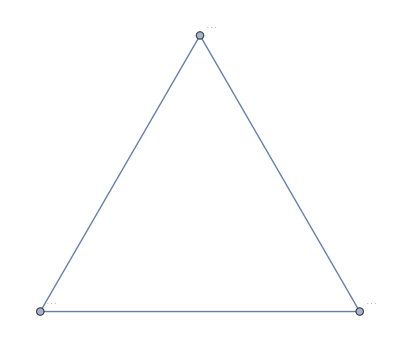

```mathematica
Graph[{"(*GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJzsvQlc1tt1771UUFCcFRERxXnEeZ4RnHDEWVQUBBUBFRAFZVAQFed5OkPO
ydA0bdM2adqkOZnbvrd9e5vb8bb3vrdp+962adqbpsmbtEma7Pf/e/6HcxwY
nudZ6//fD7DW5/PtJ0nPedjjWvu/9xpSck9mFXQnorIY5/9kHT67qrT0cOX2
Ac5/2VlSdvxoSf6R9SXl+UfzSxfm9nD+R+ruEkUqKiodQKIdEh1mOqxx2OVQ
4HDW4YrDY4dPOPy6wxcdfs/hDx3+p8O3HL77Cj9xMK/wkxb+ub92+Kv3f+sb
7//2rzh81OG+wyWHUodch20OKx2mOgz1ZBRUVFRUVFQ6j8BWznLY7FDkcNXh
Yw5fcfhzh+/Q67a6I4DzxN87/JHD5xzecqgj96yAM8xkh9784VNRUVFRUYlI
wZVbikOGwzGHGw6/6vCnDj8i+3baNv/i8PsOHyf3PuGAwyLSOwQVFRUVlY4j
uKNPdzjp8NThdxz+P7JvYzsq/0ru28O75L51bHIY49At2AlRUVFRUVERFLzH
4537oMNdcu38D8m+vewqfO/9Mb/7/hxgLnq0OWMqKioqKiqhCezKdIcjDm84
/InDT8m+DVRe5gfknglukusfObKlyVRRUVFRUWlF+jlscLjs8GWH75N926aE
B/wPP+1wxmExufc2KioqKioqkL7kvtnD7x7fjy3Fximdgx++P8dX35/zWFJR
UVFR6SoCnQ9f/CaHbzr8nOzbJcUO/+7wJYdzDnPIzYyioqKiotJ5ZIZDBbn5
a6DzbdsdJTL5Z4dPOuQ5jCAVFRUVlY4mSISJ+134h/8t2bcrSscE+ZfwVrCU
9G5ARUVFJVJlMLm55X6NNOZekecfyY3/QA4CnC9VVFRUVOzJEHLjvz9L6ren
+Af8CLHmsPbgP6qioqKi4r0Mcygmtx7Nz8i+LVC6NjgL/JLDTtJ4AhUVFRVp
gV6FftXvfCWSQT2HT5H7RqC5BlRUVFTCE5Sn3ujwi6R1cpSOx7cd7jnMJRUV
FRWVYGQiuXVi1W9f6Sz8Bbn1i+JJRUVFReVFgQ9VvsPvkX1dHbHExsaahIQE
M378eDNz5kyzePFik56ebjZt2mR2795tDh8+bI4fP25KSkpMeXm5OX/+vKmp
qTFXr141165d+4C7d++a+/fvvwT+txf/mStXrgT+XfwGfgu/id/G38Dfwt/E
30Yb0Ba0CW2LiYmxPk4RzI/JzUeMey2tV6SiotKVJdXhEXXxHPtRUVFmyJAh
ZsKECWbRokUmMzPT7N+/P2BzL1y4YG7cuGGePn1q3nrrrQ4B2nr9+vVA29EH
9GXDhg2BvqGP6Cv6bHvcLfN3DhcchpOKiopK15BeDtnk5mG3rYN9tfEjRoww
s2fPNuvWrTMHDx4MfFc3NTWZN954w7rN9hv0GX3HGGAsMCYYG4xRFzsbwJ8V
PoNpDt1IRUVFpfNJokODw3fIvs71jO7duwds2Pz58822bdvMiRMnzOXLl7uk
jQ+X58+fB8assLAwMIYYS4wpxtb2/HrMf3c47tCHVFRUVDq+zHP4OLlvn7b1
qyjR0dEmJSXFrFy5MvANW11dbZ48eWLdfnZWMLYYY4z1ihUrAmOPObC9Djzg
uw7XHEa2uKNUVFRUIleQK32Hw++SfV0qBvzb4O+WnZ0d8I3Dd6ptm9jVwRzg
TIA5gX/BsGHDrK8TQX5KbvzrgtY2moqKikqECN72Cxz+B9nXnSxw14zvy7Vr
1wZ82O7du2fd1inBgbnCnGHuRo8e3VneDb7isI7UR0BFRSWypB+59XX/gezr
ybDo1q1bwFbA9/706dPm0aNH1u2YIgPmEnOKGIRRo0YF5tr2emPwTYc9pPGD
KioqdmWQQ73D98i+XgyZuLg4s2DBAnPkyBFz584d63ZK8Yfbt2+bvLw8M2/e
PNO7d2/r6zBM/he5OTM0z7CKioqfglq7dQ7/Svb1YNA0f+PjOxBxZ/p+ryAu
A74cW7ZsMcnJyR3xbgB5Mk+S1iRWUVHxVoY6XHH4AdnXe0HRp08fs3DhQlNQ
UBDIcWfb3iiRza1bt8yePXvMlClTTK9evayv3xDAOeCYQ8+gd7OKiopK+4L3
/UvUQew+7nSXLFliTp06pd/4StjcvHkzcBaYPHlyRzoL4BxwmNQ/QEVFhSf4
loA/P2qZ2dZrbdKzZ08zY8aMwFu+xuArkjx8+PCDNwKcBbDWbK/3IEAuIdTM
1ngBFRWVUAS1d+Fb9P+SfT3WKvgmg/9eUVFRh8qPr3RMnj17FqiLdPLkSbNx
48ZALYMOkKv4DxzSQ1UAKioqXVIyya1XaltvtQhiuVFvDrXo9DtfsQF8BlHf
6OzZs4H8zvAnHTNmTKT7Dn7eYVoY+kBFRaXzyxSHz5F9PdUiAwcODOhZ6F3b
+l9RmkEs4blz5wK+Jvn5+Wbp0qWmf//+1vdLK/zM4V3SmoMqKiqujHB4m1zd
YFs/vQTuVhGjXVZWZt58803rul5RWgJrE/kjKisrA+cAvA+gbtH48eNNjx49
rO+jFoAfL2oP9w5LY6ioqHR0Qd4QxA1/n+zro5dAnv0dO3ZoTp5WePz4ceAe
pK6uLnA2Onr0aCD/PfzTVq9eHaiNg/gHnJ3A9OnTA/FsAPkPQFJSkhk6dGgA
/Gf8b8h33PzP4Y2l+d/H74GMjIyAXTtw4ECgNl9FRYW5dOlSIGYOb+O2x8U2
zeeAqqqqwDkA4J0KczJ48GDr+6oF/rfDwfDUh4qKSgeVDRRhOfrxrY/6LbhL
7arf+nhXvnHjRmAMEMcAew47DnsMG403kEiudxcTE2OGDBkSOEfgzIG6iDjH
HTt2zFy4cKHLnOdevQ9oBmMxadKkSLwTeI/c9z8VFZXOK2MdPkX29c0HxMbG
mvT09ECstW297Qf4TsZ3O/IRZWVlmeXLlwfse3x8fCTaBXEQOzdixIhArCbm
fffu3YH4jcbGxsD5x/b8SINaRK+eAzD3yEmF85Lt+XgB1Bq869CfVFRUOpPg
rr/K4d/Jvp4JAHu3f//+Tu3Dj3tx5Bneu3dvoG4w7tg7QLyYNTA2iYmJgbHC
tzJq+HWGOwPcB2At4L3kxXMAYgdWrVoVaf6CqOGF2t0qKiodX2Y6/CHZ1ysB
YANxt92ZvvXQl4sXL5qDBw+atLS0QFx4B64rE3Hg3QPvCYj/gK/DtWvXrM95
uOeAq1evmtLS0pfOAfAX3Lx5c+DsY3usX+CzDiNJRUWlI0qsw1WH/yTLugRx
0bjvxT2obR0sAfzv0Bd8o6JfqDFge4y7GvhmxthjDjAXHcn/EDmp8d6BmsQv
ngPAvn37AjkGkefC9hiTW9cTPsLdSUVFpaNIBrn1Qa3qD/iqwfe5o36vNYMY
b9xF4/sTMV16hx95wK8Ac4M5wlzdv3/f+rppD5wj4Qvy6hkAHDp0yKSmpkaK
T8jXHCaSiopKJMsAh6cOPyeL+gI6C2+4TU1N1nVsuHoZPmnwX4c/u82xVMID
d06o54vzAPL0RfJ704MHD16KGXyRvLy8QCxmBJwDfkLufaLWF1RRiTzZRG48
r1Wdi3hxvHHa1qmhgjsK+OnBF1+/7zsfqBWBucUcR2oOScTAwF+0pXNAbm5u
wAciAt4F/sRhAamoqESCIH8ffHWs6QTYfcTuozaKbR0aLPjGh65FDFqE5mZR
PAR5jzD3WAOR5DuAe4qGhoYWfQNATk6OmThxou1aA/ApukWaP1BFxaZsc/gX
sqQHmv364PtuW28GA96EDx8+bKZOnRoJ96lKhIAcFJFWRxI1h5vrCrQEYk3g
J2j5HIAaw7NJRUXFT4lzeIMs6sxZs2Z1CLsPPYp4Q5xT9F5faQ/4EeINCz6E
kXAvgHyQr8YLvhovgNqDFsfsxw4VpDECKip+yFyHvyJL+x0+Vfgusa0X2wI5
haC/4YMIfW5rrJSODXI4YA3ZPgvgTgJn7dbOAM25hfGmYXG8vuyQRCoqKl5I
N3JjcXHe9n1/x8XFBXynItWPGvoZ+dTmzJmjNl8RB+sfNZAQS2CrPgVyIZ45
c6bVMwDyCK1du9Zm7inkC9hLKioqkpLs8FWysKfxTg4/Kdyj27bxLQGfQ8R4
9evXz7qNULoGw4YNs1afEufvy5cvt+of2JxXGPUFLPq4vEvuG6WKigpPkIv7
/5CFfYw380iM5cO3PuqqIp7Lsv+T0oWBPwn2CNai3/diyBmAu4i23gSQQwg5
kSyNz7cclpCKiko40o/cc7Tvexe1ZhEXZdvOvwq+e/Ctj7tYG+OiKK2BGgVY
m37mFsCZ49KlS23eBQDUmbQU44qcQag71oNUVFSCFdTi/kvyeb8ij/2BAwci
6o0f3/rw3x87dqx1HR9RIA9MX+cclBBvaOxoQzOmGlo8z9CaFYa2rje0Y6Oh
fVkuuXsNHck2lO9QcsSl9Kihc8Uu+M/N/zv+Gfyz+Hea/338Fn4zw/ntxXMN
pU5x/yb+NtpgPydNxID8PIiNgc++X34CqDHcll8AgA8jag0iD5KFcfmCw2BS
UVFpTzaT60fj6x7FPSbyj9m2980gVh9vrAMGDLCu030H/ovDhxmaPtnQysWG
sjIdu7zfUHmhobpyQzdqDT26Gllcr3HbhjairWgz2o4+oC89o+2Pq8+MGDEi
kL/Xj9iB5ruAts4AID8/P5A3wMJ4/J3DfFJRUWlJcEeG/Nq+5u5HHTX4C9m2
982gZgD8DS19p/gHbPzokYaWzDe0zfm2zttnqOKEoaZq+7bcK65dcPuIvqLP
6DvGoJPHa2CP4SzrR02iW7dutZpD+EVQb9jCO9p/OBwhFRWVF2WIw2+Tj3sR
fnOIbY6UOmm1tbWB9kRAfnN5+vd1v4NxN5+zy1D1aUMPr9i3x5HElSpDx3Pc
d4YFsw0NjzfUyXw7caZFDCFq/3q5l3DfUFNT0+4ZAH6LqC1kwYcWfk2oT66i
0tUF+TO/RT7uv/j4+MB7oW2bj/dR5Fy16KMsz5BBrv3au8391r1zyb5t7ajc
vuSO4Z6t7pgOHmR/fgXAGRc5Bqurqz3dW7hLa883EOzatcsMGuT72P5Xh1Gk
otJ15aDDj8hHvQMfZds5zqGbCgsLA++jfvXdExBfjfvrtKXum/eV8/ZtZmcH
YwwfRYw5xr6D13FADCtq/3q115C3o704QYBzuIWcAf/skE4qKl1LYsjn/P0p
KSnW8/XD7sMPGTmE/ey7GNFRhiaPN7R5reszf6fevj3s6mAOThcY2rTG0PiU
DnseSE1NDdzZe7Hvgn0PANnZ2YH8Rj72/acOZeTmN1VR6eyS6PAH5NP+wjf/
pk2brMf0wScJZxC/+i0G7vOXzndj4m5dtG/vlLa5W+/6ESyZa2hQf/vrJ0Rw
HwBfGC/O3sG+B+CMPn/+fL/9Aj5J6hOg0rllmsPfkk97Cjk/bNfqqaysNJMm
TbKuV4MG3/iTxrl+aIiNt23PlPB5cMXQmUJDa5YZGjvKnVvb6ysIvKyrjbyB
FRUVQd0F7N69OxC74GPff99hGKmodD7BO5dvcf3wL7Lp2w+7bynOOHT69HZj
0U4cdr8fbdstRZ5btc5Z4JihzDRDk53zXUzkx5fi7g4xMdI5uJ8/fx7wPQzm
DAA/HZ/38V87TCYVlc4jh8nNhen5/omNjQ3ky7Nl91GvHDor4vPyO+MU8CnH
XfH9y/btk+IPdy8ZqjnlnPUOGtq6xtD0Sc5aiLG/HtsAPnmIG0SeP6l92vwe
EMwZAGRmZvqZk+O7DitJRaVjC3xa6sgnPYEcubbq9Tx+/Nhs2bLFREdHcJ43
5KCbPd21+ffU5ndpHjQaqj9jqOSwoWPZ7llgyviIzlOI/NzSNbhxpggmXxBA
LkMfY3ZQ53w/qah0TOnl8DHyYa/gnhC214aPH74joBciNk9vVJShuTMcHe98
791rsG93lMgCPgKN5wydzHXOhfsNFew1tG6FoXGjIjaWAPW5JPN3PHnyJKgY
QXDy5EmzdOlSv/J0IRdqHamodCwZ5PB18kEXDBkyxNM8Im2Bvztu3Djr+rBF
hg11ffg6cz5dRY6H758DTr1/DgC5uwytWGBo8ED767kFJOtzh+IT0Owb2K9f
P7/6+qZDNKmoRL6Mcfjv5MO+gF/9nTt3fLf7qBMUkW/88O/G/T7q2Gl+XSVc
kIv45AvnALBjg/s+EGExBPANQL0M5PmR2Nv19fVBnwGOHTtmRo0a5Vdf33MY
QCoqkSuob/Ud8ngvwO5u3LjRt/qizeB9AXVMekZavZaRiW6O2Jt19m2H0jl4
+Mq7QDN5uw0tm29oSGTdCSBO7+jRoyL7HD68weQJaH4PQKyRT/38U4ckUlGJ
PFnp8G/k8R6IiYmxUq8P+cMiKm8f3mbnzzJ0tsi+rVA6L/APaDhrqOTQy+cA
sH29m3MwgmpWIY/g9evX2fs9FL/A5nqCPsUH/I3DOFJRiRzZ5PDv5PHaHz58
uLl8+bKvdh++QagZEDF1+RC3vWqJo5PP2bcNStcB5wDECyBu8NVzQM52Q3NT
DfWKjHsx3M/hno7rDxyKXyA4dOhQIOeYD338R3Jzqamo2BbEqCCHtadrftas
WWJvfMGC3IEJCQnW9VkA1NDNTDd0s9a+LVC6LncbDJ0vNlR44PVzwJHdbt7h
uD729wu58cB4z+foANQOOH/+fNBnANxN+lTP858cZpKKij05TW6MimfrHN/d
8LX10+4jRyjyjUSEf19SovN9tUtz9CiRBfIJlh99/QwAkE9g/UpDw4ZY3z/w
D8T9Hex4uPoAfkaoSRDsGQAsW7bMD/2BPEELXtPKKireyznyeO/GxcUFcnX7
afuPHz/uZ1xP60wYY+hUvn09ryhtce38yzGDr7Ip3VBivPX9hLw9+I7nnAFC
iQ0A27dvD/gredy37zuseE07q6h4J2fJ4/0aHx9vGhsbfbP7qBXgox9v64wZ
Zeik2n2lA4FYgYvlLfsGfHAOWO3mpLC4t/A9vn79etZdAHRSKGeAw4cPm4ED
PY+V+A+Hza+raRUVcakjj/cp3u3u3r3rm+3HHYMPe7RtRgx3a+za1uWKEi7I
L1lV1PoZoPkcEO+Lj1yr4C7g0qVLYesLxBeEcgZAngAf8gYjX/D219W1ioqY
1JPHe3Pu3LkBv1s/7D78g5E32Kpvf+Iw1+5rvh6ls3C1yq0r0N45YOgga/sO
MQKoJRBuDpFbt24FnSMAFBcX+1EH/D8dclrU3CoqPLlGHu9J1NjyK6cP4gh9
zN31OsPj1e4rnRfEC6LOYEtxAi/6CWYsMzTAnr8N4orCrSuIO8rS0tKgzwDI
FYTvG4/79DOH7BY1uIpKeOLpdz++vw8cOODbfT/qA/tYy/Nl+vQ2tHOTW3/N
to5WFK9BTsqy/LbvAnAOSFtsrQ4x/H1hn8PRJYgVKisrC+k9ICMjw+s7R9wD
7GxVm6uoBC815OHegx0Od++Fc17Hed/L/rQK8vUtna/1eJQuSBu5g14E9YZm
TbWSTxC+gYj5Deft8dGjRyHlCgRZWVle5xGHP8CG1tW6ikq7UkYe7jnUzK2r
q/PF9iOXD3KEe9mfVpk20VBtWQToYUWxyO1LhsoL2j4DgD2b3JoWFvYqcnyH
U1Pw8ePHIZ8B9u/fb/r27etlf35Ebl52FZVQ5RR5uM+Qyxd19Pyw/Tk5OYE8
IF72p0Xihzj6LMe+3lWUSAH+LnVlbfsFvOgjOGiA7/s2NjbWFBUV+XIGyMvL
8zr2CPkB5reh51VUXpUD5GFev8TERHP79m3P7T7u8hYuXOi/3e8d677xa84+
RWmZ23WGTh9p/wxwdJ+hxXMM9Yz2dQ/jPQCxQaH6I4dzBigoKDBDhniaK/F7
DrPbUvgqKu/LFvIwn//o0aPD9rcNBdzhJSUl+W/7p0821FhpX78qSqTTHCPQ
3hmgucbQWP/jdaZPnx7IDeb1GQB5R3En6mFfUJd9Sht6X0UljTys4zdhwgRf
avhgP/Xp43MNkn59DeVr/h5FCZlrF1quL9wSqCsQ19vXvY2afqj/7fUZALWD
Ro4c6WVf/rfDmDYtgEpXFbwR/YA8WnvTpk3zPK8P7upQ99PXuj34WwtmG7pe
Y1+PKkpHBW9l5wqDOwPk7TY0fZK793za59HR0YFcvqHoI3zrhBobiDMAfBA9
7Mv/chjRji1Q6VqSQm49SU/W3IwZM8zTp089tf2Iw01NTfXP7gPkMy89al93
KkpnoeGsoRNB+AaCLRluXWwf93x6erp5/vy5p2cA5AocN26cl/34c4cBbVoE
la4igxz+kjxaawsWLAhpv4QD4gg8vjd7GcQnr1nh1kK3rS8VpbNxs9bQyXby
BzdTsNfQ3FRfcwZMmTIl8L0RrH4KJz8AcgVOnjzZy3582aFnO7ZBpXML5v9L
5NEaW7RoUSDHvpe2v7q62t+4fuTtrSqxryMVpTOD94Azx4I7A4AdG3zNI4x6
PqgDFMr9ZCi5gpvPAFOnTvWyH2+2ZyBUOq10c/gEebS2li1b5nkuf9Tf8KG+
9ofgnf/OJfu6UVG6As11hYM9A+AuAH4BPukDfHeE4hd4586dkOx/Mx6fAara
MxQqnVIuk0drCjUuvP7uR+0u3+r2xfXRPD6KYovrIcQHgI1pbg4OH3QD8peX
lJSE9FYZSt3A5nuAiRMnetUH5Hk5EIS9UOk8kkse7Qfk1/fyvR/nCvjgeNX+
15g83tCVKvs6UFG6MnfqDZUFkTu4mUM7DI0a4YuOwHfIvn37gtZhyE0S6h0A
zgDjx4/3qg+oFZDWvtlQ6QSyktz5Fl9H8Ivx0s8fMbW+1e+JjnJz+Gl9XkWJ
DLAXq4qCPwOAFQsMRUX5ojPwXRLsm2dDQ0PIZwDEBSB/mkft/z8OE9s3Hyod
WJD/6V/Jg/WDeBXYZ69sP97OUlJS/LH9ScMNVZfa13eKorxMqD4BYNdG3+oI
zJkzJ6g8JzgnXLx4MeQzAOoSwPfQo/b/tcOwIOyISseT4Q5/Sx6sG9hlxLh4
ZftRK8DDNf8y82e5d4229ZyiKK2DHNvB5glo9g2cNNYXHRJsnlOcARC/FOoZ
oLCw0AwbNsyr9v+BQ+8g7IlKx5EYcudVfL0g7j7U/Nih0NTUZOLj473ft/Al
3Lrevl5TFCU4kCcgFL/A5vcAH/yGg61zAn+mqqqqkM8Ax44d87Jm0C8EZ1ZU
Ooi8QR6sE5xBvazjd/nyZa9rY7ogbri80L4+UxQlNO7VGyoNoo7gi2xb60t8
AO4sg9GPz549M2fOnAn5DIC6gYMGDfKq/aeDtC0qkS355MH6wLpDLItXtr++
vt6fvD7jUgxdPW9fjymKEh4PGg1VHA/tDID4gBEJnusX1PQLRk/ivSDU/EAg
Ly/PxMXFedF21IBdEaSNUYlMQU2f/yDhtYGcO/Bd8cr2I6eGR2v6ZZbOd/OM
2dZfiqLwgF/g+eLQzgBHsw3N8jS3TgDc0yPmLxg/p1BzA4ADBw4E8hB40PZv
OyQFaWtUIksGO3yLhNcEYl1Rz8Ir23/27Fnvc/r17Gkod699naUoihw4A9SV
hnYGAOlLPI8RxH1pY2Nju/rvypUrYeUI3Lp1q1f50P6LQ6+grY5KJEgPhy+Q
B+sYZ02vbD/Ovj1hm720/agXdq7Yvq5SFMUbEB9YGEJsQCBGMNNQXG9PdU+/
fv3avTdFTEBtbW1YZwAP86I9CtbwqESEXCcP1sHGjRs9tf1RXufpSEwwdLnS
vn5SFMVbGs85dj3EM8D+bZ7nCcC75qVLl9rUheHGBADkH/Co7blBWx8Vm7KV
3JzOovM/b948z+r5VFZWevV+9SGTxhm6WWdfLymK4g/XqkLLEQCO7DaUnOip
Lurbt28gtqktnYg8quHEBIBJkyZ50e5/d5gbtBVSsSHI3/hvJDz3yDvtVV7f
CxcueP/ev2iu+vkpSlcEtYOKDobuFzjFs1z7ARDXjNwmbelG1AwOxx8QOQIR
d+BBu5E/bkjQ1kjFT+nn8JckPOcJCQlB5bEIB7yF9enTx7t91q2bocx0+zpI
URR7IE9Q8aHQ/QKXzPX0DIC8Zrdu3WpTRyJ2MJw7gKNHj3oVP/15h+7BmyUV
n+RdEp5rvFUF47MaDvhdT+P74UtwaLd93aMoin3w9leUE/oZYM0yQz16eKan
8H2F2iZt6UrkQgnnDHD48GETG+tJnqPKkCyTiteyg4TnGLEkFRUVntj+a9eu
eZvXLzbGUOlR+zpHUZTI4VaY9wCbMwxFR3umr5KTkwN3/a3pS/hdwUcqnDPA
9u3bvYgLRG6gBSFZKBWvBPkZULtRdI737Nnjie3HfZaHeavdvJ4VJ+zrGkVR
Io8bNeHdA+zYYCjGOx/lMWPGtFlDDbVVw8kPCJYuXepFm/8fh74h2CkVecE7
zJdJeG5nz57tia8/7rlw3yXd3g/o19fQhVP2dYyiKJELzgAnQvQJbM4RgLtF
j/QX/Pbbqh0MX4Fw7D+AD7cHbX4WirFSEZfzJDyn8BsNpnZlqGBdjx3rYf3N
gf0N1ZXb1y2KokQ+gXuAMM4Aezd7micI8fttfXuF6wtw4sQJr2oF7QrJYqlI
yRyHH5PgXCIOr7241HDAesadgmRbX2LwQEMXz9jXKYqidByuh3kPgDxByCPq
kT5bt25dm7o03NxAOTk5XuRZ+a7DyJAslwpX+pBwrF+3bt0CZ0Qv3vw9zEtp
KGGoocYq+7pEUZSOx/VqQ4VhnAFytnuaKzA7O9sTX4BNmzZ50d6vksYE+ilv
kPAcYl14YfsPHjzone0fmWioqdq+DlEUpeNy7bwJOVcwQA3hId7EMcFnv7i4
uFW9ilqB4foCzJ3rSV6DstBMmEqYso2E527KlCmBnNPSth/r16OaVIaSHNt/
o9a+7lAUpeODegGh1gwCubvc90cPdBzu6uvq6lrVrw0NDWHZ/5MnT5pRo0ZJ
txd15meFaMtUQpMRDv9CgvOGWLz79++L2/6amhrvcvrHDzF09YJ9naEoSueh
Nozawc33AAO9yWWGHGnXr19v1Rfg3LlzYZ0BkB8QdQiE2/sXDrEh2jSV4OUz
JDhfPXr0MNXV1eK2H3mtPcvtN3SwoSv63q8oigecLw7vDHAwy1C/OE90XmJi
Yqv5gZAzIJwaAWD37t1e3M9eD9mqqQQje0h4XWVlZYnbfqxTrFfptgbAGbv+
rH0doShK5+VcYXhngOytnsUGTp061Tx//rxFnXv16tWwfQEWLlwo3db/JK0T
KC2DHL5NgvOEfBDSb/64j0pNTfXG9vd1ztY1pfZ1g6IonZuHjYbKj4Z3Bti3
xc1B6oEOzMjIaFX3hhsTWFJS4kWtwD92iA7Rxqm0Lh8hwflBTYj2ak+Gw5Yt
W7yx/ahhUVliXy8oitI1QL3w00fCOwPs2mioV09PdGFeXl6LupcTE5ibm2t6
9hRv77lQjZxKi7LK4eckODcFBQXitr+srMwbX3/k3D5bZF8fKIrStbhTb6jk
UHhngO3rPakZBDtdW1vbqt9VuO8Aa9askW4r4gEmhWztVF6U3uTWWRCbl8WL
F4vbfrw/9enTR972o4av1vFTFMUWyBMcTlwgQN1AD76J4uPjW/UHvHDhQthn
gIkTJ0q39asO3UI1eiofyE0SnA/E+knn9kdefw9iSQ1162YoZ5f9/a8oStfm
8tnw7D/IWCqvG8n1B2zJfwv6ONx3gOPHj5t+/fpJt/VI6GZPxZF55PpSiswD
8vuePXtW/Nt/yZIlnqxv2rzW/r5XFEUBF06GfwaY541PNPytWtLJyBcQ7h3A
zp07A7ZCsJ3fIzdvjUrwEuXwR+TDWuGwd+9eb2z/4rn297uiKEozD68YOnMs
/DPAJPnap7DTsNmv6mXEYSGvS7hngHnz5km39ZdDtoBdW6pIcPxTUlLEY/0Q
bxKF93lp2z9hjKF7l+3vd0VRlBe512DoZG549v/oPkNJ4nF2pnfv3gH/q1f1
89OnT8N+B0BMIHwMhNu6LQw72BVlrMO/k9C4I8ffxYsXRW3/3bt3vcnvl5hg
6NZF+/tcURSlJW47+qkoJ7wzAGoFeFAzMDk52Tx79qxFv+xw7wD27dsnHc/1
9w59w7CHXU1Ec/xu3LhR/N5/5syZ8rYf9bQbztnf34qiKG1xrSr8d4ADWYb6
yOcIXLt2bYvvAPD5CvcM4EGdwKYw7GFXkjUkON4JCQmBeyBJ2+9JPV/kntD8
PoqidBRqT4d/Btix3o1tFtSh8AVADpZX9TVqu4VbH6CoqMgMGCB6X/Fj0pwA
rUlPh78kwfWA2lCSth/3SZ7U9MvbZ38/K4qiBM0VQ+UF4Z8B0uXjAhG7d+fO
ndf0Nt5/w70D2LFjh3Q7vxiGbewKUkmC47xy5UpR24/aE/AjlGxjgNXLImAv
K4qihMi9+vB9AcB08Xw7ZtasWa/pbvgGlJeXh30GQK4B4XaqL+DLgvjIH5DQ
+A4cOFA8z8/69evlbf/YUW6ebdv7OBJ50GiortzRE45+2b3F0IbVhpbMc3TG
ZEOjkgwNGeSCWiOgOWYXecfx3wf0c///w4cZmjjO0PxZ7llre6ahQ7vdnMrq
a6koPK6dDz8/IGICEsX97E1OTs5r+puTEwB5gYTzu37LITZ0M9lp5SMkOP94
t5G0/XhHEM/tD3+/K+ft799I4Gad8x2Raygz3dCs6Y5OcGx2VA/581ZLDOhv
aJJzPli52M23ePGM/fFQlI5E9anw7wAO7RD3B0SNgMuXL7+mx8OtEQgyMzOl
dU9lG/awK8kMh5+R0Lgid4Ok7Uee6cGDB8vOfQ/HtpUds79vbXH1gmtr8T2P
73PZfFt8UGs5dYqhbesNnSt2c5/YHjNFiVSwP8oYvgBZa8XrBCAn+6sxgbgT
Dtf+g7FjRXMYfd8h4XVz2OUE/hAiY4q6vrdu3RK1/x7kgjK0Z6v9Peu3foAd
3breffOINHvfHnF9DM2e7p5ZbtTaH09FiTTuXjJUfCj8M8BS8Vg7s2HDhtf0
eUNDQ9j2Pz8/X9r/+zF1bckkwfk+cOCAqO0/duyYvC3BO7TtveoX1acNrVlh
qF9f+zZcCnyn4L0AZ4Hbl+yPsaJEClcYeQGAcI5gxIDhzv9VX0DECYZ7Blix
YoVkG3/qMJW6piDH/1+Q0FgmJSWJ5vhF3Kh4LSjkv7xbb3+fesmlCvcdP36I
fVvtNfA1XDDb+e7J0zcCRQFVReHb//w94vkBR4wY8do7wLVr18K2/8gNPGjQ
IMk2/iZ1TSkgwXluKfcDB/G6ftFRhi6csr8/vQC2r+SIe0fuQb3vDsHQwe77
xvUa+/OhKLZAPFPJ4fDPALs3ivv+bt269SXdjryAFRUVYZ8BsrKypPVHGnUt
iXH4OxIav9mzZ4vafqwN4RqQbgyb7b0pDe6/d27qGt/6wYI7gWULDNWU2p8f
RbHBtQvhxwSCxXNE9yTqtOHd/0UdDz8xji/g6NGjJdv4Bw7dqOtIOQnO7ZUr
V8Rs/5MnT+RrP02Z0Lnuh5vtfmd615cG50fkKqgstj9fiuI3VcU8X4DkEaL7
Eb77+O5/8Q6gsrIybPt/6NChQG05wTZupa4hqIH0TyQ0bi35eHJYt26drB2A
7/jVThLnD7uPO24P6nd0WprPAcg3ZHv+FMUvkL/rJOMdAHkBYmNE9+L+/ftf
8/Hi3AEg16Bg+5D7Hj5xnV3qSWjM4J8nmeevrq5O9kwH3Y/8dbb3Ihe86e3Y
qHafuxbmzjDUcNb+fCqKHzRV894BMtNE9yDiw2/cuPGSzq+pqQnb/iMvIH5T
sI0HqXPLEHLzHoiM1+HDh8VsP2IHkDNCqm0BkFPO9h7kAr8+5OixbT87C/Bt
WrVEcw8rXYMLJbx3gCnjRfdfamrqS3r/8ePHrDuAtDTRM8pfO0RT55WrJDRW
ycnJL73ncBGv8zQ8vmPH+iFWYYJsPK7yAvCd2L+jc/mFKMqrPMQ7QC4vJnCA
bBw28rq8qPvr6+vDtv8nT540Q4aI+j8foc4pg0nw21+yti/uhJAzWqptgfy+
VSX291444K5/q3x9bqUVxo42VFNmf94VxSsQD8C5A9ixwVB3uXis/v37B777
m/U/8gOUlpaGfQbYvn27pE74G4ee1PnkMgmNUUs1HjksWLBAVqevT7O/58Kh
/Lh7b2HbJnY1kBsCOZPuaS1IpZNyrpB3BpglW4MX9XxetAGoFxRB8YB51Llk
EAl9+yMuH356Urb//PnzsrH+iIW/22B/v4XCnXpDKxZ1vLz8nQ3khzx/0v56
UBRpoBOLchjvAHvdmqlCew1x41evXv3ADjx//px1B7Bv3z5JXfA31LnuABpI
aGwk6/vBfyAlJUVu3mA/T+bb32uhgBz9iQn2bZ/igncXvL+oX4DS2bhYzrsD
2JIhutfmzJnzkj3g1AYCwvUBc6lzSD+H75HAmHTv3v21PE4c8vLyZHU38r7Z
3mPBAvuCmL4If+fvFUMmZSKZJWvJbMwmc+AkmeJLZKofkal/k8zNXyRz61Nk
Hn+OzNPfInP3V9z/3vgOmYvPyJQ1kcmrIJOVSyZtC5lpc8kMHGK/X+0ybaL7
bmp7nSiKGI7OOXWEdwaYPE50n72YN57rB4D8AoJ3yf/ToQd1fDlHQnO1aNEi
MdsP/48BAwRrTeBu6mYHqQ2LuFzkJLRt414Btn7KHDLbDpMpd+z27V8i89Fv
kPnY78iDs0LtYzI5pWQWZ5AZHG+//6+BGIGTR+yvF0WR4kYNLydA3m7RPCSo
D/Ri3TjuHcCECaJ6dRd1bOnl8A8kMBb49m9sbBSz//D/kGjXBxw9YH9vBUPV
SUODB9q3bQ7dupMZP43MrqNkLj0n887XvLH1wXL302SOVZNZuJpM7zj74xMA
9ZSyMu2vG0WRopJRIxCsWSa6x3Jycl66Azh9+nTY9h+/1V2uBtp/o45dF+Ao
Cc3RsmXLxGx/U1OTiY6OlltDqHtne08FQ94+Qz0F+x0GPXqQmbWYzNHzZB79
hl173xbvfJVM1V0ya3eS6T/I3nh9wLyZHTufhKI0gxhjji8gSBkptrf69u1r
Hjx48IF94OQDAJMmTZLc+2uoYwreLv4HidiMHoGazVL2f+7cuXLz0zs28vP7
Ixf3mhVW/ftHjSezv8Sx+Z+1b9tDPgt8zfUjmL+KTFS0JfsPRiZq/mClc9Bw
hmf/D2aJfsusXbv2A/vw9OlT1h0AagMJ3gF8iTqm7CChuVm5cqWY7UfNJ6l2
BUAdPNt7qS3wzThTNnY2WHpEuW/ruNu3bcOlePI5MrsKLPoQwidAawoqHR34
H5/O450BBOsEIx7wxW9M7h3A1KmiOncedTz5PRLoO+7pb968KWb/Re9mEuLd
uyzbe6k1rtcYGitc0yAI8Ha+aT+Ze5+2b6+94iNfcX0FcK/h9/hSTC9DxXn2
15eicLhSxbP/R/eJ5gZesmTJB3YCdeA5dwCILROsJfcJ6liC84pI31evXi1m
+5EzWKpdAYpy7e+h1qg/65xPhvpql+C/vynb9a23bZ/95NwdMqMn+HwGwP1i
dpb9daYoHMoKeGeA9SvF9hTu7JEHsNleIM8c5w5g+vTpUm37iUMSdRz5OAnN
x4s5mriIxmZMm2R/77QGavcI5spqj+ieZDL3ujH4tm2xLT76dTIn6sgkjPTx
DAB/jm3r7a83RQkXxExz4gEB/GKE9hRywTfbC/gEcuw//AAE8wFcoY4hiQ4/
JoE+S+b6w12ORJsC4F6nNkJrtqDuUFwf32wQfPmRb8e2/Y0UEDeAHEWxfXw8
B6B2gO11pyjhwq0NsGeTex8msJdgry9evPiB3UB+eM4ZQDAn4Hcd+lDki1id
H4y9lP0fM2aMnL5NW2p/z7REZYloboy2wHfumRv27W2k8vAzZNI2uzkO/JiP
QHyH7fWnKOFw55KhE8w7AOTLFNpLL+YFvn37Nsv+79q1S3KfH6PIFuT7+Q4J
9HX8+PFitr+kpERuDmBf4Vdne8+8CnzCfbD9iN/HGz/832zb2I5AzWPnrJTk
0xkgQ88ASgflQgnP/ufucv1iBfYR7gCqq6s/sB8VFRWsM0BCglh9lb+gyM4H
tJ+EdFlRUZGI7UeNn+TkZDkdu3eb/b3yKvjuj4313L4kjyNz+W37NrWj8cYX
yWRkQa/4cAboqLWnla4N4qhOHOSdAZbOE9tHM2bM+MCGwAeNY/+Fc82upMiV
3yWBPg4bNixgtyXsf2FhodzYD493c+nY3isvUlduqF+cpzYFd9hbcty3bdu2
tCNz/j6ZQX7UGUBdJ9vrUlFCpa6UGQ+YLRoP2Pz+zK0LdPLkSdO/f3+pdn2S
IlNSSWjcDxw4IPbtj/oOUu2iI9n298iLIH7W41z+/QaQqbhp33Z2FpA/aOZi
j+0/fI7377C/PhUlFO41GCpi3gGkLxXbR8jh02xLuPmAkMNOqF2IBUykyJPH
JNC/Pn36BGrzSdh/vCFItClAYkJk1WRH3EzScE/tyORZZO7/mn2b2dlATUPE
CCA/omfzB3/o/P3216mihEL1KZ79P5Yt+k104cKFgC2BTeLkA4ItiomJkWpX
FUWWxDn8Gwn0bdOmTWJ+f/AhlGhTgGMH7e+NZu465+Qx3ub1y9xH5t2v27eV
nZkLD8j07e/hGQA1rsoL7a9XRQkW3AFw/QDWLhfbQy/mA8BZgHMHMH/+fKl2
/S259XUiRfJJoF/I9Xvnzh0R2w//TYk2BUgeETnf/mjH/Fme2QzUtymosm8b
X+WN3yZT+5jMkbNksnLJrMgkM2OhWz84ZaIbjxif6ObjxX+fOofMonQyG/a4
39qo33Pnl+3341WQOyEpxcMzAHxDtGaQ0pHg3gGAIYNE9g9y0DXXBbh79y7L
/ufn50vmBF7/qhG2KP8XCfRp0aJFYt/+ojX+IinP7+Y1ntkKfItWP7RvE8GN
T5LJrXBtOOy6lO88ahNMme2eIfD9/XYExDE+/4J7lvFqXmnEcEO3Ltpfu4oS
DLgDKGTeAQjmBc7IyPjArpw5c4Z1Bpg4USxPwacoMmSiw89JoE/Izy9h+5ua
muTqL+Ke3fZ+aKZgv2c1fIcOd22uLRuI/LmIlV+/222LF31siZ4xZOYuJ3O8
hsyzz9vrP95acKfhWV+nT46cOyxFaQ9uPgAwbIjI3unVq5e5d+9ewLY0Njay
7P/27dul9jRy7A4h+9JEAv1BjgSpmL/09HQ5vXkq3/5eAMjr27OnJ7YhaYw9
P7/bv+TGFg4c6qHtCxK8fcxf5ZxDb7vnEd/PQN9w/S4862PGcvvrWFGCAXXL
uTkBN6aJ7Z0dO3YEbAu3LiAYMGCAVLuKya5EOfwDCfRl9+7dIrb//v37gfOa
RJtoXIr9fQBu1hkaOtgTmzBuKpknv+m/rau84955+5YfN0SGjSCTXeTm7vF7
bHYf9yhXEO6Ojh6wv54VJRiqivl3AInxInunX79+5unTpwEbw60JsHSpWIzi
H5Nd2UQC/YiKihLz+8M5TaJNASLh2x93tjOnemLjJs4g8+Z7/n7fnr5CZuwU
D2ybR8T1J7M9z/+axjmnPToDIE/kxTP217WitMfti/zagBtXi+2dvLy8gI25
efMmy/4XFBTIvU8TzSR78qk22hU0UnX+nj9/bgYOFIr9hM+/7fUPsjZ4Ytfw
3Q+fer/sWd1TMhOme2DPfAJ+g/guf/vL/o0Z4hY86Q/8AXG/anttK0p7VBwX
iAWQsQnIJYc36jfeeIOVDxCMGzdOaj/fIjvS1+FHQbaxTcrLy0Xs/5EjR+R0
ZO5e+2u/7Jhba1hY/4+Z7J+vG+Lb4F8n3QdbwDexuN6/M8Ce4x71Zel8++tb
Udqj6QLf/q9eLLZvYPdha1AjmGP/t27dKtUmvL/byAWQE2Z7X2LIkCFifn9i
tZYH9HfrUdhc93jzHyTmJ/IByWP9uctGrQB8L8O/XroPkcDMRf7lE0Csoif9
0PyASqSD98/TeTz7f3SfoTiZ2qizZ8/+wM+MY/9REwA+BUJ7eTX5L19gtPcD
srKyRGz/5cuX5fRiJNRPWTBbXN8Pjidz/1e9t1cNb7nnDOn2Rxq9Ytw7evg1
eD2maZs96ENcH0NXzttf64rSFvUV/DuAhTI50/Buf+vWrcA3K7cuMPLdCO3l
N8lfiXf4KbfdzWMZUTF/qCGNb2+b673ggLiux/t14zve2qjmvPaIo5NufyQz
ba738ZPID+DJO8rk8ZoXQIlsUHO1KIdn//N2G+oZLbJnEMMPm3PlyhWW/cd7
dTeZfC7IvR9L/kmJQJvNrFmzRGw/6jPGxQnVwM1YYXet43sM32WCOh72GLnu
vLRPDz/j2kHJdnck+g0kc+aGt2P81nsexU7s3WZfxytKW1w4yb8DmDFZZL80
v1kjHpBj/0FKSorUPt5O/snvSLS5sLBQxP4jnkKiPQFfu8uVdtf5tEni+t3r
fP4Xn/lU1z7CQS6DHfnevgfgnCU+1sgrpTGBSiRzp54fC3ggy62LKbBnmn3W
ubkA1q9fL7WPf5H8kQSHn3Hb29PROVJ1fsVyKuPN3eYaP7xH3Cat2eGt7c+v
7Hr3/e2Be3ovYysvPScT3VO43ZPG6TuAEtmcLeTfAYwfLbJfUMsPtge55jn2
H3WBUfdOoE0/IH/eAAoF2vpSXUUOyMcs9IbirK8ie2v7eo1bq01Qp09MJfMR
j+rb4BvXM7/0TgByKt/7tHdngOPVHrQ7Z5d9Ha8orXFNIBZwu8z3NnLWoR6g
RD5gwTr1W8h7+ZJEW3HukbD/69atkxk75ESxubYXzxPV5fD1f/Qb3tgexPYt
W++t/ewMIFdA08e9OwOs3SncZvidNFXb1/OK0holh/lnAKF8QM056ysrK1n2
PzMzU2oPv0veymAS8PuPiYkJnJu4th/5/vr37y8zdnu22lvTpwtE6/r16EGm
+pE3NuetL3lcq7aTgfzBuK/3Yi5wt5MyUbjNC+fY1/GK0hq1p/n2f5nMt1Zz
zbpr165FyhvA9xx6kndyWGLcFi5cKPLtf+LECRmdh7gQWzF/yDOUMFRUh+/M
98j2vxcBPv69Y92YtbSlhnZucuvZlBwxdKbQ0LliQyed/1yUa2j/dkMbVhua
k2oofohndZODAbGX8JH0Yk5uftI5T/cWbC/G6VSBfT2vKC1x5xLfDzB3l6Eo
mbyq+PbHtyw3DkDMh41oPXknvy7RRuQ+krD/yMUkMmY2v3mQa0jQ1kyd403t
WtQJmjLbH3v5EtinUya4tr62LPxxvlFrqMDZ+0ucs3//vr73I7YPmdrH3pwB
jtcItzcp0Y25tq3rFaUlyvP5dwATxojslZUrV4q8AWzatElq/z4hb6QXuT6G
rPb17t07EK/Ptf2PHj0KxBCIjFn5cTvrGD5/+J4V0tu4a37w697cM/v+3T9y
hKHdW9wxkh73QD6RXEPzZop9BwQDzgD1b3pzBli6Tri92dvt63lFaQmJfIBb
18jo3Li4QD0gbi6g4uJiqbr1f+/QjeRlg8R4LVmyROTbPz8/X0bP4e7dVtzT
Srm6FOBEnbxdQd65Bav8sY+Bu2fkP/Dz/vlKlaG1qwzFxvjSR+QJuvEL8vOE
ek4Dhwq2FbEoty7a1/WK8ip4Mz3BfAMAA2V8x8rKygKx7Nw3gEmTJknt31kk
L48k2oZYCQn7P3PmTJmxspXrv6ZUtLYfYs69+K5M2+K9TQwwYaz7hm9Lp+Ce
IWO5IRk/nDYZkuBNHYbyJuG2rl1pX9crSktUFvHt/+I5Ivtk+fLlAZt07tw5
lv3fvHmz1N6tJnn5W267+vTpE/DZ59r+Bw8eBOIv2eOE37AV7zRdJhclwL0/
8sJJ2xPPas++CM7g8OGzrU+aaTgrOjetMXqC61MhPWeicZnRUe542J4TRXkV
ibrAh3eKfIPBruFNO4LeAH6fZCVVQp9I+f2jboJEe2juDDtrt7xQ1JYgF4y0
HSm96uazlWznS+CuH+8fty/Z1yUtgRpMwvmYXmXeCnlfTbwD9B8k2E7kpbA9
F4rSEsUCuQDGjhLZJ7jXxndphMQBID/vMJKTCokxQp5+Cfs/ffp0Gd127KCd
dTtxnJh+hk++dL551AmMifXO7tGAfs7ezbOvP9oD+cZSp3g3Dg6bD8qf3UTj
AZAvXWsDKJFItUBNoLXLRfYJ/NqQCwC+ABz7v2aNjF+iwwGSky9y24McvXfu
3GHb/vv378vc/aPO790G/9ds6VEx3Yw8P1eEa/oib/3wZO/sHY0fY+jqBfu6
IxT2ZYn6ary8L8icvCx/BhCN1bRdF0NRWuJGNd/+F+wVqQscGxsbqAdYV1fH
sv9ifu1yuQBjHH7EbQ/qHEp8+x8+fFhmfGzF/I8dLaaXN2bL2gzcI+BOWqp9
r5G+vOPGlSMmQbguczPID3TzF2Xn8upHnfNhlFAbcQcAf1Xbc6Aor1JyiH8G
GC9Tg7ekpMTcuHGD/QYQHx8v0Z5vk0wc4BqJsdmyZYuI/Z86daqMTis87P9a
Rcy5kM1ADdg3vihrM7KL5W1bALz1I3+PbV3BpaZMLGboVeAP+PaXZeczc69g
G5FH0fb4K8qrXCjh2//1K0X2CPzbcAfAtf+oLSi0b+G3x5XrEm1BnWSu7X/4
8KHpIXEPi5w79y77v1bHy+ScAkfPy9qKhrc8quOLb8f9nSiXTMM5N5+w9DiR
W89Hck7hC9i3v+A81pXbH39FeRGJOADBNwDEt509e5Zl/3ft2iWlU8qJL/+N
2w7ERyBHEtf+i+X7t+HTjNrCQnZi5Fg3L4+UnXj7K+5vSrXvA5BbLz/bvo6Q
Bn6ByJErPF7wBai4KXsG2F8i2MblC+2PvaK8CHK3FR/inwEmynybIQdAQ0MD
y/4jPz5q5Am05wvEE9T7+zm3HQsWLBC5+0eeBYk5suJ7PksoZsHhzA1ZGyFe
RxbgPI1aPLb1g1fcrDU0RiZ26EXwroPvdqm5Re7m+ESh9iE30rUO5rupdH6q
ivn2P3OVyB5BLV/4uXPfAMaPHy/Rnh8Srx7gVokxQby+hP0fPHgwf0zgw+W3
Dxrip3B/KjCWqO8jafvPP3C/OyXa9gHoq63YSj9BzsAEEV+dl0AOH8k5Rl5o
sfatT7M/7oryItfO8+3/0X1uTBhzfyQnJwfuupEPgGP/MzIypPbsYgpfbnH/
vlTc36VLl2TGY9kC/9cn/qaQ/q0RrCGHe//E0bK2K8CuzfZ1gl/UnzXUT76e
4LnbcvOMuI7kcUJt69M7cnM2KV0TvAGcOMg/A0zm52WBvbt161bA3y1C4gAr
KXz5r9y/P3r0aJFvfzGfiBM++/3jnlioTmHqAtnvwq2HZG1WgDUr7OsDv6ks
NtRLqBbl+wxLIvPWl+TmurhecI73brM/5oryIucK+fZ/g8wbQG5urrl69Sr7
DWDIEBE/49+i8KS/w39y/z7eQyTsv0htJLxf3qn3d13uFKvrLFo/vuljHvj7
I5+yrVqKtkE8qdAbTzOSuQGRZzgpRahtI4bbH29FeRHUqeDa/yN7RPJ8zZs3
TyQX8Jw5IvWJvu8QRaGLSL3f0tJStu1HbUWRnH9TJ/q7JmELhd6Hp82V/faf
Pl/OTgVIHmHonoV8ipEEakkKjinOZ5J5gUT9AMqO2x9vRWkG33Vc+w+ShrP3
Ru/evQNxgLB9HPu/aZPYt+M8Cl0auX+3u/M99OjRI7b9LyoSip3zOwfNKbE3
HHPhgZwdKL0maAcA/GY0Ntw97wnXDpyzTG7eETMqltt5/iz7460oL3Iql2//
hWoCV1ZWsn0Ajh4VyxVfSqHLl7l/Vyrn78qVK2XGwW8bNVsm5i9lopwNQDxY
wkg5+xQgZ5f9vR8pICZg0ADR8T17S27+D5UJtQv3cRoLqEQS5wXiAPfIfHNv
3LiRnQcADBw4UKI9n6LQpLvDv3H/7rp160Tsv4gfxNDB/q7FqxfEasYU1srp
f9F8MEC/A18H9z7IeSw0xvDdl6oT/NZ7ZOKkcgJmbbA/1orSzNUqmTeAvvw6
H/B7v337Ntv+C+W7/zsKTVIl9APyGHFt/82bN2V0FWrN+7kWhd6CBw4l885X
ZXQ/6gWI1obHmerWRfv7PhJZlyY3zg5FF+XOgPArFGnX8GH2x1lRmnlw2bHf
B/j2fwo/9w7eviXyAAnmARhBwUs+9+8hDvLevXts+y/2BuJ3vR/4wwm0e/dx
Ob2/M1/OHgW+b8sL7e/5SAU5pkbKrAGAN5t3viazDu7/mmDsR1WJ/bFWlGbK
8/n2f90Kkb1RVlZmKioqWPb/4MGDUjpkOwUvb7D1VUKCyN3/6tWr+X2PjvI3
7g+1UgXmLLonmSefk9H5T3/LrTMrtJYMLZ1vf69HOhUnRN8BjpyTOwsuShda
B+nL7I+zojRTWxoxcYCoeVtXV8e+A0BdIYG92kTBy59w/96iRYtE7P+oUQI5
1ieP93cNrpPJI7FkjZy+z8oV0vcAOeCaqu3v9Y7AUrFanmbocLk7gKq7Qmuh
f1//82krSmvA/1bCB2DEMPbemDJlimlqamLb/zFjRGoTfY2CkxiHn3L/3v79
+9m2H3H/3SVyqmxZ69/6QwzY4EEiuvW8UMzfm+8J1oEFB3bY3+cdBeijOL4/
UTNSvqDICZyQJLQebNTTUpSWgP4tFMgFPG8Ge1/06tUr8AbOtf9Lly6V2Kfw
54dff3syX0In1NTUsO1/eXm5jH4qPerf+kNeFIE2470XOlpC12cXC+l5MHZU
183xFy77d4iNf/JYuXUB3xKRdi2cY3+MFaWZsgK+/d+ULrI3YAe5eYDEct8T
jaP2pYD7d6Kjo82zZ8/Y9h/vJ+w+4x3Hz7d/vIcKzNXeQhkdj3h/1JQVWT+4
i7lwyv7+7mjgvCRYK7j8uszaePgZMj2iBNqE9yB9A1AihZpTMj4A3fm+O/v2
7WPnASouLjY9ZGLJd1H78oT7d/BeIfH2LxL7OHqkv2tvCP/uv1t3Mvd/VUbH
H6+RsTkB9DsvfITuhcC0eTJrA8xaLLQ2TubbH2NFAVcrZXwAhvJ1OWoBSOQB
io8XySN/hdqXP+D+HeTr49p+1FAW8Xtc7aN/ctVJEV06ZY6cfh8/TUi/49tf
c/zymMivLwq6dSPT9HGZ9QF/ApH14Xd+DUVpjXtCtQCmT2LviwEDBpgbN26w
7T98CQX26eepbenh8CPu30HMItf+I25CRC8V7Pdv3WXKvBnlVcjo9oa3hHQ7
WDzX/r7u6JTL3QFkbJdZI/AN7RUj0KYB/dQvRIkcSg7z7f8ambfcixcvsu3/
8uXLJdrybWpbJkj0t7q6mm3/c3JyZHTllfP+rTmB2lF4j5WK+V+eKWNrAj4U
lyrs7+nOwGR+bjEQ05vMG78ts07EcgGcLbI/vooCzhXy7f/BLJF9UVBQYE6f
Ps2y/1lZMm1xGEqtyzbu7yNe78mTJ2z7n5YmkD/Vz5z/lytF5mfmYhmdDtsg
8l0Hlsyzv587C8iZKLOPTX6lzFo5fUVoneD+y/b4KgqoPyPzBiBQCyAzM9Oc
OXOGZf9xhhDSGyuodani/v6IESNEfP/Gjxf4Tlow27/1JhTjJaXT8Tsi6wXf
/vVn7e/nzsSUCSJzMzFVZq28/WWhsyJiHGyPraKA67Uy9n/8aPa+SE1NDdyJ
c98AevfuLaE3Cql1+Tj39xcsWMC2/W+++aZMX/du82+9zeXni4DfP2KyJHQ6
bIPAWjE0J9X+Xu5sFOXKzI3D9U/IrJc5ywTaAx/Rm3X2x1dRAnmABGoBLePn
7xw0aJC5fPky2/4nJydL6IwH1Lp8k/v727ZtY9v/69evy+hH5F/3a60J5HiD
r76ELr/5SddHXGQMT2lclyfrBW9TAvOzJSfC7ouOHrA/vooCSo/w7X/WWpF9
cenSJbb9nz17tkRbvkItC3IDsn3/T5w4wbb/JSUl/H6i7sqdS/6ss8pikTUi
Vetvh1Sdv4R49en2iqwNInMUnyiTD/DRZ937J3abViyyP7aKAiqL+Pb/yG6R
fcq1/UCoFvB3qGVJkegn7jm49l/E1zF+iH/rbOt6kTVy7WMy9j95nIAeB7s2
29/DnRXUBYiOFpmn+jdl1o1Irgg/952itEVdmYwPQL849r5AHkBuDAB+Q0Sv
Ew2i1yWD+7tRUVGBvD1c+z9/vkDNtFnT/FtnAv5cg+NldPiNXxBZH4Z69dS3
XK9BPkWBudqULbN2xGpENlbaH1tFuVolY/9Tkth7YsWKFebs2bMs+19UVGS6
ydQTR42fV+UY93elfP+HD+fH0fsWi4T78d78PIXL1svo8J1Sd//LFtjfv50d
+KcIzBXqAkusneqHQmvnSLb9sVUUvP9K2P8509l7YuzYsaa2tpb9BjBw4ECJ
PbqPXpcb3N+FfwLX9qNukEjN3wKf/JCqT4vozGPVMjp8zGQhHX6m0P7+7QoM
F8nrbRrf4a8d1IqKiRVYO2lL7Y+rogCJWsACeQBRC7i+vp5t/1NSUiT0RQ29
Lr/G/d1169ax7T/OSCL26+IZf9YXYgwF2nvv03z9LebDNbC/+v35xYbVIutn
9zGZ82PqAoH143fNLUVpjdJ8vv3fu1lkj3Lv/8GsWbMk2vIOvS5/xv1dibz/
InmOevb0z34JvOEmjpLR3WIxXH7WTOrqXJC5P5LKBbT3hMD68bvmtqK0hkQM
wLFsQ1H8+rtHjhxh2/9Vq1ZJ6IvfpZelm8MPub9bXl7Otv/IH8DuX0qyf+sL
/s7M9q7aLKO7560Usv+oU2N733YlEvhvAN27k3nym/w1dPGZ0BoqPWp/XBXl
YrmMD4BALeCdO3ey7b+IfST6J3pZhkrseeTt4dp/kTpHfuWrv1nr5hlgtlci
5++7XyfTO05Abw/Qu3/fEXoDKK7nryP4AET3FFhHWZn2x1VRrl2Qsf+TxrL3
RHp6Otv+Hzp0SEJX/Nwhlj6UWdzflIr9E6lzvG29P2vrlExNhqaP8fV2/RsC
Ohuo75b/XDglMnfp22TukcZPF1hH82fZH1dFkYoBmD+TvSfgH19aWsqy/8iN
J+IfTzSePpQt3N8bOnSoSOwffofdN7/ij3ZuYrcV3+wf/XqEvNsCvbe1wzD+
uk8cLWP/1+8WWEeJCfbHVFEeXJGx/+lL2Xti5MiR5ty5c+w7gL59+0ro+jT6
UIq4vzdx4kS27cf9QY8efD8L3+qQL5rLbiv8rSV0NuoGs8ctppezXxrt79mu
yMrF7PlDzQeJ+lFFFwXWEr5R7jbYH1dFKT7Mt/8CdQBiYmJMTU0N2/4nJiZK
2P9D9KFc4/7eokWL2PZfrO5PU7U/6yp5BLutEvVbPir19j9tkv292lVBvgqB
tV98ib+ebv+SwFoCqIthe1wVpVwgBjBnu8ieOH/+PNv+41tboC3V9KGw6/5u
2LCBbf9xN8LuF2L//FhT+E6OjuLrawGfrasfFdLX6rNlD9QDEPAl3bBH4Dz5
DTKxfQTW04Ed9sdVUSpPyLwBRPH1Pd7vufZ/7lz+vbPDM/pQvsL9vQMHDrDt
f15eHr9ficP8WVM1pSI2V8L3r0Aq7l+/1+ySxL/Xk8oDIOIDqHkkuh7wt4df
9L4sNwd7xnJDS+e7awFxLqgpVuzo+Yaz/rWp9rSM/R/Qj70n4L8fITkAfoM+
lD/n/h7ONVz7v2XLFn6/pk/2Z00dz2G3FXFW73yNr6tXbxXQ1ahhoG//dknj
+xj1jImgNeXXXlTsAZ1RlGto+UJDCSH6sMKeLphtKHevobse5ovCWUPC/ifz
z+eI3+fa/02b+H7nDv83fSj/h/t78Gvg2v8lS5bw+wU/Kj/W/fZMdltHT5D5
VsPvsMctdYp9XdLVOXZQYl+bxo/w19ShMoE1hbxGtsdU8QZ8569zvkP7i/ii
u77HS+Y73+plHrT1vIz9n8qv87py5Uq2/d+9e7fEmP8duRJNbj4A1u/duHGD
bf9FYv/9esNGfTxmW5eu4+tpfOtFRQvsP8Qy2tYpXR2hfFJHz/PXlUgtQLyX
6p1S5wJrFPdU0dESNuh1sP7npBqqr5Br862LMvZ/0Wx2/1JTU9n2Pzc3V2Ks
/4PcvL8jJObt6dOnbPuflJTE71fBfn/2wcRx7LbuyOfrafgPiOw7jfuPDATy
SWfu5a8rxBGKrKt6H995FW855Hx39ouTWRft0dM5X2xeI3N+fNgoY/8F6gCi
DvDp06dZ9r+oqEhqnAeQQO6/2NhYtu0HIrWN/apbO2gAu60n6vh6GvFe7DHD
mRvnetv6RTE0i19rXCqnRExvgbVVcsT+mCo88P08j5//LixGJcncBZzI4dv/
bfwcAPHx8YE6Odw7gGiZ+5eJDmu4v5OQkCBi/0X65Efd33sNIve0l57zdfS2
wwJ7bNBA+zpGcdmYwZ7PgUNl7H/yOIG1hfrYtsdUCR/c34Tq1ydNn96Gypg1
yU7m8u2/QB3g3r17i+QA7N+/v8TYLnPYxf2d8ePHs23/48ePZdaKH9+x2BMC
bZWo1zZ/lcCYqZ925CDkA/js8/y1NW+FwNpan2Z/TJXwQG3q/vyYNxHwbYiY
q3D7UiqQA+jwTnY/ujnfjZWVlWz7P3z4cIlx3eRwlPs7M2fOZNv/pqYmfn+Q
c9SP2nU4izLbGtdP5htNxPdfdXTkgLtOAX3Z8BZ/bcGPgN2WxXPtj6kSOrhH
9eutP1iQGx6xhuH058wxvv0/li1y71tWVsa2/6NHj5YY04MO57i/s3jxYrb9
R/wguz9Yr37sjfxsdlulYv9E8v7m7bOvbxQXnF8RC8Wc0xKBvJI5pQJra8oE
+2OqhMbV84YG8+vde0KvnobOhZGnrLJIxgdQYG/Cf49r/ydNmiQxnicdrnB/
JyMjg23/cSZi92e4T/HGAnX/Zi7i6+fHnxPaU8hlaFvnKB8ydhR7Tvcc56+v
k5cF1pbWAexYwN9+Ir/WvacMHmjoRojvvBdOyth/gRyA+fn5bPs/Y8YMibGs
dXjM/R3k7ePa/4KCAn5/xqX4s0fWrmS3deVGvn6++ExgL+E+695l+3pH+ZCF
c9jzmraFv75qnwisL/hu2R5PJXgE/E99Yea00PpVVypj/wV8IZErn2v/58+f
LzGOtx0+wf0d5CPi2v99+/YJrImp/uyRBfw8EFsF6v6dbBDYR369mSjBsy6N
Pa8S90sidQBxvtQ6wB2DmjJDUQL11/0CNTOD7Vv9GRn7PzqJ3e4dO3aw7f+y
ZfxcBA4fcfgM93cOHz7Mtv8iuf+RP9KPfTKNX38Rb6sR8T6LGsa29Y7yMnu2
sudVwr/k7a/AX1lgjTVW2R9TpX0Ecpr5CnKw3AmybsDlczL2fxL/bSQzM5Nt
/9PT0yXG8Jcd3uP+zrFjx9j2X6Q/a1b4s0/G8N9n8e3O1c+4Q2CPmeb9jzwE
aksNGMxfXwBxKuw1Vq3+JRHPyXwJe+I/OzYG17+mCzL2fyY/R31aWhrb/q9b
t05i/D7n8Lvc35Go/bdixQp+f7au92evwM+Q2daqe3zdDB8C9pitWGRf9ygv
U1nCntfu3cm8+3X+GotPFFhj5czcLYr3RLrPX2v06xtc7UDkhZGw/wv4eRBx
d8+1/0I1AL/i8E3u7yCfIdf+I4aQ3R+/atgI+IDWv8nXzbMWC+yfLWvt6x7l
ZVBbTUA3Ioc/d42J5Jc4cdj+mCqtg/sZgfVmDdQlaK+Pt4Ts/2K+by5sHdf+
o46wwNj9vsNfcX+nqqqKbf8XLODX0/Mt1yhiUJltvflJvm6emCqwd3J22dc/
yssgBwBq5zHntunj/DU2ZbbAGkN9d9tjqrTOGoG711fA/dPkmWTW7HDrnK3b
5X6v9Owl+3cCBJNjQqoG4LJ57PbC1nHt/86d/FyEDn9Gbh1g1u/U1dWx7f/s
2Xyfetq/w/u9gvhYgRxQj36Dr5tHjhXYO8V59vWP8joC9aUQH8pdY3OWCawx
rQEQ2QwSqLv2PqhFvmGPo98+2/J6eus9MtlFQn4lzSDva1N12328fUnG/q9c
yG7vnDlz2PZfJF6O6K8dvsP9ncbGRrb9R11kdn+CuQfigrwTAmv2I1/h6+Yh
CQJ7h1tXQ/GGBL6Pybnb/DW2bL3AGtvmk1+OEjrI8yugzwB8ToM9c979tNDb
UjNHstvuJ3wEJOx/Gv+dGvnyufb/4EGROiH/6PBd7u8gdz/X/k+ZwverbHcN
SHCV/zaLMzJXLwOR3L+VYeTSVLxn5Aj23ErkAM7IElhjm9bYH0+lZbKzJOyI
ie1D5upHQ1tbqH82LElgfYHlC9vuJ3JQSNj/DH7c/dSpU9n2/9ChQxLj9s8O
3+f+zvXr19n2f8KECfz+oHaa1/ulsZLdzphYGfvfo4fAvtHcv5HJ2NHsuS2o
4q+x9bsF1tiG1fbHU2mZ5Ysk7Ig5ej689YU6Vd26C6yxMclt9/P+ZRn7v47v
K4Hc/Vz7n5ubKzFv+Pb/Ifd3bt68ybb/Y8cKxJ/44WcsUJ+tT1++Xv7oNwT2
DEAtY9s6SHmdyePZc5tXwV9nG7MF1hjyZdseT6VlBHL+JKU4+ogRa7ooXWCN
tZdn+sEVGfufuYrdVtg6rv3Py8uT0P/49v8P7u/cvn2bbf+Tk5P5/UEOC6/3
S105u539BvL18jtfFdgzAO8ZtnWQ8jqp/PewQ2X8dbZFIsdU+jL746m0jECd
v10FvDV25oaQLrvZVk0gIfu/aTW7naNGjWLbf9QQEhizHzn8lPs7d+/eZdv/
ESP4751Udsz7/VJ9mt3OgUP5ehl+tCJ7BnExtnWQ8jpz+fW9Dpzkr7PteQJr
bNUS++OptAy+m5nzizpRLF32JaE80w3t3GVK2P+ta9jthK3j2n+RenlEP3b4
Ofd37t+/z7b/w4YN4/en4oT3+6WKn5tt6HC+Xn72eYH9AhDPaFsHKa+zaC57
bvee4K8zfNux11h7vlmKPQTq/dz7NH+d9e0vsM4unG67rycO8O3/9vXsdsLW
ce0/cu4L6P+fkdr/0Lhwit3OfgP4++XOLwvsF+SYsa1/lJZZxs+Htesof53t
LRRYZzjL2B5P5XXgE8e3Ieb5F/jrTCSWGd9mbfVX7f+rwP7r/X8owF+O2U7c
db39Zd5+qXkssF/i+tjXQUrLrOTHGePunquX95cIrDO8ZdgeT+V18PbHtyGB
+3vuOhs4RGCdVbfz/a/3/6/yE1L/v9AQyv9TcZO3X3YcEdgvQwfb10FKy6zm
xxmjPiRXL4vUmNYak5EJfH8FdNk7X+OvM9yJstsC3+xW+9u5/P+OHDkiMXfw
/9P4v1DpHctu6+KM8PcK6roljhLYL4gxs62DlJYRyMm+KZuvl3MrdJ11WgRi
mXGXyV1jQCSXWVuxzFLxfxs6VfzfD0jz/4TO6JH8fdOdzOW3w9srR84K7BWA
O2bbOkhpmfVp7PlFHnauXi6oFFhn41Lsj6fyOgJ1/6RymfaMEVhnjVWt91Uq
/8/a5ex2Tpw4kW3/Dx8+LGED/pU0/2/oCPhmgYQkNwdmKPuk8R03f6DE3/el
XpISHhsz2POL2mtcvVx8SWCdjUqyP57K65wrZs8t6vhI2P8eUQLrDHWzW+ur
VP7f9KXsdsLWce1/Tk6OhA34F9L6P6GTJ1J7KcCo8WTu/kpwewQ+f/0Hyfzd
ALj/s62DlJbZso49v8sz+XoZfirsdTZ8mP3xVF4H/tLMuZWIZYYvtIg+u1nX
el+l6v+s4udLhq3j2v8DBw5IjNm3Sev/hg5qTaLmpMSaJTcfMGK133yv5f3x
8DNk1u4UOiM3o75/kc2eLew5nreCr5vrngqstcED7Y+n8jpF/Bzy+H7hrjHo
N/YaQ032tnKZ3BGq/7uCf/cLW8e1/3v27JGwA99y+Cvu71RVVbHt/4IFAnfq
ftYZF8jP/io9e5GZuYjMul2uf3/GdjITppPpLlEf41XWpdnXP0rr4C6LOcdT
5/B187WPCay16ChDD6/YH1PlZQ7uZM/tpJn8NXbjFwTWWEyvtvuKWEcJ+7+U
n5dr3rx5bPu/Y8cOCTvwFw7f5P5OeXk52/4vXsyPd6adm/zbOwL62Sq1Zfb1
j9I6hYfYc5wyia+bH/y60HrDnZntMVVeZjM/ln32Uv4au/RcYH0N7N92X2/V
ytj/Rfx76oULF7Lt/5Yt/PtBhz90+F3u75SUlLDt/4oV/Hgn2rrev71zr8FQ
/34yutFvpkywr3uUthF4m4V/KVc3I7ZbpD5re7nZFP8R8GNO28JfY+fuCKyv
EcPb7uuNGhn7P59fl2PJkiVs+5+ZmSlhC77u8B73d5CLkGv/09PT+f1BzLSf
+ydLZA78p/Sofd2jtM0Ffp0p5FTn6maAepXsNYf7DNtjqrzM9Mnsec3K5a+v
4nqB9TV2dNt9vXpBxv6nTmK3deXKlWz7v3btWglb8AWHz3B/B7GIXPsvcp+x
eJ6/+wc+Jbh34s+Df0ydaF/vKO1zuZI918jN8pGv8PVz8jiBdeenb44SHEmJ
7Hk9XM5fXwdPCawvnGXa6mvjORn7PyGF3db169ez7X9aGj8/iMOvOXyC+zu7
d+9m2//s7Gx+f2ZM9X8PFeyXmAd/gB/WxTP29Y7SPohXEpjzuwK12VIXCKy9
9epvGnGg/gdzXk9f4a+vzQcE1tfCOW33tf6MjP1P5p+ZsrKy2PYfbwgC+uFj
Do+4v7Np0ya2/T969Ci/P+3dAXnFzGkSc+E9fvpHKHwE8kxffMbXzys3Caw9
rQEYWSAfDmLmmPPa8BZ/fS1bL7C+1q1qu7+1pTL2P34wu6379u1j2/85c+ZI
2IR7Do3c38HbPdf+l5WV8fuTEG9nL6EmEGKc+fPhHfD50xisjsVwfk1sie8z
1BFmrz/NARxZVPP9S8Czz/PX1/T5Autr95a2+3uhRMb+94tjtxW5+7n2f9o0
kW/OSw4V3N9B7B7X/tfWCtTVs1nPtrLYjUEV2FPiINePxl91PARyTEi8zxZd
FFiDsTF6/owkcvey51Qq9+/IsQLrq+BA2/09d0LG/kdHs9taWFjItv/jx4vk
nylzKOD+zsyZM9n2HzWE2P1BTj6bOuZUvqGoKIl5kQNnojbrYioRy0L+HR/e
Vrn6WSQ+GzS0UZ9N8ReB+pJjJsvY/9g+AmvrbFHb/T1zjG/7j8rkfT99+jTb
/o8cya9B55DrsIv7OziLcO3/48ePZXQM7uJt7qvjOYZ68s+IIiA2ATW+bOsa
JTzW8muNzl/F189Pf0toPWJv2B5TxQVxQMz5XLiav7YefVZobTVWtt3f0ny+
/T+4XaStZ8+eZdv/+Ph4ibZsd8jg/s6wYcPY9h/07NmT36dI+NYtO26oT2+Z
dR0uicPcGDLbY6GEj0ANgNETZL7RBgwWWJPIN2d7TBWXAfzcZdvz+OtKpL4E
7n3byv0PSnL59n8XP99Lr169zLlz59j2Py6O74fgsNphJvd3YmNjRez/wIEC
PnRnCu3vLYDzKOIR+HMUOgtmu7kJbI+BwkOgPgvuViXs/7R5AutyTqr9MVUM
Xa8R0TOnGvnr6ni1wLoKppZZUQ7f/m/h1+QePHhwIF8+1/736NFDYg6nOQyX
WAtPnjxh23+RN438/fb3VzM4k25Z6997QP++bm1i2/1WZLhUIbIucMfK1dPr
dwusz4Sh9sdUcf2UBNbVjU/y1xXyB7Lb0l4+c+hhCd+/1fyY+1GjRrHf/5Fv
V8hmxDtEOfyM+1vw3+Pa/ylTpvD7hJy8tvfXq8Dvae4M0ZrBL4F3k4zlbo0r
231V5IDeiuKf82se8/V0fqXAOsX61zVqn6wN7LnsGUPm3a/z19WSNQLrauXi
tvt7W6j2n0Duf9g47rf/wYMHJezGfzr0IFf+mft71dXVbPsvktOovbVgE/gm
LJ3vxkLx58/QgP6GNqzW2L7ODL6ZmetEIgYQeV5E1qzWAbDPtEnseRw7ReZd
KVki9q+9uq9XL8jY/0lj2W2VqP0jVPv32/Sh/Bn39yRqAIrUAGgvD3QkgNyu
uKfHO/2AEOsHDI93zzglRzSeuisgUKMlfRtfT7/zVeebr5eArk5fZn9MuzK4
UxLIU7JmB39NoTZFVLTAmmrvTFlfIWP/R/DzcW3cuJFt/zds4N/fOPwJfShf
5v7e/v372fYfeZHY/ULONNt7LFQazhkqznNzWGWmG1q9zL0nyFhhaGOGoezt
bs0++O3YbqviL2lL2Xti4gyZb7Xx0wV09cgR9se0K1NxQsJ2BPz2uOvpyjsC
6wm0F/NVc0rG/vfl+9zDTnLt/7JlyyTG7Yv0oXyc+3s4k3DtP+Ii2P3CW7jt
PaYoUuzn3/X1jiPz0W/w9fW6XQK6Gj4AtnN0dGVQA0TA5t74Bf56EvH9Rz6+
9mL/JHL/Hc121i6/XoJE7j/k2xOYw3fpQ7nK/b2FCxey7f+NGzdE1qa+hyud
BuSVFtgTd3+Fr69P1AnsTXDsoP1x7arAV545f8j7K3Ge3JgtsJZGJbXf57IC
vv3P3iqy9iVy/4wdy/dDcGigD+UE9/cmTJjAtv9vvvmmiZLIn9teLkhF6Sjc
azAkEOtbUs/X1w9+Xcj+r1pif1y7IkJv/3OWybwnTZ4lsJbwTtpev0sO8e3/
5nR2W6OjowN+8lz7L5T77yh9KJu5vzdkyBC2/QcifdMYeKUzkcj3O8rcK6Oz
hycL6GzNA2CH0wUSdsMcOMlfR4gdjIkVWEvt1f2Dj7TE2//Khey2JiQkiOT+
i4mJkZjHDfShzOL+Hr7b33jjDbb9F8kBsE3r3CudiPmz2HtiYqqM/U/bLKCz
AerP2h7XrsbyRSJz1/gOfx01fkRoHZUfb7vPUrH/c6az24qavaWlpSzbf+KE
jP+mQyp9KIMlfrOpqYlt/5cvX87v25J59veaokixTSBfSy83ho+rt8V8ABDn
YntcuxL4DkZ+UOa8xfUn81GBvD+5FQJrqFu39vNJXTsvY//HjWK3d8WKFexv
/+zsbJn9R9SfXpYfcn8TeY259j8rK4vft9Ej7e83RZFC6N62/g2+3n78OTLd
uwvon44Yp9uRQfywwBpalC5zj7Q8U2ANJcS33+9L5TL2f2CIeVpaAPltuPYf
+QME5vHf6HX5U+7vIi8h1/4XFAjoOsQAam4cpbOAfFECeYCzi2V09/hpArob
aG1q/1ghc/cvEfcPho0QWD9LgvD9qyrm2/6CvSKxf7CPXPu/dOlSiXn8I3pd
fpX7u+vWrWPb/7q6OhndEgl1gBVFCsQ5MffEzMUyuntnvsD+BMhtZXtcuwKB
u39+vd9u3WVqSSEWVWT9HNjRft9L8/n2f4dIvj322z+AD4FAWz5Fr8t17u/O
nj2bbf+fPXsmU9swkuoAKgqXVfzaGDG9ZXwALr8tpL8T9Q3AF4Tu/sdNlTk/
itSSArVl7fe98CDf/q/i353AP/7ixYts+y9SI5eokV6XY9zfHTFihEgMIH6H
3Uf1L1I6E4hpFdCZtQK1AJH7ZehwIR2uuTq8Z9FckbnafUzG/i/OEFg3cX3a
f+O9c0nm7X8GvwYH7HZNTQ3b/vfty/fhdDhCr0sG93fx3f78+XO2/V+wYAG/
jzOn2d93iiLFlSoRHb4jX0aHI5+ARHto8Vz7Y9uZQa7lntEic3XzF2XOjgMG
C6yb1Cnt9/1alYz9TxrObu/ixYtNRUUFy/Yjd7DIniNaSa9LisRvX758mW3/
t2/fzu/j0MH2956iSII1zdwXE6bL2P+Lz0T0kJu/Xetaecf2TJF5Spkks27E
4v6zMtvv+8VSGfsvUK8dNXu53/67d++WGTuiJHpdujv8iPvbyE/Atf/oK7uP
iA29fcn+/lMUKZbx78Xgw/XwMzK6XMSHG2wPQpcroYP78fghInO0t1BmzWzP
E1ozF06133+Juj85At+i79tFrv3PyMiQaMsPHLpRy/JH3N/ftm0b2/5fv35d
Zo2g1qXtPagoUhQcENkXBVUyunzTfiFdDhul8bryFAvUUyf3zChRPwqMnSKw
Xvr1DW69nDrCt/8bV4uMYW1tLdv+w79eoC2/T63Lx7i/j7d7CR/A3r178/u6
d5v9PagoUtysdevnMvfF3OUyuhw1YLt1E9DnALbK9vh2NlIFcqk7TJsrs15Q
P0pkvSyY3X7fHzjngxMH+PZ/IT/3dp8+fQLv4lz7P2oUPwehw9vUulRyf18q
BgD1BNl9Rd5023tQUSQZk8zeF71iyLz9ZRmdLpYLaOpE+2Pbmbh4RuSsCI7X
yKyVPImcvyBnV/v9v1Ej8/Y/Oond3kmTJonU/YuLi5MYvzPUumzl/n53Z809
efKEbf/T0tL4fR08yP4+VBRJNsjcR5ZejTCdDvS9To4FInfFpnccmbfek1kr
MxYKrBH4dV05337/pfL+Cvj+4d3+zJkzLNsvkhfXJZNalwkSfwNnHa79z8nJ
kelvMGtFUToKFTL1v6TyuD//glAdVzBlgv3x7Qwg96nQt//qrTLr5NFvkOkR
JbBGkkcENwbnCvm2f+9mkTGELTt9+jTL/sOvTmSPuXF+rUkPEqgDJFEHALmS
RPqbn21/PyqKFPB7EqhF0jOGzBtflNHt6dtE9JILctXZHuOOjkC96GauCNT6
BYfKhNbH5rXBjUHJIb79X7lQpM1VVVXsu3+hvP/w/UecX1vyX7h/Z+XKlWz7
/+abb5rY2Fh+n9OW2t+PiiKJUC0X1PKV0O1NHxP0A5w83v74dmQEv/2nzJFZ
H2BiqtD6CKZm1J16mbv/SWPZ7YXvH+LZuPZfxB+O6BvUvjzm/p2UlBQRH0CR
Wgeom2J7TyqKJCePiOjS2Uvl9DtshUSbAugdQPjMnSE2D6caZdbG3U8LnQ8R
JxrMGFyplLH//fm5dlNTU01DQwPb/g8YMEBiTu9R+1LA/TvR0dGBOj5c+y/y
5oFaQjgP2t6XiiLFg0ZDffjxsVHRMvXcQOk1GZsTYOwozQcQDpXFrn+cwByg
vsM7X5NZG2L1IjNWBDcO1af4tv/QDpE2I5ft+fPnWbb/+PHjzvlJZF7zqH2Z
K9FvCR9A+EyKrJtTBfb3pqJIsnCOyN6QyuuGvO5JY4T0PDi40/4YdyRwXhot
UhsuAN7rRdbF1wVrRZUXBjcWEjV/1y4XafPZs2fZdX+3bNkiNa+zqH3p5fAT
7t/Kzs5m2//Hjx8H4gnZ/d68xv7+VBRJinJFdELCSNd2S+j649VCeh7gfqOp
2v44dxT2ZYmNfb+BZN76ksyaOHdbaD0MHhjcnRD+mUKBvD8CNf9QD+/WrVvs
u//58+dLjOGPybXtwcgfc//eokWLRHwARo8eze+7+hQpnQ28AfQTqQVqzj+Q
0fXvfl2wJgBAvQPb49wRQP0k1MMVGvddBTLrASxYJbQWkPcimLG4US3z9j90
ELvNY8aMMU1NTWz7n5SUJDGG36Tg5Rn378XHx4vY//T0dH7fo6K0FpDS+UgT
iQkK1GOX0vei+YDw5qk5gdpn8TyxMY/rT+bZ52XWAnxL4GMi0jbENQQzFrWn
Zd7+Bd7b165dy877X1JSYqJgv/hjCL/+YCWP+/fgr3Dv3j22/Yfvg8j6KTxk
f58qiiSVJSJ7AzoaudkldD58xhKShHQ+QL4X3HXYHutIpfy4mM8fkPIHATuk
/P5SkoMfj7ICvv1PWyzS7qKiInbevz179kjN7WEKXqZJ/E2cXbj2H+8nIv1H
zLTtvaoo0iQOE9kfW3Pk9H5hrZDebybYu9+uBu40her7ggGD5XL9vv0VMv0H
Cc3/ni3Bjcf9yzJv/+NGi7RbIu5/2bJlUvM7iYIX5Aj6Hvdv4v5D4g1g6NCh
/P4P0VoASidk2wYR/dC3v5zPF3y+k8cK6X4AH2CN4XkdwVh/cLhc7gyIGtMi
7cLdN/wbghmPqwJx/8eyDcX0Yrc7ISHB3L59m23/x40bJzGO/0rt5/17Vd7j
/l2pPEDIJyiyloJ9Q1KUjgJ85KNF3gdNboWc/q+6K2eXAgzop/EAL7JfJj69
mcTRZN75qtz8J48TalsoNVzPF/Ptf9ZakXbDb02i5i/yBwq057codGng/l3E
7j18+JBt//GOILKWdm6yv28VRRqhfO+Jo9xvdykbMGeZnH0KMH2y5gUCNWWG
evYUHduKm3LzLhbzB8qOBz8uJbl8+z9nuki7Ue+Hm/f/0KFDUuNYR6HLeqlx
4Np/5AEQ8YH8/9s7D+iqtvPOfw8QRRJNoggECB69PniIXoSAR+9FookiIQQS
kuhISAIkIYHoRfAo7+XFz1kZx/HYyTgep7zETpvJJFnJTDx2ZiZrnEySmTiJ
S5w47s6e/T+HKwuhcu853z773qvvv9ZvLZf3YJ99z/m+Xb4i/cWEeOTscTZ7
e7KWzw/c+QRj/HeI7r6Gf1CvaNQI1jmds5jvNweT32IaW/qI8OflXi1T3l+q
73Gj/i18lt+ef+gbzPQbr6bINUDzI79/94YNG1juAKZO9V+PwTknlVrAQjwy
Mo3FVqCGH+cZwJY8Pj/lgFiAkiP259sGOPuYw9ATpbWv6k3q9if4fu+qR4y/
9Z5t4c/NtfNRk/c3c+ZM1dzc7Pvsf/r06RzziFp+SeRNf+T378/IyGDx/7m5
uTzvVHE3tR1CfLOHrUaoKr/G5w8QUzicMx8Q9Ont1rq3PedBw1TvoTXI0ePc
+7P1gUIM3t3a8OfmYrF//79qCcvY9+7dq27cuOHb/w8YMIBjPP+JvOuO378f
dQAQB+nX/9fX1/O8V0vm2/+OBYGb+3UsPYHAqHG8ZwDYE7L1Bw6B3mz1F+3P
e1Ds2sQ7f+TGeyBPj+t3vvKUcXyR9G1/3Kj3dQf9+/9xPP0TGhsbfff8ycvL
45rLG+RdWznGUFBQwHIGkJrq/26GEvspethg/3sWBG7WrWSzvyVXefeFy9bz
+i6HtGGKbl+xP++mKdzPWuMHvNFD++t3eX/jqbOZxoeerdciWNtdv+Tf9x/N
VdSrp++xDxkyRL333nu+7/4Z8/43kHelaH7idwwLFixg8f9ZWVk8c4LeKba/
aUHg5kY1Wy7gsJGkfpZxb4iasqnD+PxXC+gVHMk5caxRWsD2m7Zm4z5e38/a
/zmSnD9QeZLh7J+n5t/KlSvV/fv3fZ/9jx7NchbxY80g8qc/8TsO5DBiTeTX
/6OeIsdvRIsy7X/XgmAC9MxhssMHynh9RM1jd9/JNb4WUCM43BoxsQT2KQkJ
7POVPpbUB7/F97ui7xPujNjGeKks/DlCTOTJQ/79f0Y6y9jLy8vVtWvXfPn+
kpISp3cgw3j+C/lXE8e84D7Er/9/8uQJTx5gP9wBXLP/fQsCN6hxxXRWzNkL
JsS6HF5f1kLGKEVN1fbnnwuc+fP0fXkF5GM2/izvb8ra8ynSHG2cefn1/fk5
7p2D37nVvxfy/i5evOjL/2/evJlrPlHDx69Wc4xly5YtLHcAyK1gmZsTh+x/
44JggreZvhHNxr28vgL7zrGTeH1aC8jdrj1vf/79ghoHzPf9IfLKeX/PF7/m
9g1gG+OZosjm6hJDzb/sRSxjnz17tnr27Jnvs/9Zs2ZxzWcW+VdfzXf9joWr
FnB+fj7P3Cx42/53LggmqDnj5skzfCc9e5Fq+jlen3H3k6QSk/l9m0NykqJT
hfZ/Ay+gf80Knnvo9liQzfs7sp/nTJkQ2Xxxnf2PHsky/sLCQpaePwMHDuQY
z3c0fYhHv+53PMgDRFyEX/+PugosdwDIL30gtYCEOIWpJjCYOofUx3+X12+c
vm4gJzAE1j47N9r/DSLhRpWiCePMzIdmxBhS7/0672/Y+DG9PuzJOM5zxZHN
GfpB+PX9R3azrJVR8w+17q9cueLL9x88eJBrPj9LfDrPMSasjzjOAN56i6nv
VVGe/e9eEEyAc3CmMwBw4jL/3nHLQTO+rgX0C4iFmADUMxyQbGwe+iXxn+Fg
PTh5FuM4Z0yOfN6qyv37/yyeeNm3335bvf/+++rs2bO+/P/y5cu55rSM+DSD
Y0wLFy5k8f9Hjx7lmaO5s+x/+4JgisXz2Owz7ni5YwFRY2helhmf1wL8arSu
85G3uHyRsbt+0KMHqfO3+dduxyoZx4nnv3gysrnD2X/ZYf/+P304yzMUFRWx
1PwdM2YM17xOJl79pd8xIQ/w+fPnLHkACRx5Maj3ID1FhXgFNVQYc8eXb+D3
I+9/ZDAesDWzpkVWU8Y0BfsUDWSp79op3Dmc4NEvaVven3Gcs2dEPn9NVf59
//5tLOPv3bu3E/ePun9+fP+JEye48v7+F/HrEcdc4Tk5zgDmzGG630RdTdu2
QBBMsXYFqz85d9OAP/kMqaEjzPpBB+wZ3llut1YA+tmOH2v+WTVrd/P/VmD2
YsZxYg/mJWejosS//5/D0l9HZWZmOj7Jb94fY78/1O3n1jqOsS1evJjF/+O8
hWWu0oZKT3EhfsEZM+Pd8uCh/PcAAD3oBgw27xMd+vV110WoGxvU71B21M1t
D+L5NEvW8PZwCFFUxTzW1csin0vkSfit91+0360Fz/AMxcXFzv7f79k/euUx
zetK4hdyCf7Z79j69evn5Ej69f+Y7z59+vDMF9bktu20IJhi/05Wm710nZl9
5bWfcWPVOMfaKdh7Zr7l1tlrbuSfd8QeIpcffeyDeibN7EWkPvZF/t/n4aeZ
z/2Rq3nnauTzytHrdy1PnF3o7P/69eu+fD/2sz144nW/relNZvRpjjkrLS1l
OQOYO3cuz3u4cK59Gy0IpoBvG8Xrg4qvmFkDoIecsdoAnTGgvxsvibp7Xu8H
cI5Yc9rNPZw6kaWmXKTMWuD2XOb+XVDjl62/T4i9273N89lj/v3/GJ6c/1Bv
m4qKCl/+f9WqVVzz+gtkToc5xsiVB4A6ySxz1jvB2zpUEGKFU8dY48z7JpK6
8wkza4Da55bWAK1BLUHkB6Gn4v4dioqPuGf4FaVunjr+M9YKiB/KXqJo8nj3
XsHimLHv56zr35od+czjxZmIlzOXe7X+fX/edrZvoaysjOXsn6nfDzhA5oRe
Qj/wO0ac2z99+tS3/0dPIaZaSYr2bLNvowXBJAuZzsteMm4Kb4/A1tS/5/Yf
4BxvPDN3mfb9hn6L6mY3j5BtvPC95yOs9ROi5pR//5/JUx8bvufFixfqxo0b
vnw/6uK8wbMegW8eTGbluxYgwN6d4wxgw4YNPO8k1qO27bMgmAS5rrhzZfQ7
pmLMwa2fDygvIMZZudU9nzfxGzz5LKkU7r7NWYu8vb+4Xyk94s/3H9/P9g1s
2rTJ8UGXLl3y5f+zs7O55vZXyLyKOMY6b948Fv+PtRfT2inyGhSCEGscymH3
P0crzK0BHv+HgOoDxCCon4xzeVNzjxhC9jv/gf0V3bni7d29Ue1/77+Bx9fC
5zQ1NTnn2KdPn/bl/9PTeXoPa46QeQ3X/NjvWENxkxxrgClTpvDMH2qm27bP
gmAS7KEmT2C16Qm9SdW9MOeHULfeeJ3AGKN3X1IlV83NOVi93cDYCw94f3cv
Hvfv/0elsTzH9OnTHd9z8+bNaDn7/5FmCAWj32YYrzp+/DiL/2erBYD8i2sV
9m20IJgE9Vb0+pvlm3kJzoixVzfli1Bvfneh3ndx3kPHKLgTafjArO8vuGBg
7LOne39nOeL+cjayPQtq9XGc/WdlZXGNCffyQekkx5jRL5nD/6OmcP/+/Xnm
cfVy+/ZZEEyD3Ctm+z5+Gqmf+cisX0It+8DqBEUhqL337ufMznHlfVK9EpjH
jhpUfmqtVzP0+pnI018xOTnZ8Tk4+/cb9z98OE//Ac0xCk5DyT1v8DVm1Du4
ffs2yxqArXYi+gJLLqAQ7+AeYMYUI/7pY79t1j8hJo21Bm0MgDuWvHL+Psxt
ufGhodzLE4e8v6uPGhWV+Kz3l7eDrR/m2rVrW2LP/Pj+AwcOcM0v4v5TKVh9
nmPs27dvZ/H/DQ0NfHGAOzbYt8+CYJrrVYqSEtlt/cotZn0UgB88eIpU337m
fG60gDxL+GXTc/rg35MaPMTAMyyZ5+89rTvnf+//1lS257l27ZrT69dvvf9Z
s2ZxjemXKHjl+RhvC6mpqU4eP8caYMIEprimQQPcGtO27bMgmAY1bAz4LJNx
6W19VryeBfTpS2p/qbncvtY8/Ryp9LEGnmNIiqJ7dd7fT5xTlef78/0FuW6N
N4bnmTRpkuNrHj165Mv3nzx5kq9+PVEuBa8kzXc8jvcVzp49y+L/jx49yvfe
Hs61b5sFIQiWzDfiv/YWB7MGAGX1pIaNNOC/LIC8vvnZpO79YjBz9+zzhnIs
0V/hQom/d5Ojz++it9me6dixY46vqa2t9eX/16xZwzUm+GD4Yhv6RJhj7JRQ
/0S/oBZTSkoKz7yiHpD0BRS6Aw+uKRrNloP8CntOBLcGQL56/gVSAwYZ8GUB
gRjKmsfBzRl6Ob451dDz5Gzx/26eL/Ln+4v2KUrmueMaPHiw42NwXn3mzBlf
/n/ECLZ+HB+SPW3sZFxh06tXL3X//n2WNcDu3bv53t/yo/ZtsyAEAXICDdSv
x1720Jng/FnIp+0qJNU/huoHT55F6twt8/F9rXnxa+56w8gzvT3T/zuJnL/i
PH/+f9VitmfKyclxfAxi1v34/oMHD3LO9TtkTz01f9PBuDzNrV8eP37s9Bjm
GBONH2vfLgtCUBzLY+0RFAJrgNwAzwFCvP+RGzOfNsqQj/MJauqjbj/q6wc9
N09+hdS4yYaebdgQRXdr/b+PlSf9+X7U+kUsF8MzwafAt8DHVFVV+fL/c+bM
4Zpr+F74YJu6QQzPkpaW5sRURlUuIJAzAKE78Q5PX/T22Lgv2P1tCPydlx6Q
WrDSzaMz9XzhMiSN1M4CUo8+E/xcgAefJjUyw9Dz9emtqKrc/3t4v077cJ97
/+xFbM+1bt06x7egZq2fer+lpaV8+1OiOrKvSZp/I4bnQT4Fh/+/deuWU1uA
Y0yUMUriAITuA3qyzuTLlWrLik3BxLN3BGoJo27uvBVuDV1Tz9kWxCZi/YPe
xjbWQCHQUyl1uKHnxNnR8YM87+GlMv/3/qg5xPBcPXv2dHwKfEtjY6Ovvf/6
9eu55hs+dzxFh36PGJ5p4cKFLP4fLFiwgO+9Ru9v23ZZEIICZ7fpbPFJr/HW
Qvfu2ZYPDIHexTVPSO06SmpGJqnkATzPhxrFuHNYspZUYSWpu5+0/6zg0kO+
Z2yX7Ux1Ux7UKyrxuffP4rP/ixcvbvEr58+f9+X/R48ezTWuL1L0qIAYnglx
gPfu3WPx/5cvX+Z7rxEbLWcAQnfi2kW2/VN7INc8Wvxiax5+2o3DQ9wA9utL
1rhrA8TII0cO+/gRY9y7c8TsofZA9ha33gF8Pfb37xuugeyF/PN6H9vLoO9f
nMn37lUz7P378727V69edXzKgwcPfPn+vLw8zjk/SNGjZM23ieG5Qj2VOZg8
eTLffBfl2bfJghAk54oVJfDUTWkPxOdXWYh9606gFvOaXQb9Ppj0pqKHTPXS
Hl5TVOyz1u+yeWzPFurzB6qrq335/2nTpnGN61uaRIouPSaGZ0tKSmLrC1xW
Vsb3jo8cLmcAQvcDddu5YmnaoWdPd+/8cYsxAfEKzjJwRmHqt3PtYpqi21f4
3reaU/58/7G9rDWtkecPX/LkyRNfcX+oG4TzbaZx3afo0zRiigNEXwQO/498
glGjRvG96wX77NtjQQga1MI0kBfYmulzzfYP7m6gh9/AFMO+f2iqohtVfO8Z
aq777fOzeC7b840ZM6YlJ62urs7X3n/ePL4zCc10ik79LjE835AhQ9h6AqDO
MseYHNKGuvHRtu2xIATNrk1mfYkmZZgbo2bbd8YyH3yB1Kb9bs0Fo78X8urr
L/K+Y5dP+/P9R3NZa1iVl5c7PgQ1//zU+yspKVF9+7KN6wsUvdpPTHOPOeM6
Axg3jqfvs0PuVvu2WBBssH6l8TUA/NY7O0i99xv2fWmsUfeC1Khxhv0+wPl6
9Wned+sBw73/nOlszzh27NiWvb/fPr9ZWVmc82+j10+46qP5B2J4zvHjx7PF
AeI34BiTQ2I/Rbcu27fFgmCDDavM+xfN0BFuzR7bPjUWQN8D1Fc0Gt8fIjlJ
0SWG+j5t8Zvvv3+bop492Z6zdU86Pzl/iEEbMICnBqHma5reFN1CTSKW5710
6RLbGgDrCa5xUfYS+3ZYEGyxja2GSafgLGBBtluvzraPjVZwz2+kb297IKeu
+hT/+4R6E35r/Y1jy6tXEydObPEbd+/e9bX3Z6z3A65Q9GuE5gfE8Lxz585l
8/9Yz3GMyQHx0NznX4IQSwS0BgB9+ro5Arjbtu1vo4U7v+CujYL6DZxaEKZs
3sVif75/y2rWZ71w4UKL38Ae1I//R117pnF9X5NGsaGPE8Mzv/HGG87dC9ca
YMqUKXzvyeQJ9m2wINhk+3rjeQGtSRvt1u7tzrmCyJFYn0uqV0KAvn/wQEVX
zpp5h27X+PP96PGTOpjtWZGjH/IX6Pfjx/fv2rWL83f4GYodzSWm587Ozmbz
/5WVlbzfRfFh+zZYEGxyKIf13jUccN59vLp7rQOefs49A+mXFKDfByOGK2qo
NPPuoJ7KuUJ//n/ZfNbnraioaPEXqPvnx/+zxp0TzabYEksuIGom3Lx5k20N
wFiDyc1/Rb0q2zZYEGxyMl9R3z7B+iXNmAnuOuBn4/he4N4vuvv9vokB+32A
un53GGv7tOV6pT/fn5/D+t7NnDmzxU88ffrUl+/fu3cv52/xmxR72kFMz4/8
CS7/j97Nb3CeWSIv2rb9FQTbVJYqGtA/eB9Fbp2bXYVuT3vb/pqLy++Smp9N
qkcPC34fzJ1ldm+DvX95vj//P2sK2/PCJ6BnTMhP+K33k5GRwfl7bKbYUw/N
l4nh+dF/sampiW0NMH8+45kR6k1cv2Tf/gqCbdAzaPRIO/6K3DvxzOWkTl93
c+Js+/BIefQZN48vsHj+9sDeCDmepmud153z5/tzNrLWpW7dexZ7fz+1fnNy
cjh/k6+Q60tjUSx9AcGSJUvY/P+dO3dU7969+X4j9Eu3bXsFIRq4X69o3mx7
/usl6C2EOkIV96L7fqD5l0kVXCA1c77FvX4InKUfC6DPGWr9lBzyF/M3fCjb
c8MX3Lp1q8U/1NfX+9r7M/b4BdHU5y9SJWj+mhjmoYde6zU0NLCtATZv3sz7
7Rw7YN/2CkK0sIN3f+YHxMwhVw6xAvc/Zdff41zi6jP3vgI9hY3X6Q2XYUMU
1ZwJ5t2oPOlv789Y4x9s3769xS88e/bM195/586dnGP7G4r+ej9d6RwxzUfr
Mxq/4IwnNTWV77fC3SdnHyxBiHXKj1qLCeiMwUO1LVlFKq+cVHWzG1tvwtd/
+Duk7nzCvY/YcpDUlNl6r9nH/vO/xuzpiu5cDeadQL5fsY9aPwe2K0pg66On
UlJSHF/AtfdPT0/n/G3KKfbVX/NNYpgPxGjU1tayrQHQk5FjXC0snW/f5gpC
NNFUrWjGFPs+rgsQQzhtLqnsLW6e3ZFzpM40kap9TqrhA1J3P+meHTz7vBtn
iP9++9+Rqn/fXUOgLsH+UlIb9pBatJrU2EmkEnrbf65OSUhQtHd7cO9C83VF
pwr87f1Hj2CdgxMnTrT4g+fPn/vq87N161bOsX1Dk0zxoVpimhfOmoDo74Ba
j1xjc2JnsOexbXMFIZpALNm+HYp6J9j3eYIL8vqrDNTx74zas/58/8rFrHMw
YcKElh4/4Nq1a772/oy1/kANxY8Gar5FDPOCMwDUZeBaAyDngzUfEPdoD+rt
21xBiDbgb0bx7t+ECEFMxsqlbgxekL89bKKf/n5HdrP29m2b7+d3788cT/ZP
mkEUX6onpvmZPXs2m/8HixfzritpXbZ9WysI0Uhzo6Ld2lZy5t8I4TFS7/nP
F9v53f3W+J84lnUuli1b9ooPQGy5V99fXl6uhgwZwjm+yxR/wnqG5QwAnDt3
js3/Ix+wTx/G+mWoh4p6KLZtrSBEK7XnFU2ZYN8ndgdgj9ZkKXrYYOe3bqry
5/vXr2Cdj759+6p79+6x7f3feecdzvHF494/pAZimifkWL733ntsawDmmg2K
0oa5udC27awgRCuICziwKypzBOKGaZPM9e4JB5z3lB/x7vsP6/cjsR/rnKA2
b2vb76fWX3FxsUpKSuIc3xWKX6Vqvk1Mc3Xo0CE2/4+1xNixY3m/veUL7dtY
QYh27tcp2rjajUe37S/jBdTHObrf/m9bVepv75/Bmk/n9ORpvW989913fcX8
ZWZmco4PeXLxuvcP6QoxzVf//v1Vc3Mz2xoAuYU9uXuZHT9o/xsUhFgA9YMz
3wq0p3Dckaz3orlb3X237d8TuZ9+cv2XsPpWp4Zc29jxmpoaz77/yJEj3P6i
kuJfyGn8GjHN2dq1a1ljATds2MD/PV6vsv8tCkKsUH1a0YK3o6Z+YEwAO4Mz
FJP9+iLhUYOissPefX/uJkW9ePdiiNFvbesfPXrka+8/fvx4zvH9Pbm1crqD
ThHTvKE/cGNjI5v/RyzIiBHMOUpTJ5rvpyEI8UaNrAO6JOT379ba/71a46fG
77G9ilIHs84TcvNR27e1rb906ZJn389c5xeUUPcRahp/lZjmjjsf8OLFi7w1
AQBynmx/k4IQi1w+q2j5IkV9JGewBdTvQe2+aIwxvnHJ353/zCmscwVbXlFR
8YqNR85XFOX7/aWmD3Uv5RPjb4z8Dc41wPLly3m/1169FF0KuN6WIMQT2OOi
jiB8n23/awPsSZAzeeJQ9J4n4ty/9LB3379pJfu8ZWdnv2LbUfPvwoULnv0/
/jzmMcZyjz+v6qn5b8Q0hzizf/HiBZv/R1zhwIEDeX9n1N+IxvW6IMQS8H1l
RxUtnOv2rLXtl00zYpiiLWsVNVTan/uuqCzx7vsP7WSt8QcGDx6sHj9+/Ipt
v3Hjhmffj34B/fqx5iP+Kbm+sDtqJTH+1vv372c9A0BuJ+f4HBDfbPsbFYR4
AXVlC/YpmjWNPV7MKoP03mP1ckWXyuzPcbg0VHj3/UX6Nxw5jH0eT548+Vp8
l59aP3PmzOEe43Lq3voMMc0l1mW41+FcAyxYsID/287ZYv9bFYR4A2drOBtH
H85BzGd3psHZ/ph0t07f2ePRe77f4dzXKSrxUd+f+c4foK57W3vup78v9pc9
eGNRf4FEb2q+T0xzytkfEODsKDU1lffdRM7omSL736wgxCvwn5V677x9g6K3
pkdfjUH4EfRCWqb3F4dzFd2ssT9nfub6zFHvvn/1Uvb5RXxe23N/3OmePn3a
k+8vKytTw4axnk98TzO2rTPspmoixt++pKSEdQ1QWVnJve7T9ihZUeMl+9+u
IHQX6i+4vhb971AXN2VwMLWGEnppXz/SvfvbssbtER5t+Xp+QF9Hr74/Z5M7
P4zzjXh/5HC1teN+8v2WLmVfo9R36hG7l1D34P8R09wibg+1HTjXAJs2beK3
C2+OsdeTQxAERffqFFWUKsrfq2jXJvfOHTUHULMjXe/Ph6QoGjzQrUEfijXE
XgD/PSnR/f+HpioaN8aNQcB+Hvn4e7YpKj6iqO5C7J3lR8J1H7l++TmKBvKf
y2zduvU1+33z5k3Pvj8/P18l8Nam/lty6+CJfqoCYnwHsrKyWP0/aka/+eab
/GuA7CX2v2FBEIRIQbyF11y/4/vZa/sD1PdvmwfmN+ZvzJgx3OM84ME/xrt6
aP6QmOYYZ0CcPYIB8kbQO5JrjC0c3G3/WxYEQQgXnGmcK/S+98+cxW5H0cP9
+vXrr9lt1Pz36vuZe/uCP9C8Ebl77BZarPk3Yprr4cOHq6dPn7KuAdDzgWt8
LfROUHTxpP1vWhAEIRxqTnn3/euyjMRdHD169DV7jXtgrzF/hYWFzpqCcYzw
bUs9+MXuJOREsM057u05/T+YN28e/xoA8cnof2b7uxYEQegM3Pl77eu3az17
vB9AH962dhp1/hAH6HXvP3HiRO5xfujBH3Y3ZWi+S0xzjv6M6OvL6f8fPnzo
1JXiGmMLqGsaLf27BEEQ2nLnqvb9HvP8929jr+8HkJ/dXh943AV49f1btmzh
Hue/aNIjd4fdUheIce7Hjh3rxO9xrgGqqqqc3oOc43SY+Kaih9fsf+eCIAit
QW3/8nxvvr8gV1HKIHZ7ibj8mpqa1+zzu+++6/ncHzV+k5OTucd6yoMf7K7q
pfljYpz/tr2fOcjLy+P3/wB5wvGcMyQIQmzhxPsVefP9qO07Ks2IrUQ8Vnvn
/tXV1Z73/pMnT+YeJ+Lau2uNf696S/NDYvoNkA+Ank/ca4Bly5aZWQNsesf+
Ny8IggCqy7zH+002kDdNHed437p1y7PvX7NmDfc4f6SZE6nzEzlirQuYkpLC
Xhfo2bNnzv0C5zgdEB97KMf+dy8IQvem7rx33z93phHfj5z89nK78L95zfXH
WULv3r25xyp1/ryrn+YviPH3QOw+9xkAaksZuC9y+5mdKrT//QuC0D25VaOo
xGOsf/YiI76/f//+6vbt2x3GZXnx/ajvjx7yzGP9n5q+kTo90StaQYw1AcCx
Y8fY1wCoNcTeIwBgPYp+YLbtgCAI3Qv09PNa3w85/j34c/xhY8+ePduuDW5q
avJ87m+gzyt81spInZ2oXb1PjL8N+gRjz869BtixYwe//wfImakstW8PBEHo
HiAH6VSBN9+/aZXb49SALczJyWnX9vqJ98ef+QZ/PaJ3I/Zyoo40kNyeCWy/
D2o7cOcEIu4U/Yc5x9lCcpKimjP27YIgCPFNs4/avtvXGqnvA+bMmePY2PZs
r9fefsj1GzBgAPdY0ctuUIQ+TtS5dhPz+7Rt2zb2MwD0nB41apSZNcCggW4P
U9v2QRCE+AR5fhdOePP9O9YZ8/2I98Mevz2b66fOz5QpU0yMd3uEvk0Unn6J
GH8n3CUhXoR7DXDnzh0z9QEBamhInWBBELiB779U6s3352xU1Ic9dt5h0KBB
Hcb7PXnyxPO5/7p160yM91OROjVR2Bqh+Udi/L1QOxL1fLnXAOg5xdw74qcM
G6LoRpV9eyEIQvxw+Yw33793i6LEfkZsHfqtdlS/HXcBFRUVnnz/wYMHTeT6
/b1meIQ+TRSZthLzOzZt2jT2WACA98xITgAYNULRrcv2bYYgCLEP7hW9+P79
WxUlJRqxcbCdyOXvyL7W1dV58v0lJSVOLRjm8SLef3OEvkzkTc+I+V3bsGED
u/8Hhw4dMuP/wYhhiq7LOYAgCD5oqvLWzw/7/mQzvh8cOHCgQ7t67949z3f+
Bvr6geaIPJjIjxI1f06Mvx/yP4qLi42sAdauXWtuDTB8qKLGSvs2RBCE2KOp
2lt9n90bjfTyC7Fx48YO7Slq/KEGgBffv2TJEhPj/cpLnyQKTm9rfkCMvyPu
669du8bu/43mBYKUwYpqz9u3JYIgxA6o7eell++u9Yr6GoptIrdGa0d5fn7u
/Hfu3Gkiz//7mtkReS4RlyqI+d1LS0tzcvi41wBYs44fP97cGmBAf0XVp+3b
FEEQop/bl/W+34Pv37pGUUKCMTuGs3n0VOnIjtbX13vy/QUFBU7dNwNjPhOR
xxJxqofmN4n5N+2szoQfHjx4YKLG9E/pn6zoUrl92yIIQvRyy6Pv35jt9iQx
ZL/S09M7zcXyeud/8uRJNXz4cBNj/vWXPkhkT+mabxDzb9tRnUm/3L17Vw0b
NszcGgBr3HPF9m2MIAjRh1ffv36FsZq+ADYR/t3Enf/06dNNjPmbmtER+CmR
ObHXBkTuyfnz542sAdB7wFh9IIC7OekbKAhCa7ye+aOPH/+9eQuowXLr1q1O
46e83vmvXr3a1Li3ReKgRMb1ATH/xklJSaqxsdHIGgA1KwcOHGhuDYBzukM5
9m2OIAj2uXNV0clDkfv+zFnmbJQGtfcbGho6tZVe7/x3796tepo5s3gWiWMS
BaJkzZeJ+bfGuZSJ+oAA9SuSk5PNfV9Ys29c7db1tG1/BEGww50rkffxLdqn
aNKbRn1/YmKiUye1MxuJWupefD/q+xmqv/pnmqTw3ZIoQE3S/BMx/+bjxo1z
7p9MrAHw/uM74B7zKyycq+hhg307JAhCsKC2T6T5/fk5ikYaiZdrAbH4ly9f
7tQ2Pnr0yFNt/6KiIqdngIFxf0szIWxvJLKhLeTWYmT97TMzM43kBAD0rjTW
KyDE5PHuPsC2PRIEIRiuV0Ze12//NkWDDd5LalB3H/f5ndlE5ACeO3fOU6y/
oRwr+BTp6xcbaiQD7+369euN+H+A2NZevcz0zmxhxHDpHSgI3QEv9fx3rjda
0w8kJCQ4tq4zW4heLNgTRer7y8vL1YQJE0yNvTZs7yOyLeRkfp4MvAed1aTm
WAMY6En1KqgTdPGkffskCIIZrnjo47cuS5Hh/QfOOLvy/Thjxb2Alzt/1G0x
NHbk+fcM0/eIokMpmq8S87uAvMCysjJja4DKykpTdap+SoL+zg/ssm+nBEHg
A3G+l09F7vsXzjGa3wdg02DburJ/yIvy4vtXrVplaux/pRkSps8RRZdQl/m7
xPxOoCd1V3GrfsD612heQIil8yUuUBDiAfj+ypOR+f2CXEXjRhu3M8ijrq6u
7tLuof6Pl3i/rVu3mqjrD76nmRumrxFFp/LJwDuN+j23b982tgZAHyJDMayv
Mj5D0fVL9u2XIAjeeKTX8OeOR+b7cza6d4GG7Qvy+2tra7u0d0+ePFFnzpyJ
2Pfv2bPHiSkwNP6DYfoYUXTrKRl4P7qqWekX1B5KSUkxvwZITlJULvUCBSHm
uFen6FRBZL5/9VL3DtCwXUFdP5znd2Xnnj9/7tRajdT3IxYLZ7GGxv8oTN8i
in710fwBGXhPRo0aZaw+EEBdTKP9AkL06KFo23r79kwQhPBAPd9IavoV7Vc0
x0gt/NcYMmSIampq6tK+vXjxwokLiNT3Hzp0yGTdlN/X9A7HsYhiRmnkxnKw
vy9jxoxxalWYWgPgjAHrDBNjf43MtxTdr7Nv2wRB6JjGisjq+hzepSg9LRAb
gvx79Dnryq4h1r+mpiZi349evrhXMDR+xIwP79qdiGJQU8nt28T+3owfP169
++67xtYA6B2Mv8PE2F8DdQKqpI+wIEQdiPO7GmF+38aVxvP6Q0ycODHs81DE
UEfq+48dO2aydxpqx84Iw4+IYldZmu+Tgfdn2rRpTt0qU2sA3JMtWLAgmDUA
coFxHyC9AwQhOmjW32JFSfh+/9he97zfcG5fCNRIDbdOOuKbI/X9qOtrMB7q
h5pVYfgPUexrLxmoEQxmz57t3GmZWgPgzAz5LibG3i5TJihqlPwAQbAK4vxO
F4bv+/dsVpRqsMd4G9BnN9z66F5y/E+cOGEyDgq+QGL9u5dQz9HI+zR37lyn
hqWpNQA4fPiwqd6Wr4P8gOMH7dtAQeiO3LgUWZxf1gLjtfxCoB5aXl5e2HYL
8cyR+n7U9E9PTzf5HDVh+AtRfOkNzcfJ0Du1bNkyY/2CQqCWpvFaga1Z8LbE
BgpCUER6148YvwyjfvIVUM8X/jlce3X//n1Pvn/0aKM1ij546QtE3U8Jmo/I
0Lu1aNEi4+cAiKEJpE5QiLShiipK7dtGQYhnUNPnfFH4vn/9isBi/ABi8MKp
6xOiubk54vo+JSUlTm6Vwef4Irm54aLuq4GaL5Ghd2z+/PlG4wEAcm0Mfyev
gloB2UvkLEAQTHCrRlHpkfD8fn6OomkTg/v2ya15Eknt08ePH0fcyxf3/Yb6
+Ib4smZw565B1E00VvM1MvSuzZo1y2heQOgbM9j/qn2Gpio6JXUDBYEN9Ocu
DjOvf+ViRX37BPrNI7Ypkjxn1PXFPWUkvv/48eMqLc1orYK/02R05hBE3U7o
84D8TyPv3PTp043WBwCIN9i1a5cTk2PqOV4DuUWIC7h12b7tFIRY5cE1RReL
w/P7B7YpGj0yUL8Pm4K8o0himrz4/sLCQtM1z79Fbl84kaitFmn+hQy9e6iN
gX26yTUAuHDhgsn6WO0zIFnRoRz7dlQQYo2b1YrKDnft94/vd2P7A6jd3xr0
IoUfj/Q8MlLfn5+fbzqW6V81yzr1AKLuLtSAQN9HI+9gRkaG0X4BIXA/N27c
uGDXAGDmVEUNlfZtqiBEO6jnU1Me3p4/Z5OiYamBf8+wVzdv3jTu+1HPv39/
o/0I0Qc+uxO7LxKFtJYM1QgE4dbH9gtqcS1ZsiT4NQDuJHdsUPSwwb6NFYRo
5M6V8Pr2Ib5v1hQ35jbg7zgrK8upORqJzcEdZ6SxfgcPHlRJSUkmnwW1/TZ1
Yu9ForbK1fyYDL2TiG9BLQzTawCAtXWvgOqBvALiA4/ut29rBSFaQE7/ldNd
x/jhrB/xfQHm9IWArYDNiNTOePH9e/bsMdnDV7204bs6sfMiUUc6pPkJGXo3
Bw4cqC5fvhzIGqCqqspk34zOmTpRUc1p+7ZXEGxyr1bR2TBq+G5erSg1wJoe
rUhNTfVkk7z4/m3btqnevXubfB7U9T3aoXUXibpWCRn83lBDq7y8PJA1AO7l
Ausf1BacXy6dr+hmjX07LAhBgj1/7bmu9/x5OxRNetPO90lu/x4vfcy95Pev
WrXKdJ4SfH9xR0ZdJIpAp8jgd4fv4MCBA4GsAcDRo0eddYfJZ+qQxH5uX0GJ
DRC6A7cvKzrdxT3/0T2KMmcpCqqfRxtw/u7lvB+grl+kvn/hwoVBPNfFjoy5
SORB9WT4nY2kh5Zf0IPLSn5AiOFDFeXvlf7CQnzS3NB1bH+hfv8Xz7Vyxx9i
/PjxEcf3h0A9/0hq+qKW/6RJk4J4rqvtGXCRyKewpjT67qK+Vrg9tP2C3gSo
6RFovaC2jBjm1g2QdYAQL1yvVFR6uGO/X7TPzeNPCrB3VxvwzW/YsMFzbfI7
d+6o06dPh+37i4qK1MiRgdQsutGu5RaJeHSBDL/Db775prO2Duo+ALGBBntr
h8fI4W6ugKwDhFjlYX3nNfzg9xHTj1pZFr81xPhVVFR4thc4L4jkvB+9ygPq
USZ9fEVB6DgZzAsAQ4cOVQ0NDYGtAazGBrZm7GhFJ/Pt23JBCJfml/F9Jw92
nstn2e+DxYsXe65BirvJxsbGiHx/Tk5OED3KEetX/pqVFonM6QgZrA8AUHcT
sTVBrQEAem4iL9Hkc4XF+LGKSgvs23ZB6AicVV2/pKi8g1592O+v0n5/UMC1
uNsBub+lpaWe7QJ8f319fUS+H/FMPc3HNMIGH3rNOotE5pVDbm0pY++3l74b
HGcB+HbfQG8f2+uA9BGK9u1w+6PYtveCEAL1+84d6yCeP1fRkkxFyUZr2oUF
vmHs+b3k9bX2/VeuXAnb72OdMWPGjCCe7wcktX1EdrWR3NrSRt/12bNnB9I7
qDWVlZWme3CHz4D+ijaulj6Dgl0e1CmqLGk/l//QTjePr4/RmjZhg5ie8+fP
+7IBqP+L+KBwfT9yiw337g2B+uxbSSSyryzNP5Phdx7fFc7gglwDPHv2zDl/
sFI/uD1gW7OXuH3SbfsCofvQ3Kjo8hnt99u548/Z6NbtsZlH04pQbD++XT/f
Pmr6Xbx4MWzfj97jiYmJQTzjdzSrSSSKHs3TfIMMv/uo23PixIlA1wDg6tWr
auzYsdZtWwuwtZlvKbpQYt83CPEL7vix1mybz4eYvg3ZikZFyfnYS5A7VFdX
5/t7R4/SSHr4oVdQQHnE39IsJpEo+jRX8zUy/A3gTg/re+TvB7kGwN+Xm5tr
r3ZgR8AG525172Rt+wshPmgO+f02sX15290z/uRA9rlhgxp+e/fuZbEJ6B0e
rt8vLi5WEyZMCOo5/04zh0Si6NU4zVcogO9h8uTJgdYJCHHv3j1nvR8V8YGt
wR3F2zMVlR2VOgKCN0L7/bLDr+71N69SND5DUY/oeudD8X34Jv1+14jzw9lB
uL4fNYNTUlKCetb/rskgkSj6NVjzBQrgu0AtD8TnBL0GAOgTNnHiROs2sF2G
DXH7DDRV2/cpQvQDv99w4dVcvn1bo3KvHwL1u7m+fdQBrK6uDtv3r1u3znTv
vtZ8pBlEIlHsqLfmYxTA9+G3lqffPcOxY8fs9Rbuil493TOBY3mSQyi8TvNL
v1+W7/r8I7sVZS1061Hafnc7AGv+48ePs+UERxLnh/P+qVOnBvm8H5BrS0Wi
WNMb5PaiQH0q498K9gM3btywchaAngWI/4262IDWJCQomjnV7Tdwv96+7xHs
8ajBrdmH+/38HLc+X0Z61MTwtwf221jnw19zfbcPHjwIO85vz549QdYGg828
Sq4NFYliWYfIrVVh/Lvx08uTA/QFwX1k1MUGtAU91xa8rfd8h6QXcXfifp3b
l69or6L1K9w7fUt9d8MF39K8efPUrVu3WM/tsFcIp4dPWVmZWrp0aZB9wmAr
80gkih+tJDd3JZBvKDMz01fNL7/gLnH69OnWbWdYJCUqWpzprgXgH2z7KIGf
25cVlem9/uolisaNjnqfH2LmzJlOnA3nt4maPjU1NWHt+fPz84Pq2xfim5oV
JBLFn6Zp/pIC+pYQm4t7PVtrAID4pGnTplm3o2GDPQ72hIgdrCiVPIJY5lGj
ouLDipbNV5Q2VFG0n0m1AnG1Fy5cYP8esSdATcBwfP/GjRuDvs/7qmYqiUTx
qzTNf6aAvimc2W3atMlKbGBrUEt4ypQp1u1qxKDuMO4J0Jv4zlX7Pk3onJs1
bnwHYj4TjfedYwe59CZ6fuG8H317wznvR32xSZMmBf3sv68ZRiJR/KuP5ikF
+H1lZGQ4NfxsrgEA7E9U1RGMBOQSTBrv9iEoP6rontwVWAf5nUV5ilYuVZSe
FlN7/Nagbh/i8Ex8c1j74w4hnD3/li1bnL6jAT9/M0mMv6j76YDmXymg7wxn
Aejrxxk/7BXscbAmCerZjYC7ghHDFC2d7+456y/Y94fxTt0Fd64x55j7N6Lg
PfDBqFGjnP22qf6ezc3Nzj1CV34fObwB5/WB72nySSTqvppN7r1XYN/d0KFD
jZwxRgpsHmxPTN4LdETKYEXz5yjas1XRuWJFd2vt+8xYBXt71HLcvl7RrGlR
0U+XC8TE4CzMlN+P5Lwf9/zIGwp4Dv4PuT1TRKLurlTNr1LANgg5RejzYXsd
AHA3gbzBnjESlx0RA/srmjLB7VuIvWvNabefnG3/Gi0gFx9zghgL3K2gRgPm
zPbvxgzy+N566y0n9t7kt4T4/nDO+48cOaLGjBljYy7+oyaFRCJRSKhzcVHz
EwrwWxwwYIDTs9u2/w+BHOc1a9bY2I8EC2oRjUlXtChT0Za1io7scc8LrlfZ
98cmwHoH9yOnChUd2KVowypFc2e5Z/hRXHOHg379+qm1a9c6fXVMfz93797t
sp4P8vnRvyMB72Cwc4GaPjc0PUgkErWnTRRgnYAQs2bNCsQ+hcvjx4/V7t27
o7eusEkSeilK035x+mRFyxcq2r7B3RufO6Hoylk3xj2a8hJRPwnrlmq9hz91
TNHhXEWb3nFrKiBeMjUl7n18eyD/Nicnx3mXTX8viPGrra3tcs+/f/9+NXy4
ldrG39ZsJ5FI1JUma75MAX+j2Kegh6jtXMG2dq2wsDB6+wzZAnHuuA9HXjvq
FeB+HGcJq5cr2rpO0Q69Zti3wwV3Dlg/gNIC9079TJFb3wDAZ+N/Kzny03/u
wE73383Z4tZC2LzGjbFHLuQMvS4ZO1rREO3X+0ZxvWdL4F1FPF1Q3xFq+HaV
048Ywzlz5gRZw681f6aZQCKRKFwla94nC/ZrxIgRTtyQbd/flsbGRqf+ef/+
8Xc3LMQ2iYmJzpk69uBBfQ/vvfdel/16y8vL1cqVK521vaW5ea5JIpFI5EU7
NF8nC98uYpTr6+ut+/22IL4J+xmML+r7DAhxC9497PXRbwP9r4L8BlDHr6u8
vp07d6ohQ4bYmh/cYe4hkUjkV6gZ+Hmy8B0jHh/7mmjJE2gL+g2h7yB6otqY
H6H7gR54OIey0WsTdwrXrl3r1O8XFBTYyOVvzUeadBKJRFxCfkC55vtk4ZtO
SkpyYgNw5mjb57cHxlVaWurkNKJPqo05EuIX1MGfP3++Eztv6xu4f/9+p/f8
JSUlauHChapXr1625umH5Pbslfh+kciMZpAbT2PlG4/W2IDW4CwWdhr1BALu
XyLEEciPQ74+8mNt1sx89uyZunLlSqd7fuQXYo1ucb6+oplDIpHItBIp4P4B
bUG+IHdfUtNrATkXELoCe+eQzw8ib68rUMPvzJkzHfr9zZs327zjB8jpf6zp
RyKRKEit1fwdWbSXiMHD3sS2nQwH2HPYdaxdLJ6RClFGtPl8gPi+ioqKDv3+
jh07bOXxt+YfNJtJJBLZ0gjNL5NFO4A4aNyNNjQ0WLeb4YJzAfRAQBwX7jRs
zp8QPNgzI64VeSTR4vNBV/F9iOmPkvf1U5rhJBKJokG7Nf9IFm0C1gGIv0Oe
vm07GilNTU1OHhfGLzED8Qfu8nFWhVyRaLy3Qr8e1N/EmrQ9v5+bm6tGjx5t
fR7JPW/cRSKRKNo0TPMhWbYRoXWAjfwoDnA2AJu7atWqaDhjFTySlpbm9LtG
vGrQ+fmRgPp9lZWV7fr9PXv2qHHjxlmfS3Lv+WFbpG+PSBTdwvrcalwAwL3q
ihUrYvI8oDXIu0IMIe4KUO9FYgeiD9S1HTlypHOmj3t89JGy/d50BXIK0Pey
Pb+Pc4oo8fvgf2iWk0gkihUN1DzQ/Jgs249Q31Ocbdq2uRxgL4n9Guoh4Jwj
OTnZtn3udqA/JM7zt27d6rxX0by/b0tHd/yo1btly5Zoud8HPyK3X19fEolE
sai3NX9M9m2JQ0ZGhrM/i9Y6Ql7A3S3qJB8+fNg5b54yZYrtXOy4AnOJOcXc
Yo4x15hz2797pOCdx51Y23w+1O3BXVOU9br8E81cEolEsa4EzUXNv5J9u+Iw
dOhQtW/fPqt1VUyDHK7QOQHqD4wdO9ZGz/WYIXSGjzMV7Otx54K4zFj09a3B
+O/evftavX70tYzCeNPvaE5pepJIJIonoSa39fjA1qAvGfZ1qONv204HQahP
+/Hjx507XsRHTJ8+3YlV6w5xBXhGPOuMGTOcZ8ccYC7Qxy6a+k5z+X3EjrSN
7cMZxuzZs6Pt90Z83yc1GSQSieJZq8mt12nb5rziF1C7HHukWN/v+fEXWAfB
X2BvuH37drVs2TJnfTBmzBiVkpIS1TUMMTaMEWPFmDF2PAOeBc+EPXB3+G3b
8/voTbF+/fpoyeFryx9oFr5uJkQiUZyqF7n9hP6J7NufV0DOHc5/kQ9t25ZH
I4h1wzoB5wiIfSsqKlIHDhxQ27Ztc85SEAO/fPly52wZIPYSsXIAdxBg1KhR
zh0MwH8O/e+hfw7/Tujfx5+FPxN/Nv4O/F3Ys+PvxhgwlliKvzMJ/H7run2o
KZGZmemcc9n+rtrh/2qOkfTrEYm6q1DD6xlFQZ5AW9B7eO7cuU7+dnfYNwqx
S2u/f/LkSbVmzRonlsH2N9QB39Nc0yR5MRgikSjuNIXc+z/btqldEBuN/Hv0
Q7Ft6wUhBO40Qn7/4MGDzl4fuYm2v5dO+KxmnAf7IBKJ4l/oKfQlsm+n2gUx
4jibxpl3POcOCNEL8vhQX+jixYtOLivuRmKgTiTy+bIiNwcikaibCbk/RzR/
RfbtVocg3gz7reLiYrl/Fozz/Plzdf36dadnUHZ2tkpPT3dqW9n+Drrgq5qD
JHf8IpEoMvUmNz7Iei3hrsBaINTDVc4FBE7QHxBn/GvXrnVq8uIMyvb7Hgbo
BYaaH1K7TyQS+RHihGBLvkX27VrYawHs07Bns+0/hNgEe33U440hnw/+mdya
vQMi+L5FIpGoKw3W1FEU5gx2RGJiolqwYIFzLoAYbds+RYhuUIdo06ZNTi4k
8k9sv78RgLX5Fc2gsL9mkUgkilz9yT0P+CbZt3sRgZws5BEgd13OBgTEjeBd
QC3CQYMGWX8/PRDa7w8O68sViUQiHmGvgT3HN8i+HYwYnA2gvs2RI0ecPC7b
vkgIBvQPysnJcXoKxdgevzVf19SQ2+dTJBKJbAnxAaWa/0327aInEMeN2qzr
1q1zarU+ePDAup8SeMA9fkFBgVOPGPWJbb9rPvlrcvvzSO0ekUgUTUKO0WbN
75N9O+mbgQMHOucD6N93+fJlqUEYAyA3H/t71N1Fz8XU1FTr7xETf0Fuve4+
nXx/IpFIFA1aqvmM5idk33aykJyc7PRt2717t9PbReIH7NPc3OzU3kPM3uTJ
k6O6P5JHfovcNfUbHX1oIpFIFKWaqHlX812yb0tZQc/CjIwMtWTJEpWbm6vO
nj0rOQYGwZ0M5hg9g+fPn+/0EY6B+jte+L7mA83sdr8okUgkii0N1VzW/D3Z
t69GGTBggNNDDz1g8vPznbuDZ8+eWfefsQLq7VRXVztxmai5M2PGDKf/g+3f
NQC+prlKbk8ukUgkijfh/nKv5rfJvr0NDNSPwX4V9wdYF6CH7pkzZ9SNGzfU
ixcvrPvcoEGNRvQOLikpce5TUEN/6tSp8RCf54UvaPaQW29TJBKJuoOmaR5S
DNUTMgHWBvB7EydOdGoVIQdh3759qqysTFVVVTk9D2Opv8GjR49UQ0ODUzMX
fZqQa7d69Wo1Z84c576kf//+1uc8CkC9nvuaqSQSiUTdV8hlOqz5Hc2/kX3b
HJX06dNHDR06VI0fP17NnDlTLVy4UK1cudKJfYOPRcw7ah5jT42aNvC/uHuA
L25qamrh3r17jo9uze3bt1/5ZxBDj3/3/Pnzzp07/tzCwkKnx+3OnTvV+vXr
nT078iNw1zFmzBjnjB4xEbbnKYrBu/1FcvvxJJJIJBKJWms0ubUF0bfMtr0W
BA7+ltwafRNIJBKJRF0JtQTWan5O8x2yb8MFIRJQl/dDzTskvXdFIpHIq9DD
FDnQn9T8gOzbdkFojx9rfoPc8/1kEolEIhGnUjVFmt8k197atvlC9+ZH5Pr8
Qk0KiUQikSgIwd5ir/VZknMBITiw7vw9cuvxSq6+SCQS2RV6EeZpPkXu3att
HyHEF98m9/7pAEnPPZFIJIpW9SS3/wBirr9C9n2HEJugn+UzcmNPpDaPSCQS
xZ6mkNsz9XMkuQRCx/yL5lfIPdefRCKRSCSKJ2Eft0LTqPkjkhjC7gx++z/U
XNNkkezxRSKRqDsJeVqrye27gjhuiSOMX+Dv/1jzQLObJF5fJBKJRD8V1gNr
NHWaX6Nu3psgxkGN/V8ld22HNV4SiUQikUgUnlC7DX2KjpAbC/ZfNT8k+75N
eBX8Jn+qeUpuLwn01Xnj9Z9TJBKJRCLPStBMJ7f2AM6SkQuO2DHbPrC7gLnG
OT7q6yJWD7ke/Tr9xUQikUgkMqeR5J4zwyfhrADrAqlF4J3va75Mbt79VXLv
7LHuknr6IpFIJIp24QwaPQ2zNUfJrUmAGkU4q5a1gVtXB3Pxi5rrL+dohWYU
yfm9SCQSieJXgzUzNZs0JzQN5J5rf6T5kuZrmp+QfT8dKT95OfYvvXyWD18+
2/GXz4pnHsQwfyKRSCQSxatQzzCNXJ+5UrOL3H3yOXJz15vJ7ZP8aXJzGH+X
3PvxPye3ht3XNd9sxXfpdX/93Tb/zNdf/rt//vLP+p2Xf/anX/5dzS//boyh
QLPz5dhmvhyrnNGLRFGu/w/404gA
"], {{0, 307.2}, {307.2, 0}}, {0, 255},ColorFunction->RGBColor,ImageResolution->{120., 120.}],BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],Selectable->False],DefaultBaseStyle->"ImageGraphics",ImageSize->Automatic,ImageSizeRaw->{307.2, 307.2},PlotRange->{{0, 307.2}, {0, 307.2}}])"<->"(*GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJzt3Qd81fW9//Gcc7LJTsgOIWTvkL0g7L0JYUNCxXld1evorda2to7SWq69
ddRqcW+L1oFUobgFK4qC4gRRBAGl/ttaRfLPF3vqMWSf3+98fuP1fPi+j8dV
q0J+39/789sZK86cc6LTz8/vnOCO/zOn7fzR3/9+24Vzozr+n3lnnHPKSWes
PGHyGeeuPGnl92tXuDr+pJ/zm/j7AQAAAAAAAAAAAAAAowiJjM8rmHzyXwJD
I1Ok/1sAAID+VPeXz//hRzVtV7aXzj1vJzMAAADW5tn97jADAABgXV11PzMA
AADW1VP3MwMAAGA9fel+ZgAAAKyjP93PDAAAgPkNpPuZAQAAMC9vup8ZAAAA
89Gi+5kBAAAwDy27nxkAAADjC4lKKChfcPHHWna/O0lFTedK//oAAMB36XHc
786QqmmrpH99AADgu+h+AADshe4HAMBe6H4AAOyF7gcAwF7ofgAA7IXuBwDA
Xuh+AADshe4HAMBe6H4AAOyF7gcAwF7ofgAA7IXuBwDAXuh+AADshe4HAMBe
6H4AAOyF7gcAwF7ofgAA7IXuBwDAXuh+AADshe4HAMBe6H4AAOyF7gcAwF7o
fgAA7IXuBwDAXuh+AADshe4HAMBe6H4AAOyF7gcAwF7ofgCAEcQFBwyuGBxe
PScjruXsktTzL68ZdtUNTbm3rp1Y9Pgzs4ZvfXVe5Ts7F1R/tHtx7aHP2hq/
/tuKxnZ3Dq9oPKr+/BsLqvdsba58a9OMsi33TSh85LqROWt+WjX0ytMKU86e
nh47uzhmUOmgAFeY9K9VGt0PAPC1EJczpDYhomFlftKpv67PuvbxqSVPf7Ck
9lPPPtc7by+s+fjBSUV/vqwm41dLcxJWlMaGlfs7Hf7Svze+QPcDAHwhNjgg
Th3Tr6rNvHrjjLIXD7Y2fOnLru9r9i2r//sjU4o3XlyR/rMJqdFTQv1dg6R/
77RG9wMA9OJyOFwjkiJHqfPuT80s+2vnc/VmyYHWhn89PLl4w7mlaT9Q5wek
f1+9RfcDALQW5HIGTRkSM+O3I7JvfG9RzSfS3a1HXmupfO/n1Rm/VNcunA4/
p/TveX/Q/QAALZXFhVVcWTts9buLavZL97Mvo+4zVL/uophBJdI/g97Q/QAA
LUQH+cecXpRyzsvNFTule9gIeWJa6XOLsxNag13OYOmfTWd0PwDAW+pY/5oR
2TftX17/T+nONWLUdY8fVw69PC0sKF36Z6XQ/QAAb9QlRDTePb7gIfWMvXTH
miHqfkf1+yV5zyDdDwAYKPUMnHpeT7pPzRo1B9w+Nv8BX88BdD8AYCCq48Pr
1HNv0v1plajzJmtG592dGRGSrffPju4HAPRXdmRI7r0TCh+W7kurRr336Kr6
rGvUe471+PnR/QCA/lDvubtw+JBLPlle/4V0R9oh6l3HpxQmn6nl+4bpfgBA
fzQPG7xAfVNHuhPtmGdnDX9F3Vvp7c+Q7gcA9FViaGDSrWPy75PuQLtH3Ruw
uiHrurAAV/hAfo50PwCgr1pzE1fuWVL7mXT3kW+zbV7lu6OSo8b25+dI9wMA
+iIy0D/qptF5d0p3Hek66lyAeqew+pZCbz9Luh8A0BcjkyJH75hf9YF0x5He
89TMspeyIkNyu/tZ0v0AgN44Ov44ryzth2b9Bq9ds3tx7eezhsa1dv550v0A
gN6oe8puGZN3r3SXkYHlvUU17ZdWZ9wc4HQEqp8n3Q8A6E1OZEjeS3Mr3pDu
MDLwHO7I9paq9hubcjclDk6qp/sBAD1R7+9V36KT7i/ifQ60NrS/3FzRfvvU
6g8rZn//HbofANCVWUPjmvk+r7Wya3Ft+1/nVrSvm1n1WdW0k16h+wEAns4o
TjmXb/RaM+o6gJoBnp5d8c/6icue97r7K6dcIb29AgC8d3ZJ6vnSHUX0y/7l
9cf6X+XFuRVHmiYsfIbjfgCwL6fDz/nLusz/k+4non/eWlj9nxlgc8cMMGZs
8wa6HwDsRz3br94dL91LxDc51NrQvrW50mMGqPx6/Li5f+GcPwDYh+r+VbWZ
V0t3EvFt3PcCurNlbuXRceNbnua4HwDs4dKqjF9IdxHxfdQ7AV5rqfzODKCu
BTSNm7+R7gcAazupIPl06R4icvload13+l/l+TkVX9VObn2Bc/4AYE0T02Km
ftrWcES6g4hsOp8DUNk0q/IfldNP28ZxPwBYS1lcWMXHy+r+n3T3EPnsWVJ7
XP+r/Glm1acVc899j+4HAGsYEhY89K2F1Xule4cYI+o+gG3zjj8HoHL75PJ3
wgJckdLbLADAO+EBrojnZg9/VbpziLHyQTfnAFR+OyL7Mcexx0QAAGak9uF3
jMv/o3TXEONFnQN4tZtzACpnFKf8THr7BQAMzCmFyWdK9wwxbjq/D8AzL82t
+HpMStQs6W0YANA/RTGDSviWH+kph/79feDuZoCNM0oPJYUGDpHelgEAfTMo
wBXWcfz2hnS/EOPnzQXV3fa/ypoxec+5HA6X9DYNAOjd9SNzbpbuFWKOfLzs
+PcBdc4pBck/kt6mAQA9W5yd0CrdKcRc6e5ZwP+8I3hO+VdFMYMqpbdtAEDX
4kMCEnYvrj0k3SfEXHm/h/sA3bl/YuH2AKcjUHobBwAc7/dNubdJdwkxX9R9
gL31v8qphck/kd7GAQDfNTo5apx0jxDzZntLVa/9//zs8i+yIkOKpLd1AMA3
glzOoC1zK3ZIdwgxb3p6F4Bn/jA67ynp7R0A8I0Lhw+5RLo/iLlzoI/XAFQm
D4lZIL3NA4DdZUaEZPOeH6JFuvoucFd5bErx7mCXM0R62wcAO7t1TP590r1B
rJH3FtX0+RzA6UUpl0pv+wBgV6WxYeWHVzQele4NYo3sW17f5/5/embZ36KD
/AdLrwEAsKN7xhf8SboziHWivgnY0/cAOue8siG/ll4DAGA3w+PCKjn2J1pn
x/zenwP8z/OAc8r/mcz3gQDAp9ZOLHpcuiuI9dKXdwF65uKK9Ouk1wIA2EVd
QkSjdE8Qa2bfsr7fA/DvdwL9IzY4IEF6TQCAHaydVLReuieINfNZW//uAVA5
qzj1Cuk1AQBWVxYdWs11f6Jn+vIuYM9smln26aAAV7j02gAAK7sjP2nr6405
4h1BrJu3F/b9PQDuLMtJOEt6bQCAVcUEuOI3DB189Im02HZmAKJXdvfzHkCV
ByYWbpdeHwBgVT/Pir9Vdb87zABEj3y8rK7f/a9SNThilPQaAQArejI36R+e
/c8MQPTIoX58C8gzq+qG3Su9RgDAapoTI1d27n53to9gBiDaZmtz374F5JkX
5pR/ERHoHy29VgDASu4uSNnWXf9zHoBonf4+A+BOS2b8ydJrBQCswt/hCNiY
lfB1T/3PDEC0zM4F1QPq/xtH5W6SXi8AYBVLkqLO7K37mQGIlnm3H98C9syW
ueVHkkID06TXDABYwV15ST2e+2cGIFpn1wCeAXSnNTfxXOk1AwBm5/Tzc20Y
Fn+kP/1/bAbgnkDiRT5cOrBnAFVuaMrZKL1uAMDsZidGtPW3+zkPQLzNQN8B
oPLinPIvwwNckdJrBwDM7Kb8pKcG2v/MAGSg2b+8f98B7Jzp6bGLpdcOAJjZ
hvzk/+dN/zMDkIFkoO8Acudn1RlrpNcOAJhVUnDAkCfT47zqfmYAMpB82uZd
/z8yufh96fUDAGZ1WmrMj7Xofu4JJP3NZ22NXvW/SmpYUKb0GgIAM7opN+kZ
Lfuf8wCkrzm8wvv+n5c5+CTpNQQAZrQ+L+kzrfufGYD0JVr0P/cAAED/BTsd
IRuGDta8+5kBSF/jbf/fO6HgNel1BABmMysxslWv7mcGIH2Jt/2/eU75VyEu
Z6j0WgIAMzk9P/GCZ/OTde1/7gkkPcXb/lepHBzeJL2WAMBMVtVmXn1oSV37
c/kp+s8AnAcgnaLF9X+VxdkJZ0qvJQAwk7WTitar/TAzAJGIt+//ceei8vRr
pdcSAJjJ9vlVu/+zL2YGID7OAY36n28BAUDfhfg7Qz9ra/zac3/MDEB8GW/f
/+/O+mklH0mvJwAwi5KYQWVd7ZOZAYivsm+ZNv3/1+aKo0EuZ7D0mgIAM5ib
ETe/u/0yMwDxRfYuHfj3fzsnPTw4R3pNAYAZnFua9oOe9s3MAETvfLCkVrP+
b0iMmCi9pgDADNSzf73tn5kBiJ55d1GNZv3fPGzwSuk1BQBmcPOYvHv6so9m
BiB65c0F1Zr1/8kFyRdLrykAMIPHppZs6ut+mhmA6JHXW6o06//zSodcJb2m
AMAMnp9dvq0/+2pmAKJ1tjZXatb/l1bxHUAA6IuOY6/3+7u/ZgYgWuXTNm3e
/ePOrxuy1kqvKQAwg/cX1x4YyH6bGYBoEa3e/ePO75pynpReUwBgBp8sr/9i
oPtuZgDibfZo+Oyfyk2jcp+SXlMAYAaHVzQe9Wb/zQxAvMnbC7V79k/lljF5
z0uvKQAwOkfHH1rsw5kByECj5b3/KneOLXhJel0BgNG5HA6XVvtxZgDS3xzu
yMvN2nW/yt3jC16RXlcAYHRa9r8KMwDpT7S+90/l9rH5HP8DQB8cam34Sst9
OjMA6Wu0fO+/O2vG5D0nvaYAwAz2Lq37XOv9OjMA6Ut2avjeX3duHJW7SXpN
AYAZvLuoZr8e+3ZmANJbXpmn3Xv/3Ll+ZM566TUFAGawbV7lu3rt35kBSHfZ
p8O1f5Vf1mXeI72mAMAMNs0o26Lnfp4ZgHSV9zT85q9nLipPv156TQGAGfxx
YtE6vff1zACkc7Zr/Ny/O2cVp14hvaYAwAxuHJV7hy/298wAxB2tv/njmba8
xPOk1xQAmMHPqjNW+Wq/zwxAVLR+579nJg+JWSC9pgDADE4pTD7Tl/t+ZgCy
Y74+5/5VSmPD6qTXFACYwYyhsXN8vf9nBrBvDrXqd+5fJT4kIFl6TQGAGVQM
Dq8W6QFmAFtm12L9zv0/P7v8C6fDzym9pgDADNLDgzOkuoAZwH55rUX7d/64
c//Ewjek1xMAmEVYgCtcsg+YAewTPb7345lfN2StlV5PAGAmB1sbvmQGIHrn
HZ3e+ePO2SWpV0qvJQAwk0/bGo5IdwMzgLXzWVtj+9Zm/c79q8wcGrtMei0B
gFkEuZxB0t3ADGD96HnfnzsZEcF50usJAMwiMtA/SrobmAGsncMdeVWHb/15
5qmZZYcdfn4O6fUEAGZRGD2oWLofmAGsnQ+X1ul+7H/jqNxN0msJAMxk1tC4
Zul+YAawdl7X6Vs/njmvbMivpdcSAJjJf5em/Y90PzADWDf7lun7zJ87Y1Ki
ZkivJQAwk7vHFzwk3RHMANbNdh3f9e/O5jnlR8ICXBHSawkAzMLf6fD/cGnd
YemOYAawZvb64Lq/yu1j87dIryUAMJP6hIgR0h1htBngtQZmAC2i7vnX812/
njmnJG2V9FoCADNZVZt5tXRPMANYMx8s0f95f3fK48JHSK8lADCLEJczZPfi
2kPSPcEMYL2od/3p/by/OxtnlB3gm38A0HeLsxNapXuCGcCaed8H7/pz5/Ka
YbdJryUAMAuXw+HaPKd8u3RPMANYLwdaG9pfbvZN96tMSotpkV5PAGAWy3MS
T5DuCWYAa8YXz/u58/TMssNBLmew9HoCADMI8XeG7phf9YF0TzADWC++vOdP
5efVnPsHgL76VX3mb6V7ghnAejnU2qD79307Z0Ri5GTp9QQAZjA+NXry4RWN
R6W7ghnAenlzQbVPu//P00r2ct8/APQuNSxoyFsLq/dK9wQzgPXii+/7dc7Z
JamXS68pADC68ABXxLOzhr8i3RPMANbLAYHz/up9/8mhgUOk1xUAGFmwyxn8
8OTiDdI9wQxgvah3/Pri276dc82I7Mek1xUAGJnq/vsnFD4q3RPMANbMWwt9
e83fnabkyGnSawsAjCrQ6Qg0+rd9mQHMmz0+ftbPnfsnFm53+Pk5pNcXABgR
3c8MoGc+WV7v03f8eWbW0LhW6fUFAEZE9zMD6Pp72drgs2/7dM66KcW7/Z0O
f+k1BgBGExwQGG7X6/3MAPpHfddP4n4/d5bmJJwpvcYAwGiCAoOj6lqvPXDp
yh+K94RRwwww8Kh7/Xf48N3+xx37Ty3+INDpCJJeZwBgJO7ujz3liXYVZgBm
AK0jda+/O3MzBp8gvc4AwEhCgkJi6luvPejufmYAZgCt896iGtHuf3BS0U71
zWrptQYARtH5uJ8ZgBlA6+xaLPOcn2fGpkTNlF5rAGAUvXU/MwAzgLd53wDd
f93InPXSaw0AjKKv3c8MwAww0Eif81d5cU75l5mRIYXS6w0AjODf1/v73P3M
AMwAZux+lQuGD/lf6fUGAEZw7Lh/+bWf9Lf7mQGYAfoS9Yzf2wuN0f3qeb9Q
f1eY9JoDAGnedj8zADNAT1Hv9nljgewzfu68NLfiKN/4AQDtup8ZgBmgy19z
a4Poe/065/KaYbdJrzkAkKZ19zMDMAN4Zt/y+vZXhN7n31XWTyvZGx3kHye9
7gBAkl7dzwzADKDy4dI6se/4dXPe/+uGxMgJ0usOACQFuZxBU5dctkev7nfn
5yf+QLxrjRqrzgDqPr93DHKPv2fOKUlbJb3uAECS6v57JxQ+/Ob3prSXn3y3
rv3PeQB7zQCfLK9vf63FOOf73bl9XP5mvu0LwM4CnY7Au8YVPOjeXzMDyMcq
M8DuxbWGOt/vzpPTSz9JDg1Ml157ACClc/czAxgnZp4B1P39Rnm2r3M2zyk/
Up8QwTV/ALalzvnfN6Hwke724cwA8jHjDLBnSW371mbjne9354S8xAuk1x4A
SOnuuJ8ZwHgxywygrvNvN9Az/V3l8ppht0qvPQCQ0tfuZwYwTow8A6j3+L1r
wHv7O+eGppyN3O8HwK762/3MAMaJ0WYA9UzfB0tqDfUun+6ydmLRmxGB/tHS
6w8AJAS7nME9Xe9nBjB+jDIDfLS0rn2bCXpf5bEpxbu41x+AXQ30uJ8ZwHiR
nAH2Las31Hv7e8v6aaUfp4cH50ivPwCQoLr/7vEFD2nVP8wA8vHlDKDO86v3
9pqp91U2zig7mBsVWiK9/gBAgjrnf/+Ewke17h9mAPnoPQM83pEHUmLaH63I
EO/y/uaJ6aX7C2MGVUivPwCQoPVxPzOA8aLHDPBIakz7PcnR7TcnRbWv+Xf+
VD5UvNP7mnVTS/YMiwgpkF5/ACBB7+5nBjBOtJgB1qV+c6x/W1L0fzq/c8ww
Azw4qeitlEFBQ6XXHwBI8FX3MwMYJwOZAVTn/7Gj82/vofPNNAPcNb5ga2xw
QIL0+gMACXpd72cGMH56mwH+3JGHU2Pa70uO7vE434wzwI1NuZsGBbgipNcf
AEjw9XE/M4Dx4jkDrP/3tXx1jH9np+v53sZIM8Cl1Rk3B3Rs+9LrDwAkhPk7
wyWO+5kBvol6Ru7TtoZj371TOezr3u/4d6pn83ctrm3f0dGJ92Ulatb1Rp0B
np9d/kXzsMEnSa89AJAS4XJGr8tNOrBjVK54D9phBjjQ0bXqvbdvLaw+9r2b
7r51p/78ay2V7dvnV7XvXFB97B35uzv6WT1Lr7p6//L6Y9/MOdjxz1NR84Nn
1J9Tf139ferv39vxv1P/2/cXf/Pv3tHxz1Xv4Hu5+fh/9+YZw9vvykyw7Azw
+NSSvcPjwhul1x4ASHF3v/saLzOAfp2v+tss77y18gxw69j8F+JDAlKk1x4A
SInyd8U+npd0sPN9XswA2uXjZXXHjt+lu5wZoOPXMqf8qzOLU37ON/wA2Fnn
435mAG1nAHXO3cy9b7UZYO2kop2lsWF10usOACT11v3MAAOPum/PDN+yt8sM
8NLciqMXV6RfH+RyBkuvOwCQpM75r+vinD8zgPczgLrGb7Zv3Fh5Bnh0Ssl7
1fERY6TXHABI6+txPzNA/2cAdX99d/fxWylmmAGem1X+j7OKU68IdjlDpNcc
AEhT3f/YALqfGaD3fLS0rstn6Kwao84A6lz/6vqsh1LDgoZJrzcAMAJvu58Z
gO43+gxw74SCbTXx4eOk1xoAGEWkvyumP9f7mQH6PgPYtfuNNAM8MLHozVlD
49qcDj+n9FoDAKPQ6rifGeD4GUC9R0+6f40QqRngvgmFO9S7e10Oh0t6nQGA
kejV/cwAHPdLzgC3j83fMj41usXh5+eQXmMAYDRBLmfQI0Wpe/TqfnfeGJUn
3v++ngHoft/PADenRLf/ITNh9/yEyHOl1xYAGJX6hu9d4woePLiktv3ZvGRd
+99u5wFiTnio/eyWU8W71qhRM8CdmfGa9f4dQ+O+vCIzfl16cECe9LoCACNT
x/33Tih82N2JzADadn/UopvboxauaT+LGaDHGcCb8wC3pcV+fUNWws7Z8RGn
cY4fAHrnPu7v3InMABp0//ceOtb7nmEG6HkG6M95gDvS445cn52wfUlS1IUB
TkeQ9FoCALNQx/33TSh8pLtOZAbQtvuZAfo2A3R3HuDm5Oj22zLjD/8iK/7J
8XFhCznOB4D+6+64nxnA+xnA85w/M8DAZ4Db02K/vi07Yf+qzPiNCxIjzovw
d0VLrxsAMLNglzO4p+N+ZoCBzwA9HfcbdQZQ771/YGLhjhtH5T51fVPOE6sb
sh68dmTO+jvG5v/14cnF76m/rue/f+OM0kN3jS/Y+su6zPtOLUz+yYS06HkZ
EcH50usEAKykv93PDKBP90vOAA9NLn5Hfdt2fGp0c1pYcFZfzqPHBPnHF8cM
qlbdvCAr/rSTC5IvuWB42m8urc64+aqGrLVqZvh9U+5fOmaITZ65uiH74VW1
w+75aVXGmvPL0lafmJ/0Q/X+nTEpUbMLYwZVhge4onyx3QOAnanuv39C4aMD
7URmAG2735czQMcx9kHV15mRIYXS2yEAwHe87X5mAH26X+8Z4PGpJXvV8XpQ
x89fehsEAPiWVt3PDKBP9+sxAzw7a/jf1bX0EJczVHr7AwD4nrrP/+7xBQ9p
3YnMAH27z19iBrhrXP7LwyJCCqS3PQCAjDB/Z4SWx/3MAN/OAFoe92s1A7w0
t+Lo90vSfunvdARIb3sAABnffMcv8cD2ETm6dqIdZ4DS763R/Ljf2xlg89zy
I4uyE86Q3u4AAHKi/F2x63KTDrq7kxlAu3y4tK59XXNTe+HC1br2f39mgOdm
l/9zXGr0XOntDgAgx33c37k7mQG8j+c3fI0yA6juH5kUOVV6uwMAyOmu+5kB
tO1+d6RnALofANBb9zMDaNv90jMA3Q8A6Gv3MwNo2/1SMwDdDwDob/czA2jb
/Z4zQMHC/9V9BljVPO9Luh8A7G2g3c8MoG33++o8wPSWi46MSI6dKb3dAQDk
eNv9zADadr/eMwDdDwDQqvuZAbTtfr1mALofAKB19zMDaNv9Ws8AdD8AQK/u
ZwbQtvu1mgHofgBAkMsZ9GhR6h69u/ONUXm2mwH06H5vZwC6HwCgvuF717iC
Bw8uqfNJd9rpPICe3T/QGYDuBwC4u//b7mQG0GoG8EX393cGoPsBAJ27nxlA
uxnAl93f1xmA7gcAdNf9zADezwAS3d/bDED3AwB6635mgIHPAJLd390MQPcD
APra/cwA/c9DqTHtj9VkiHZ/5xmA7gcA9Lf7mQH61/03J0W1r+nIo9XGmAEe
nd34xYiUmBnS2x0AQM5Au58ZoH/dv8YgMwDf8AUAeNv9zAD9637pGYDuBwBo
1f3MAP3rfqkZgO4HAGjd/cwA/et+X88AdD8AQK/uZwboX/f7agag+wEAene/
nWeAgXS/3jMA3Q8A8FX323EG8Kb79ZoB6H4AgK+7304zgBbdr/UMQPcDAKS6
3w4zgJbdr9UMQPcDAKS738ozgB7d7+0MQPcDAIzS/VacAf6ck6Rb9w90BqD7
AQBG634rzQDqO36bZ5a13zksXtf+788MQPcDAIza/VaYATy/4fviDGPMAHQ/
AMDo3W/mGcCz+92RngHofgCAWbrfjDNAV90vPQPQ/QAAs3W/mWaAnrpfagag
+wEAZu1+M8wAfel+d16YXtZ+R0ac7jPA+pE5X9L9AGBvZu9+I88A/el+X50H
uL8w5ciopMgZ0tsdAECOVbrfiDPAQLpf7xmA7gcAWK37jTQDeNP9es0AdD8A
wKrdb4QZQIvu13oGoPsBAFbvfskZQMvu12oGoPsBAHbpfokZQI/u93YGoPsB
AHbrfl/OAOo7fo9WDtWl+wc6A9D9AAC7dr8vZgDPb/g+YpAZgO4HANi9+/Wc
ATy7f41BZgC6HwBA9+s3A3TV/dIzAN0PAKD79ZsBeup+qRmA7gcAhAW4wv84
sWiddNcaNd7MAH3pfl/PAHQ/ACAxNDDpqZllL0l3rNEzkBmgP93vqxng6Wml
X9D9AGBv1fHhddtbqnZJd6tZ0p8ZYCDdr/cMwDd8AcDe/J0O/7NLUs8/2Nrw
pXSnmi19mQG86X69ZgC6HwDsbVxq9KRnZw1/RbpHzZyeZgAtul/rGYDuBwD7
akyMbHp4cvEG6e60SrqaAbTsfq1mALofAOxncHBA/KmFyWdtnlO+XbovrRjP
GUCP7vd2BqD7AcA3wgNcEaWxYeXT02Nnt+UmnvjfpWn/c3nNsKt+15Rzy30T
Ch9ZO6lo/WNTSzZtmlG2xTPrp5U8o/7aLWPy7r2hKffWq+qzrrlw+JBLWnMT
V05Mi5laFDOoJC44YHBP/251TT8zIiR7ypCYGT+tGnrlUzPL/np4ReNR6Y60
etQM8OecJN26f6AzAN0PANqLCfKPHZMSNeGcktQLVbc/Ma30uXcX1ezXu2sO
tDb8a+eC6o+emz381T9NLn5SzQ6q519rqXyPe/lkor7jt3nmcK++uav1DED3
A4D3nA4/Z1lcWMUZxSnn3jwm755t8yrfle4cYox4fsP3xRnGmAHofgAYuIzw
4MwVeYknqb5/f3HtAemeIcaLZ/e7Iz0D0P0A0H/p4cEZpxQmn/n41JKnpbuF
GDtddb/0DED3A0DfDQkLHnpB2ZCL1fV06U4h5khP3S81A9D9ANA7l8PhGp0c
NW7N6Ly7P21rOCLdJ8Q86Uv3u/PCdPWtncG6zwDrR+Z8SfcDQPdSBgWlXlI5
9LK3Flbvle4RYr70p/t9dR7g/qJUvuMHAN1Q9/JdWTts9f7l9f+U7hBizgyk
+/WeAeh+AOja8LiwylvH5N/3WVvj19L9Qcwbb7pfrxmA7geA42VFhuSoa/u8
+454Gy26X+sZgO4HgO+KDQ6I+3Hl0MvVO/Kke4OYP1p2v1YzAN0PAN8KcjmD
zi9Lu2jv0rrPpTuDWCN6dL+3MwDdDwDfqk+IGMG37YiW0bP7BzoD0P0A8I2o
IP/o1Q1Z13GNn2gZX3R/f2cAuh8AvjEnI67FF9/aI/aKL7u/rzMA3Q8Afn5h
Aa5wdcwv3RPEepHo/t5mALofAPz8yuPCqjr2zzule4JYL5Ld390MQPcDsDtH
xx/nlqb94FBrw1fSPUGsFyN0f+cZgO4HYHeDAlxht4zJu1e6I4g1Y6Tud+eZ
aaVfNCVFTpdeewAgRb2z//nZ5dukO4JYM0bsfr7hC8DuGhIjR3J/P9ErdD8A
GM+S7IQ2rvUTvUL3A4DxnFKYfCbf6iN6he4HAGNR9/ir7/ZI9wOxbuh+ADAW
l8PhumZE9k3S/UCsG7ofAIxFHfdf3Zj1O+l+INYN3Q8AxqK6/1f1mb+V7gdi
3dD9AGA8P6kaeoV0PxDrhu4HAOO5qCL9Uul+INYN3Q8AxtOWm3iidD8Q64bu
BwDjmZAaPYV3+xC9QvcDgPGUxYVV7F1a97l0RxBrhu4HAONJCAlMfHNB9YfS
HUGsGbofAIzH3+nwf3RK8V+kO4JYM3Q/ABjTlbXDVkt3BLFm6H4AMKY5GXEt
0h1BrBnV/dJdT/cDwPFSBgWl7lpce1C6J4j1sm9ZPcf9AGBAToef8+HJxRuk
e4JYL58sr2/f2lwp3vd0PwAc77yytB9K9wSxXg535LUWuh8AjKgwelDxgdaG
f0l3BbFe3l5YI973dD8AHE+d918/reQZ6Z4g1ou65i/d93Q/AHTt1MLks6R7
glgzr7dUiXc+3Q8Ax0sdFJTG+32JHvnQQM/60f0A8F03jc67U7oniDVjlHv+
6H4A+K6a+Ij6wysaj0r3BLFejHLdn+4HgO9S9/z9ZUbZZumeINbMzgXVdD8A
GNCCrPil0h1BrBn1vL/0e/7ofgA4XoDTEfDKvMq3pXuCWDMfL5O974/uB4Cu
teUmnijdEcS6eXeR3Pt+6H4A6FqQyxm0vaVql3RHEOtm+3yZZ/7pfgDo3vKc
xBOk+4FYO6/M8/1zf3Q/AHTP0fHHi3PKX5fuB2LdfNrWQPcDgMFMS4+dJd0P
xNpR3/ml+wHAWB6bWrJJuh+ItbPPh/1P9wNA79T3faW7gVg/vnrv3+Y55V+N
TomaKb2uAMDoVtVmXi3dDcT68cWz/y/NrTjakhl/svSaAgCjC/F3hn6wpPZT
6W4g1s9+H5z/P60w+SfSawoAzGBhVvwy6V4g9sjBVn3v/79xVO4mx7FHWQAA
vVk7sehx6V4g9shnbY26df/TM8sOp4YFDZNeTwBgBgkhgYmftjUcke4FYp9s
bdbn/T+LshJOl15PAGAWpxYmnyXdB8Reea1F+/5/cFLRW/5Oh7/0egIAs/jz
tNJnpfuA2Cs7dHj///jU6GbptQQAZjE4OCD+s7bGr6X7gNgrOxdUa37szz1/
ANB3S3MSVkh3AbFftP7+b1tu4vnSawkAzOTWMfn3SXcBsV92L67VrPvVO36j
gvxjpdcSAJhFgNMR8NHSur9JdwGxXz5cqt07AG9oytkgvZYAwEyq48PrpHuA
2DMfadj/K/ISL5BeSwBgJueUpF4o3QPEntmrYf/nRoWWSq8lADAT3vlHpKLV
N4DUtX+nw88pvZYAwCxcDoer4xjsc+keIPaMVt8Avm9C4XbptQQAZlIQHVok
3QHEvtmn0TcAf92QtVZ6LQGAmSzJTmiT7gBi32j1DeAfVaT/TnotAYCZrKrL
/I10BxD7Rqvj//PL0lZLryUAMJP100qeke4AYt9odf/fmUWpl0uvJQAwk92L
aw9JdwCxb7R6/v/7JWm/kF5LAGAWCSGBidL7f2Lv7Fmizft/f1I19Cbp9QQA
ZjEiKXKU9P6f2Dtavf9/dUPWg9LrCQDMoi038UTp/T+xd3Zp1P83j8l7Xno9
AYBZ/LA8/afS+39i77yn0fd/100t/kB6PQGAWVw7IucP0vt/Yu/sXFCtSf9v
nlP+lXqXpfSaAgAzWDupaL30/p/YO9vnV2nS/yrJoYHp0msKAMzgxTnlr0vv
/4m98+q8Ss36vyQ2rE56TQGAGbyzqGaf9P6f2DeHO6JV96s0JUfOkF5TAGAG
B1ob/iXdAcS+OdjaoGn/z86IWyG9pgDA6EL9XYOk9//E3tHq27/utOYknCu9
rgDA6JJDA1Ok9//E3vlAo3f/ubMyP+l/pNcVABjd0PDgYdL7f2LvvL1Qm2f/
3Tm5IPkS6XUFAEaXHRmSK73/J/bO6y3aPfun8l9FKT+VXlcAYHQF0aFF0vt/
Yt+oe/9fbtau+1X4BjAA9K4kZlCZdAcQ+2b/cm3v/VPhG8AA0LvC6EHF0h1A
7ButvvvrmXNL066SXlcAYHQ5kSF50h1A7But7/1TuWB42m+k1xUAGF1GeHCm
dAcQ+2abhu/9dees4tQrpNcVABhdyqCgVOkOIPbMAY3f++fO9/ISfyC9rgDA
6MIDXBHSPUDsGa3f++NO87DBJ0mvKwAwOkfHH4daG76S7gJiv7y5oFqX/p+Y
Ft0iva4AwAzeW1TziXQXEHtFPfe/tVn7a/8qtfER46TXFACYQcc+803pPiD2
yj4dnvt3pzBmUKX0mgIAM3hkSvFG6T4g9so7i7R/7s+dlEFBQ6XXFACYwe+a
cm6R7gNir7yqw3N/Kpvnlh8JdDqCpNcUAJjBJZVDL5PuA2Kf7Fum37n/R6cU
75JeTwBgFivzk06V7gRin7y1UJ/7/lVuaMrZKL2eAMAsxqRETZDuBGKP6Hnf
v8olFUNvkF5PAGAWqWFBQ6R7gdgjHy2t0637VdpyE8+XXk8AYBbqHUB7l9Z9
Lt0NxPrZMb9K1/4fkxI1W3o9AYCZ/GVG2WbpbiDWjl7v+/fMsIiQfOm1BABm
8pvG7Buk+4FYO3p869czz84a/neXw+GSXksAYCbfy0s8WbofiHXzaVtD+8vN
+h773zgqd5P0OgIAsxkeF1Yp3RHEutm1WJ9v/Xnm7JLUK6XXEQCYTZDLGXSg
teFf0j1BrBf1zJ9e7/vzzOiUqJnS6wgAzGj9tJJnpLuCWC97luh/7L9lbsXX
UUH+sdJrCADM6KKK9Eulu4JYK7469n9gYuEO6fUDAGY1KjlqrHRfEGtltw+u
+6v8tCpjjfT6AQCzCnE5Qz5ZXv+FdGcQa+Sztsb2V3xw7K8yPT12mfT6AQAz
Wzux6HHp3iDWyPs+OvZ/YXb5v8ICXJHSawcAzOykguTTpXuDmD/qeX89v/Pj
meubcp6QXjcAYHZpYUHp0t1BzB89v/HbOYuzE86UXjcAYAXPzR7+qnR/EPNm
3/J6n3W/eu4vMTQwTXrNAIAVXFA25GLpDiHmjHre77UW35z3V7ljbMEW6fUC
AFYxLCI4q2M/flS6S4j54qt7/tw5pTD5Eun1AgBW8uT00uelu4SYKwdb9f/G
z3fP/ZcfSQ0LGia9VgDASngOgPQ3O+ZX+fTY/9oROY9LrxMAsJrIQP+ofcvq
/y7dKcQc8cX3/TpnXGr0XOl1AgBW9LumnFuke4UYP/uX1/v0vL/KuqklH7kc
Dpf0GgEAK6pLiGiU7hZi7Kh3/G7z0Tt+PXNWcepl0usDAKyMdwGQnrJzge/e
8+PO5jnlR5JDA9Ol1wYAWNmi7Pjl0h1DjJk9S3x/zV/lN43ZD0uvCwCwugCn
I2B7S9Uu6a4hxso+gWv+7pTGhtVLrwsAsIMzilPOle4bYpyo5/x99V3fzuGZ
PwDwnfAAV8SuxbUHpXuHyEfd7+fL9/t2TllsWIP0egAAOzmnJPVC6e4hslHv
9vf1O348w3d+AcD3Qv1dg95eWPOxdAcRuXT8/MW6X6U6PmK09DoAADs6pTD5
TOkOIjJ5d5Fs9/++KXej9PYPAHYV5HIGvTqv8h3pLiK+zXvC3a+e98+PDi2X
3v4BwM6mp8fOlu4j4rv4+nu+XeWi8vRrpbd7AICf3x8nFq2T7iVij+5/cnrp
J5GB/jHS2zwAwM+vIDq06FBrw1fS/USs3f0q8zIHnyy9vQMAvvXjyqGXS3cU
0SfvCF/vd+f2sflbHH5+DultHQDwrRCXM6RjH/2mdFcR7aLe7fOGwPd8usqW
ueVHimPCaqS3cwDA8RoTI5sOr2g8Kt1bxPscam1o394i926fzjm7JPVK6e0b
ANC9X9Zl/p90dxHvcqCj+7cJvc+/q9w5Lv+v/k5HgPS2DQDoXrDLGfzc7OGv
SncYGVj2Lq1r39psnO7v2Jb+kRkZUii9XQMAeqeeB9i/vP6f0l1G+h71Ln+j
3OfnmUVZCadLb88AgL47pSD5++r+MeleI73noMGu9bvz28bsR6W3YwBA/6jn
tK4Zkf3gvuX14v1Guo/Rzve78/jUkr2xwQEJ0tsxAKD/BgW4wtdOLHpTnVc+
bICuI99GnZuR/n5fd3ludvk/h8eFN0pvvwCAgcuMDCl4embZ315rqWz/hHMB
hsjHy+raXzXQ/f2eeWluxdFZQ+PapLdbAID3ZhXn/+il5sr2l5srjn07jvsC
ZKKe6TfK+3y6y1klqZdLb68AAO/lDW84ueF7Vx69cMnK/+zj1bHnh0vrxPvQ
LlHXXj5YUmvI6/yeubox60+83xcAzM/d/TVtV7arrF644Dv7e3XP+X6uCeia
fcvq21834L39nXPvhILXQv1dYdLbLADAO527X6Wu7Yr2Pyycedy+X92Hps5N
S3ellaKeuzDiM31d5aHJxe8khASmSG+zAADvdNX97jS0XdZ+x/ypx3WAujdA
zQEHmQO8irrH0ujX+D3z+NSSPWlhQZnS2ywAwDs9db87jR0zwN0LJnXbCTs7
+usAc0C/oo73d5qo91XWTS35aEh4cLb0NgsA8E5fut+dpraft9/fMrHHflB9
xv0B3Ufd16fuozTD9f0ujvv3pocH50hvswAA7/Sn+90Z2TED3LNgcq9dofpN
3b/Oc4PfRN0rsWtxrWGf4e8tG2eUHciJCi2W3mYBAN4ZSPe7M0LdD7Dg+PsB
uoq6R+CthdXtdnynsPtY30zX9rvKY1OKd2fxPT8AMD1vut/zuYDfLpzXrx5R
36d/d1GNpWcB1fnq+T018xj92f2+5K7xBVvjQwKSpbdZAIB38spV9//Cq+73
zI+WtLVvmdv/nnulYxZQzw6o99qa/TsD6tz+niW1x+59sELnu/P7UbkbwgJc
EdLbLADAO1oc93eV05f919EX5lR+OdCeUdcIts+vOvaeYTUPGP2egU/bGo79
d6r/XjPex9eXXFaTcYu/0+Evvc0CALyjV/fXrriyfcTMtnvL48IbN0wv+0Sr
/lG9qr5BqI6r1fUC1bkSXa9mEXU+f/fib47vt5n0/r2+Zsvciq9PLki+WHp7
BQB4T8/uHz135YPuf8+QsODMe8YXvKpXN6lrBjvmfzMXqD5W99apblbvzxnI
uwgP//tYXr23QP1z1KyhjulVz6v38Jn1Xv2BRt3jPyo5aobktgoA0Iavut/N
3+kIOKs49Up1HCnRYWpG2OYR9Q1j1eUq6pyC+nPq71HXHKT71ki5eUzec0mh
gWkS2ygAQFu+7n5PI5Mipz4xrXSfdK+RnvPS3Iqj55cNWe1yOFy+2i4BAPqR
7H63wcEBSTc05WyQ7jjSdTbMKOV8PwBYiBG6383p8HOeVpj8kxdml/9Luu/I
t7mqPvMBNZ/ptQ0CAHzLSN3vKSMiOO+GppyN0r1n96h3+Y1OiZqp5TYHAJBl
1O73NCEtep76jox0D9otm+eUH/lRZfr1gwJc4Vr8HAEAxmCG7neLCPSPVl20
ZW75EeletEPuHV/4amlcWK2WP0MAgDwzdb+nstiw+jWj856V7kerZt3Ukj3N
wwavVPdg6PUzBADIMGv3exqRGDn59rH5L0r3pVWyaWbZpycVJF0U7HKG+OLn
BwDwLSt0v6ea+Iixt4zJe166P82av3T0/lnFqVdEBvrH+PpnBwDwDat1v6dx
qdFz7hhbsEW6T80SdZ7/lILkH4UFuCIlf24AAH1Zufs9lcSG1fy8OmPN87OH
/0O6Y40Ydc1kenrsMr7TBwDWZ5fu9xQe4IpanJ1w5tqJRW9Kd650npk1/PNL
qzNuzosOLZP+uQAAfMOO3e/J0fFHU1Lk1Mtrht2h7nGT7mJfRT0nedOo3KcW
ZMWfFurvCpP+OQAAfMfu3d+ZOuc9Mjly2qVVGWs2TC/7RLqjtY56X496NrIt
N/H8hJDAFOnfbwCA79H9PVPfrqtPiJhwUXn6tfdPLNwu9e1hb/Pn6aV7r6rP
vF89sx8d5B8n/fsKAJBD9/efug9efX9YPQt346jcTUb99tCT00v3/W9D1oPq
3oa86NBS6d83AIAx0P3aUNfMGxMjJi3PTTznksqhv1fX0tWxtq96/tlZwz+/
a1zBy7+ozbxLfQtx8pCYBZzTBwB0he7XX0Sgf1R5XHjj3IzBJ5yQl/SD/y5N
+9VlNcNuu2ZE9mO3jcnf/NDk4nfUO3Wemln2WXd5dErx+3eOK/jr9U25T6yq
HXaPugZxRnHKzzqO6U8fmRQ5JTk0cIj0rxMAYA50PwAA9kL3AwBgL3Q/AAD2
QvcDAGAvdD8AAPZC9wMAYC90PwAA9kL3AwBgL3Q/AAD2QvcDAGAvOnf/Q9K/
PgAA8F10PwAA9kL3AwBgL3Q/AAD2QvcDAGAvdD8AAPZC9wMAYC90PwAA9kL3
AwBgL3Q/AAD2QvcDAGAvdD8AAPZC9wMAYC90PwAA9kL3AwBgL3Q/AAD2QvcD
AGAvdD8AAPZC9wMAYC90PwAA9pKVndM0+sRf0P0AANhEcnJy4erVq/922VXX
tI9c+QtNu3/krBUPSP/6AADA8ZxOp2vFihW3Xnfdde1azQAc9wMAYHxazgB0
PwAA5qHFDED3AwBgPt7MAHQ/AADmNZAZgO4HAMD8+jMD0P0AAFhHX2YAuh8A
AOvpaQag+wEAsK6uZgC6HwAA6/OcAS795W/bR8/53h+l/5sAAID+3DPApEmT
LpD+bwEAAL7j6CD93wAAAAAAAPru/wMBqf0K
"], {{0, 307.2}, {307.2, 0}}, {0, 255},ColorFunction->RGBColor,ImageResolution->{120., 120.}],BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],Selectable->False],DefaultBaseStyle->"ImageGraphics",ImageSize->Automatic,ImageSizeRaw->{307.2, 307.2},PlotRange->{{0, 307.2}, {0, 307.2}}])","(*GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJzt3Qd81fW9//Gcc7LJTsgOIWTvkL0g7L0JYUNCxXld1evorda2to7SWq69
ddRqcW+L1oFUobgFK4qC4gRRBAGl/ttaRfLPF3vqMWSf3+98fuP1fPi+j8dV
q0J+39/789sZK86cc6LTz8/vnOCO/zOn7fzR3/9+24Vzozr+n3lnnHPKSWes
PGHyGeeuPGnl92tXuDr+pJ/zm/j7AQAAAAAAAAAAAAAAowiJjM8rmHzyXwJD
I1Ok/1sAAID+VPeXz//hRzVtV7aXzj1vJzMAAADW5tn97jADAABgXV11PzMA
AADW1VP3MwMAAGA9fel+ZgAAAKyjP93PDAAAgPkNpPuZAQAAMC9vup8ZAAAA
89Gi+5kBAAAwDy27nxkAAADjC4lKKChfcPHHWna/O0lFTedK//oAAMB36XHc
786QqmmrpH99AADgu+h+AADshe4HAMBe6H4AAOyF7gcAwF7ofgAA7IXuBwDA
Xuh+AADshe4HAMBe6H4AAOyF7gcAwF7ofgAA7IXuBwDAXuh+AADshe4HAMBe
6H4AAOyF7gcAwF7ofgAA7IXuBwDAXuh+AADshe4HAMBe6H4AAOyF7gcAwF7o
fgAA7IXuBwDAXuh+AADshe4HAMBe6H4AAOyF7gcAwF7ofgCAEcQFBwyuGBxe
PScjruXsktTzL68ZdtUNTbm3rp1Y9Pgzs4ZvfXVe5Ts7F1R/tHtx7aHP2hq/
/tuKxnZ3Dq9oPKr+/BsLqvdsba58a9OMsi33TSh85LqROWt+WjX0ytMKU86e
nh47uzhmUOmgAFeY9K9VGt0PAPC1EJczpDYhomFlftKpv67PuvbxqSVPf7Ck
9lPPPtc7by+s+fjBSUV/vqwm41dLcxJWlMaGlfs7Hf7Svze+QPcDAHwhNjgg
Th3Tr6rNvHrjjLIXD7Y2fOnLru9r9i2r//sjU4o3XlyR/rMJqdFTQv1dg6R/
77RG9wMA9OJyOFwjkiJHqfPuT80s+2vnc/VmyYHWhn89PLl4w7mlaT9Q5wek
f1+9RfcDALQW5HIGTRkSM+O3I7JvfG9RzSfS3a1HXmupfO/n1Rm/VNcunA4/
p/TveX/Q/QAALZXFhVVcWTts9buLavZL97Mvo+4zVL/uophBJdI/g97Q/QAA
LUQH+cecXpRyzsvNFTule9gIeWJa6XOLsxNag13OYOmfTWd0PwDAW+pY/5oR
2TftX17/T+nONWLUdY8fVw69PC0sKF36Z6XQ/QAAb9QlRDTePb7gIfWMvXTH
miHqfkf1+yV5zyDdDwAYKPUMnHpeT7pPzRo1B9w+Nv8BX88BdD8AYCCq48Pr
1HNv0v1plajzJmtG592dGRGSrffPju4HAPRXdmRI7r0TCh+W7kurRr336Kr6
rGvUe471+PnR/QCA/lDvubtw+JBLPlle/4V0R9oh6l3HpxQmn6nl+4bpfgBA
fzQPG7xAfVNHuhPtmGdnDX9F3Vvp7c+Q7gcA9FViaGDSrWPy75PuQLtH3Ruw
uiHrurAAV/hAfo50PwCgr1pzE1fuWVL7mXT3kW+zbV7lu6OSo8b25+dI9wMA
+iIy0D/qptF5d0p3Hek66lyAeqew+pZCbz9Luh8A0BcjkyJH75hf9YF0x5He
89TMspeyIkNyu/tZ0v0AgN44Ov44ryzth2b9Bq9ds3tx7eezhsa1dv550v0A
gN6oe8puGZN3r3SXkYHlvUU17ZdWZ9wc4HQEqp8n3Q8A6E1OZEjeS3Mr3pDu
MDLwHO7I9paq9hubcjclDk6qp/sBAD1R7+9V36KT7i/ifQ60NrS/3FzRfvvU
6g8rZn//HbofANCVWUPjmvk+r7Wya3Ft+1/nVrSvm1n1WdW0k16h+wEAns4o
TjmXb/RaM+o6gJoBnp5d8c/6icue97r7K6dcIb29AgC8d3ZJ6vnSHUX0y/7l
9cf6X+XFuRVHmiYsfIbjfgCwL6fDz/nLusz/k+4non/eWlj9nxlgc8cMMGZs
8wa6HwDsRz3br94dL91LxDc51NrQvrW50mMGqPx6/Li5f+GcPwDYh+r+VbWZ
V0t3EvFt3PcCurNlbuXRceNbnua4HwDs4dKqjF9IdxHxfdQ7AV5rqfzODKCu
BTSNm7+R7gcAazupIPl06R4icvload13+l/l+TkVX9VObn2Bc/4AYE0T02Km
ftrWcES6g4hsOp8DUNk0q/IfldNP28ZxPwBYS1lcWMXHy+r+n3T3EPnsWVJ7
XP+r/Glm1acVc899j+4HAGsYEhY89K2F1Xule4cYI+o+gG3zjj8HoHL75PJ3
wgJckdLbLADAO+EBrojnZg9/VbpziLHyQTfnAFR+OyL7Mcexx0QAAGak9uF3
jMv/o3TXEONFnQN4tZtzACpnFKf8THr7BQAMzCmFyWdK9wwxbjq/D8AzL82t
+HpMStQs6W0YANA/RTGDSviWH+kph/79feDuZoCNM0oPJYUGDpHelgEAfTMo
wBXWcfz2hnS/EOPnzQXV3fa/ypoxec+5HA6X9DYNAOjd9SNzbpbuFWKOfLzs
+PcBdc4pBck/kt6mAQA9W5yd0CrdKcRc6e5ZwP+8I3hO+VdFMYMqpbdtAEDX
4kMCEnYvrj0k3SfEXHm/h/sA3bl/YuH2AKcjUHobBwAc7/dNubdJdwkxX9R9
gL31v8qphck/kd7GAQDfNTo5apx0jxDzZntLVa/9//zs8i+yIkOKpLd1AMA3
glzOoC1zK3ZIdwgxb3p6F4Bn/jA67ynp7R0A8I0Lhw+5RLo/iLlzoI/XAFQm
D4lZIL3NA4DdZUaEZPOeH6JFuvoucFd5bErx7mCXM0R62wcAO7t1TP590r1B
rJH3FtX0+RzA6UUpl0pv+wBgV6WxYeWHVzQele4NYo3sW17f5/5/embZ36KD
/AdLrwEAsKN7xhf8SboziHWivgnY0/cAOue8siG/ll4DAGA3w+PCKjn2J1pn
x/zenwP8z/OAc8r/mcz3gQDAp9ZOLHpcuiuI9dKXdwF65uKK9Ouk1wIA2EVd
QkSjdE8Qa2bfsr7fA/DvdwL9IzY4IEF6TQCAHaydVLReuieINfNZW//uAVA5
qzj1Cuk1AQBWVxYdWs11f6Jn+vIuYM9smln26aAAV7j02gAAK7sjP2nr6405
4h1BrJu3F/b9PQDuLMtJOEt6bQCAVcUEuOI3DB189Im02HZmAKJXdvfzHkCV
ByYWbpdeHwBgVT/Pir9Vdb87zABEj3y8rK7f/a9SNThilPQaAQArejI36R+e
/c8MQPTIoX58C8gzq+qG3Su9RgDAapoTI1d27n53to9gBiDaZmtz374F5JkX
5pR/ERHoHy29VgDASu4uSNnWXf9zHoBonf4+A+BOS2b8ydJrBQCswt/hCNiY
lfB1T/3PDEC0zM4F1QPq/xtH5W6SXi8AYBVLkqLO7K37mQGIlnm3H98C9syW
ueVHkkID06TXDABYwV15ST2e+2cGIFpn1wCeAXSnNTfxXOk1AwBm5/Tzc20Y
Fn+kP/1/bAbgnkDiRT5cOrBnAFVuaMrZKL1uAMDsZidGtPW3+zkPQLzNQN8B
oPLinPIvwwNckdJrBwDM7Kb8pKcG2v/MAGSg2b+8f98B7Jzp6bGLpdcOAJjZ
hvzk/+dN/zMDkIFkoO8Acudn1RlrpNcOAJhVUnDAkCfT47zqfmYAMpB82uZd
/z8yufh96fUDAGZ1WmrMj7Xofu4JJP3NZ22NXvW/SmpYUKb0GgIAM7opN+kZ
Lfuf8wCkrzm8wvv+n5c5+CTpNQQAZrQ+L+kzrfufGYD0JVr0P/cAAED/BTsd
IRuGDta8+5kBSF/jbf/fO6HgNel1BABmMysxslWv7mcGIH2Jt/2/eU75VyEu
Z6j0WgIAMzk9P/GCZ/OTde1/7gkkPcXb/lepHBzeJL2WAMBMVtVmXn1oSV37
c/kp+s8AnAcgnaLF9X+VxdkJZ0qvJQAwk7WTitar/TAzAJGIt+//ceei8vRr
pdcSAJjJ9vlVu/+zL2YGID7OAY36n28BAUDfhfg7Qz9ra/zac3/MDEB8GW/f
/+/O+mklH0mvJwAwi5KYQWVd7ZOZAYivsm+ZNv3/1+aKo0EuZ7D0mgIAM5ib
ETe/u/0yMwDxRfYuHfj3fzsnPTw4R3pNAYAZnFua9oOe9s3MAETvfLCkVrP+
b0iMmCi9pgDADNSzf73tn5kBiJ55d1GNZv3fPGzwSuk1BQBmcPOYvHv6so9m
BiB65c0F1Zr1/8kFyRdLrykAMIPHppZs6ut+mhmA6JHXW6o06//zSodcJb2m
AMAMnp9dvq0/+2pmAKJ1tjZXatb/l1bxHUAA6IuOY6/3+7u/ZgYgWuXTNm3e
/ePOrxuy1kqvKQAwg/cX1x4YyH6bGYBoEa3e/ePO75pynpReUwBgBp8sr/9i
oPtuZgDibfZo+Oyfyk2jcp+SXlMAYAaHVzQe9Wb/zQxAvMnbC7V79k/lljF5
z0uvKQAwOkfHH1rsw5kByECj5b3/KneOLXhJel0BgNG5HA6XVvtxZgDS3xzu
yMvN2nW/yt3jC16RXlcAYHRa9r8KMwDpT7S+90/l9rH5HP8DQB8cam34Sst9
OjMA6Wu0fO+/O2vG5D0nvaYAwAz2Lq37XOv9OjMA6Ut2avjeX3duHJW7SXpN
AYAZvLuoZr8e+3ZmANJbXpmn3Xv/3Ll+ZM566TUFAGawbV7lu3rt35kBSHfZ
p8O1f5Vf1mXeI72mAMAMNs0o26Lnfp4ZgHSV9zT85q9nLipPv156TQGAGfxx
YtE6vff1zACkc7Zr/Ny/O2cVp14hvaYAwAxuHJV7hy/298wAxB2tv/njmba8
xPOk1xQAmMHPqjNW+Wq/zwxAVLR+579nJg+JWSC9pgDADE4pTD7Tl/t+ZgCy
Y74+5/5VSmPD6qTXFACYwYyhsXN8vf9nBrBvDrXqd+5fJT4kIFl6TQGAGVQM
Dq8W6QFmAFtm12L9zv0/P7v8C6fDzym9pgDADNLDgzOkuoAZwH55rUX7d/64
c//Ewjek1xMAmEVYgCtcsg+YAewTPb7345lfN2StlV5PAGAmB1sbvmQGIHrn
HZ3e+ePO2SWpV0qvJQAwk0/bGo5IdwMzgLXzWVtj+9Zm/c79q8wcGrtMei0B
gFkEuZxB0t3ADGD96HnfnzsZEcF50usJAMwiMtA/SrobmAGsncMdeVWHb/15
5qmZZYcdfn4O6fUEAGZRGD2oWLofmAGsnQ+X1ul+7H/jqNxN0msJAMxk1tC4
Zul+YAawdl7X6Vs/njmvbMivpdcSAJjJf5em/Y90PzADWDf7lun7zJ87Y1Ki
ZkivJQAwk7vHFzwk3RHMANbNdh3f9e/O5jnlR8ICXBHSawkAzMLf6fD/cGnd
YemOYAawZvb64Lq/yu1j87dIryUAMJP6hIgR0h1htBngtQZmAC2i7vnX812/
njmnJG2V9FoCADNZVZt5tXRPMANYMx8s0f95f3fK48JHSK8lADCLEJczZPfi
2kPSPcEMYL2od/3p/by/OxtnlB3gm38A0HeLsxNapXuCGcCaed8H7/pz5/Ka
YbdJryUAMAuXw+HaPKd8u3RPMANYLwdaG9pfbvZN96tMSotpkV5PAGAWy3MS
T5DuCWYAa8YXz/u58/TMssNBLmew9HoCADMI8XeG7phf9YF0TzADWC++vOdP
5efVnPsHgL76VX3mb6V7ghnAejnU2qD79307Z0Ri5GTp9QQAZjA+NXry4RWN
R6W7ghnAenlzQbVPu//P00r2ct8/APQuNSxoyFsLq/dK9wQzgPXii+/7dc7Z
JamXS68pADC68ABXxLOzhr8i3RPMANbLAYHz/up9/8mhgUOk1xUAGFmwyxn8
8OTiDdI9wQxgvah3/Pri276dc82I7Mek1xUAGJnq/vsnFD4q3RPMANbMWwt9
e83fnabkyGnSawsAjCrQ6Qg0+rd9mQHMmz0+ftbPnfsnFm53+Pk5pNcXABgR
3c8MoGc+WV7v03f8eWbW0LhW6fUFAEZE9zMD6Pp72drgs2/7dM66KcW7/Z0O
f+k1BgBGExwQGG7X6/3MAPpHfddP4n4/d5bmJJwpvcYAwGiCAoOj6lqvPXDp
yh+K94RRwwww8Kh7/Xf48N3+xx37Ty3+INDpCJJeZwBgJO7ujz3liXYVZgBm
AK0jda+/O3MzBp8gvc4AwEhCgkJi6luvPejufmYAZgCt896iGtHuf3BS0U71
zWrptQYARtH5uJ8ZgBlA6+xaLPOcn2fGpkTNlF5rAGAUvXU/MwAzgLd53wDd
f93InPXSaw0AjKKv3c8MwAww0Eif81d5cU75l5mRIYXS6w0AjODf1/v73P3M
AMwAZux+lQuGD/lf6fUGAEZw7Lh/+bWf9Lf7mQGYAfoS9Yzf2wuN0f3qeb9Q
f1eY9JoDAGnedj8zADNAT1Hv9nljgewzfu68NLfiKN/4AQDtup8ZgBmgy19z
a4Poe/065/KaYbdJrzkAkKZ19zMDMAN4Zt/y+vZXhN7n31XWTyvZGx3kHye9
7gBAkl7dzwzADKDy4dI6se/4dXPe/+uGxMgJ0usOACQFuZxBU5dctkev7nfn
5yf+QLxrjRqrzgDqPr93DHKPv2fOKUlbJb3uAECS6v57JxQ+/Ob3prSXn3y3
rv3PeQB7zQCfLK9vf63FOOf73bl9XP5mvu0LwM4CnY7Au8YVPOjeXzMDyMcq
M8DuxbWGOt/vzpPTSz9JDg1Ml157ACClc/czAxgnZp4B1P39Rnm2r3M2zyk/
Up8QwTV/ALalzvnfN6Hwke724cwA8jHjDLBnSW371mbjne9354S8xAuk1x4A
SOnuuJ8ZwHgxywygrvNvN9Az/V3l8ppht0qvPQCQ0tfuZwYwTow8A6j3+L1r
wHv7O+eGppyN3O8HwK762/3MAMaJ0WYA9UzfB0tqDfUun+6ydmLRmxGB/tHS
6w8AJAS7nME9Xe9nBjB+jDIDfLS0rn2bCXpf5bEpxbu41x+AXQ30uJ8ZwHiR
nAH2Las31Hv7e8v6aaUfp4cH50ivPwCQoLr/7vEFD2nVP8wA8vHlDKDO86v3
9pqp91U2zig7mBsVWiK9/gBAgjrnf/+Ewke17h9mAPnoPQM83pEHUmLaH63I
EO/y/uaJ6aX7C2MGVUivPwCQoPVxPzOA8aLHDPBIakz7PcnR7TcnRbWv+Xf+
VD5UvNP7mnVTS/YMiwgpkF5/ACBB7+5nBjBOtJgB1qV+c6x/W1L0fzq/c8ww
Azw4qeitlEFBQ6XXHwBI8FX3MwMYJwOZAVTn/7Gj82/vofPNNAPcNb5ga2xw
QIL0+gMACXpd72cGMH56mwH+3JGHU2Pa70uO7vE434wzwI1NuZsGBbgipNcf
AEjw9XE/M4Dx4jkDrP/3tXx1jH9np+v53sZIM8Cl1Rk3B3Rs+9LrDwAkhPk7
wyWO+5kBvol6Ru7TtoZj371TOezr3u/4d6pn83ctrm3f0dGJ92Ulatb1Rp0B
np9d/kXzsMEnSa89AJAS4XJGr8tNOrBjVK54D9phBjjQ0bXqvbdvLaw+9r2b
7r51p/78ay2V7dvnV7XvXFB97B35uzv6WT1Lr7p6//L6Y9/MOdjxz1NR84Nn
1J9Tf139ferv39vxv1P/2/cXf/Pv3tHxz1Xv4Hu5+fh/9+YZw9vvykyw7Azw
+NSSvcPjwhul1x4ASHF3v/saLzOAfp2v+tss77y18gxw69j8F+JDAlKk1x4A
SInyd8U+npd0sPN9XswA2uXjZXXHjt+lu5wZoOPXMqf8qzOLU37ON/wA2Fnn
435mAG1nAHXO3cy9b7UZYO2kop2lsWF10usOACT11v3MAAOPum/PDN+yt8sM
8NLciqMXV6RfH+RyBkuvOwCQpM75r+vinD8zgPczgLrGb7Zv3Fh5Bnh0Ssl7
1fERY6TXHABI6+txPzNA/2cAdX99d/fxWylmmAGem1X+j7OKU68IdjlDpNcc
AEhT3f/YALqfGaD3fLS0rstn6Kwao84A6lz/6vqsh1LDgoZJrzcAMAJvu58Z
gO43+gxw74SCbTXx4eOk1xoAGEWkvyumP9f7mQH6PgPYtfuNNAM8MLHozVlD
49qcDj+n9FoDAKPQ6rifGeD4GUC9R0+6f40QqRngvgmFO9S7e10Oh0t6nQGA
kejV/cwAHPdLzgC3j83fMj41usXh5+eQXmMAYDRBLmfQI0Wpe/TqfnfeGJUn
3v++ngHoft/PADenRLf/ITNh9/yEyHOl1xYAGJX6hu9d4woePLiktv3ZvGRd
+99u5wFiTnio/eyWU8W71qhRM8CdmfGa9f4dQ+O+vCIzfl16cECe9LoCACNT
x/33Tih82N2JzADadn/UopvboxauaT+LGaDHGcCb8wC3pcV+fUNWws7Z8RGn
cY4fAHrnPu7v3InMABp0//ceOtb7nmEG6HkG6M95gDvS445cn52wfUlS1IUB
TkeQ9FoCALNQx/33TSh8pLtOZAbQtvuZAfo2A3R3HuDm5Oj22zLjD/8iK/7J
8XFhCznOB4D+6+64nxnA+xnA85w/M8DAZ4Db02K/vi07Yf+qzPiNCxIjzovw
d0VLrxsAMLNglzO4p+N+ZoCBzwA9HfcbdQZQ771/YGLhjhtH5T51fVPOE6sb
sh68dmTO+jvG5v/14cnF76m/rue/f+OM0kN3jS/Y+su6zPtOLUz+yYS06HkZ
EcH50usEAKykv93PDKBP90vOAA9NLn5Hfdt2fGp0c1pYcFZfzqPHBPnHF8cM
qlbdvCAr/rSTC5IvuWB42m8urc64+aqGrLVqZvh9U+5fOmaITZ65uiH74VW1
w+75aVXGmvPL0lafmJ/0Q/X+nTEpUbMLYwZVhge4onyx3QOAnanuv39C4aMD
7URmAG2735czQMcx9kHV15mRIYXS2yEAwHe87X5mAH26X+8Z4PGpJXvV8XpQ
x89fehsEAPiWVt3PDKBP9+sxAzw7a/jf1bX0EJczVHr7AwD4nrrP/+7xBQ9p
3YnMAH27z19iBrhrXP7LwyJCCqS3PQCAjDB/Z4SWx/3MAN/OAFoe92s1A7w0
t+Lo90vSfunvdARIb3sAABnffMcv8cD2ETm6dqIdZ4DS763R/Ljf2xlg89zy
I4uyE86Q3u4AAHKi/F2x63KTDrq7kxlAu3y4tK59XXNTe+HC1br2f39mgOdm
l/9zXGr0XOntDgAgx33c37k7mQG8j+c3fI0yA6juH5kUOVV6uwMAyOmu+5kB
tO1+d6RnALofANBb9zMDaNv90jMA3Q8A6Gv3MwNo2/1SMwDdDwDob/czA2jb
/Z4zQMHC/9V9BljVPO9Luh8A7G2g3c8MoG33++o8wPSWi46MSI6dKb3dAQDk
eNv9zADadr/eMwDdDwDQqvuZAbTtfr1mALofAKB19zMDaNv9Ws8AdD8AQK/u
ZwbQtvu1mgHofgBAkMsZ9GhR6h69u/ONUXm2mwH06H5vZwC6HwCgvuF717iC
Bw8uqfNJd9rpPICe3T/QGYDuBwC4u//b7mQG0GoG8EX393cGoPsBAJ27nxlA
uxnAl93f1xmA7gcAdNf9zADezwAS3d/bDED3AwB6635mgIHPAJLd390MQPcD
APra/cwA/c9DqTHtj9VkiHZ/5xmA7gcA9Lf7mQH61/03J0W1r+nIo9XGmAEe
nd34xYiUmBnS2x0AQM5Au58ZoH/dv8YgMwDf8AUAeNv9zAD9637pGYDuBwBo
1f3MAP3rfqkZgO4HAGjd/cwA/et+X88AdD8AQK/uZwboX/f7agag+wEAene/
nWeAgXS/3jMA3Q8A8FX323EG8Kb79ZoB6H4AgK+7304zgBbdr/UMQPcDAKS6
3w4zgJbdr9UMQPcDAKS738ozgB7d7+0MQPcDAIzS/VacAf6ck6Rb9w90BqD7
AQBG634rzQDqO36bZ5a13zksXtf+788MQPcDAIza/VaYATy/4fviDGPMAHQ/
AMDo3W/mGcCz+92RngHofgCAWbrfjDNAV90vPQPQ/QAAs3W/mWaAnrpfagag
+wEAZu1+M8wAfel+d16YXtZ+R0ac7jPA+pE5X9L9AGBvZu9+I88A/el+X50H
uL8w5ciopMgZ0tsdAECOVbrfiDPAQLpf7xmA7gcAWK37jTQDeNP9es0AdD8A
wKrdb4QZQIvu13oGoPsBAFbvfskZQMvu12oGoPsBAHbpfokZQI/u93YGoPsB
AHbrfl/OAOo7fo9WDtWl+wc6A9D9AAC7dr8vZgDPb/g+YpAZgO4HANi9+/Wc
ATy7f41BZgC6HwBA9+s3A3TV/dIzAN0PAKD79ZsBeup+qRmA7gcAhAW4wv84
sWiddNcaNd7MAH3pfl/PAHQ/ACAxNDDpqZllL0l3rNEzkBmgP93vqxng6Wml
X9D9AGBv1fHhddtbqnZJd6tZ0p8ZYCDdr/cMwDd8AcDe/J0O/7NLUs8/2Nrw
pXSnmi19mQG86X69ZgC6HwDsbVxq9KRnZw1/RbpHzZyeZgAtul/rGYDuBwD7
akyMbHp4cvEG6e60SrqaAbTsfq1mALofAOxncHBA/KmFyWdtnlO+XbovrRjP
GUCP7vd2BqD7AcA3wgNcEaWxYeXT02Nnt+UmnvjfpWn/c3nNsKt+15Rzy30T
Ch9ZO6lo/WNTSzZtmlG2xTPrp5U8o/7aLWPy7r2hKffWq+qzrrlw+JBLWnMT
V05Mi5laFDOoJC44YHBP/251TT8zIiR7ypCYGT+tGnrlUzPL/np4ReNR6Y60
etQM8OecJN26f6AzAN0PANqLCfKPHZMSNeGcktQLVbc/Ma30uXcX1ezXu2sO
tDb8a+eC6o+emz381T9NLn5SzQ6q519rqXyPe/lkor7jt3nmcK++uav1DED3
A4D3nA4/Z1lcWMUZxSnn3jwm755t8yrfle4cYox4fsP3xRnGmAHofgAYuIzw
4MwVeYknqb5/f3HtAemeIcaLZ/e7Iz0D0P0A0H/p4cEZpxQmn/n41JKnpbuF
GDtddb/0DED3A0DfDQkLHnpB2ZCL1fV06U4h5khP3S81A9D9ANA7l8PhGp0c
NW7N6Ly7P21rOCLdJ8Q86Uv3u/PCdPWtncG6zwDrR+Z8SfcDQPdSBgWlXlI5
9LK3Flbvle4RYr70p/t9dR7g/qJUvuMHAN1Q9/JdWTts9f7l9f+U7hBizgyk
+/WeAeh+AOja8LiwylvH5N/3WVvj19L9Qcwbb7pfrxmA7geA42VFhuSoa/u8
+454Gy26X+sZgO4HgO+KDQ6I+3Hl0MvVO/Kke4OYP1p2v1YzAN0PAN8KcjmD
zi9Lu2jv0rrPpTuDWCN6dL+3MwDdDwDfqk+IGMG37YiW0bP7BzoD0P0A8I2o
IP/o1Q1Z13GNn2gZX3R/f2cAuh8AvjEnI67FF9/aI/aKL7u/rzMA3Q8Afn5h
Aa5wdcwv3RPEepHo/t5mALofAPz8yuPCqjr2zzule4JYL5Ld390MQPcDsDtH
xx/nlqb94FBrw1fSPUGsFyN0f+cZgO4HYHeDAlxht4zJu1e6I4g1Y6Tud+eZ
aaVfNCVFTpdeewAgRb2z//nZ5dukO4JYM0bsfr7hC8DuGhIjR3J/P9ErdD8A
GM+S7IQ2rvUTvUL3A4DxnFKYfCbf6iN6he4HAGNR9/ir7/ZI9wOxbuh+ADAW
l8PhumZE9k3S/UCsG7ofAIxFHfdf3Zj1O+l+INYN3Q8AxqK6/1f1mb+V7gdi
3dD9AGA8P6kaeoV0PxDrhu4HAOO5qCL9Uul+INYN3Q8AxtOWm3iidD8Q64bu
BwDjmZAaPYV3+xC9QvcDgPGUxYVV7F1a97l0RxBrhu4HAONJCAlMfHNB9YfS
HUGsGbofAIzH3+nwf3RK8V+kO4JYM3Q/ABjTlbXDVkt3BLFm6H4AMKY5GXEt
0h1BrBnV/dJdT/cDwPFSBgWl7lpce1C6J4j1sm9ZPcf9AGBAToef8+HJxRuk
e4JYL58sr2/f2lwp3vd0PwAc77yytB9K9wSxXg535LUWuh8AjKgwelDxgdaG
f0l3BbFe3l5YI973dD8AHE+d918/reQZ6Z4g1ou65i/d93Q/AHTt1MLks6R7
glgzr7dUiXc+3Q8Ax0sdFJTG+32JHvnQQM/60f0A8F03jc67U7oniDVjlHv+
6H4A+K6a+Ij6wysaj0r3BLFejHLdn+4HgO9S9/z9ZUbZZumeINbMzgXVdD8A
GNCCrPil0h1BrBn1vL/0e/7ofgA4XoDTEfDKvMq3pXuCWDMfL5O974/uB4Cu
teUmnijdEcS6eXeR3Pt+6H4A6FqQyxm0vaVql3RHEOtm+3yZZ/7pfgDo3vKc
xBOk+4FYO6/M8/1zf3Q/AHTP0fHHi3PKX5fuB2LdfNrWQPcDgMFMS4+dJd0P
xNpR3/ml+wHAWB6bWrJJuh+ItbPPh/1P9wNA79T3faW7gVg/vnrv3+Y55V+N
TomaKb2uAMDoVtVmXi3dDcT68cWz/y/NrTjakhl/svSaAgCjC/F3hn6wpPZT
6W4g1s9+H5z/P60w+SfSawoAzGBhVvwy6V4g9sjBVn3v/79xVO4mx7FHWQAA
vVk7sehx6V4g9shnbY26df/TM8sOp4YFDZNeTwBgBgkhgYmftjUcke4FYp9s
bdbn/T+LshJOl15PAGAWpxYmnyXdB8Reea1F+/5/cFLRW/5Oh7/0egIAs/jz
tNJnpfuA2Cs7dHj///jU6GbptQQAZjE4OCD+s7bGr6X7gNgrOxdUa37szz1/
ANB3S3MSVkh3AbFftP7+b1tu4vnSawkAzOTWMfn3SXcBsV92L67VrPvVO36j
gvxjpdcSAJhFgNMR8NHSur9JdwGxXz5cqt07AG9oytkgvZYAwEyq48PrpHuA
2DMfadj/K/ISL5BeSwBgJueUpF4o3QPEntmrYf/nRoWWSq8lADAT3vlHpKLV
N4DUtX+nw88pvZYAwCxcDoer4xjsc+keIPaMVt8Avm9C4XbptQQAZlIQHVok
3QHEvtmn0TcAf92QtVZ6LQGAmSzJTmiT7gBi32j1DeAfVaT/TnotAYCZrKrL
/I10BxD7Rqvj//PL0lZLryUAMJP100qeke4AYt9odf/fmUWpl0uvJQAwk92L
aw9JdwCxb7R6/v/7JWm/kF5LAGAWCSGBidL7f2Lv7Fmizft/f1I19Cbp9QQA
ZjEiKXKU9P6f2Dtavf9/dUPWg9LrCQDMoi038UTp/T+xd3Zp1P83j8l7Xno9
AYBZ/LA8/afS+39i77yn0fd/100t/kB6PQGAWVw7IucP0vt/Yu/sXFCtSf9v
nlP+lXqXpfSaAgAzWDupaL30/p/YO9vnV2nS/yrJoYHp0msKAMzgxTnlr0vv
/4m98+q8Ss36vyQ2rE56TQGAGbyzqGaf9P6f2DeHO6JV96s0JUfOkF5TAGAG
B1ob/iXdAcS+OdjaoGn/z86IWyG9pgDA6EL9XYOk9//E3tHq27/utOYknCu9
rgDA6JJDA1Ok9//E3vlAo3f/ubMyP+l/pNcVABjd0PDgYdL7f2LvvL1Qm2f/
3Tm5IPkS6XUFAEaXHRmSK73/J/bO6y3aPfun8l9FKT+VXlcAYHQF0aFF0vt/
Yt+oe/9fbtau+1X4BjAA9K4kZlCZdAcQ+2b/cm3v/VPhG8AA0LvC6EHF0h1A
7ButvvvrmXNL066SXlcAYHQ5kSF50h1A7But7/1TuWB42m+k1xUAGF1GeHCm
dAcQ+2abhu/9dees4tQrpNcVABhdyqCgVOkOIPbMAY3f++fO9/ISfyC9rgDA
6MIDXBHSPUDsGa3f++NO87DBJ0mvKwAwOkfHH4daG76S7gJiv7y5oFqX/p+Y
Ft0iva4AwAzeW1TziXQXEHtFPfe/tVn7a/8qtfER46TXFACYQcc+803pPiD2
yj4dnvt3pzBmUKX0mgIAM3hkSvFG6T4g9so7i7R/7s+dlEFBQ6XXFACYwe+a
cm6R7gNir7yqw3N/Kpvnlh8JdDqCpNcUAJjBJZVDL5PuA2Kf7Fum37n/R6cU
75JeTwBgFivzk06V7gRin7y1UJ/7/lVuaMrZKL2eAMAsxqRETZDuBGKP6Hnf
v8olFUNvkF5PAGAWqWFBQ6R7gdgjHy2t0637VdpyE8+XXk8AYBbqHUB7l9Z9
Lt0NxPrZMb9K1/4fkxI1W3o9AYCZ/GVG2WbpbiDWjl7v+/fMsIiQfOm1BABm
8pvG7Buk+4FYO3p869czz84a/neXw+GSXksAYCbfy0s8WbofiHXzaVtD+8vN
+h773zgqd5P0OgIAsxkeF1Yp3RHEutm1WJ9v/Xnm7JLUK6XXEQCYTZDLGXSg
teFf0j1BrBf1zJ9e7/vzzOiUqJnS6wgAzGj9tJJnpLuCWC97luh/7L9lbsXX
UUH+sdJrCADM6KKK9Eulu4JYK7469n9gYuEO6fUDAGY1KjlqrHRfEGtltw+u
+6v8tCpjjfT6AQCzCnE5Qz5ZXv+FdGcQa+Sztsb2V3xw7K8yPT12mfT6AQAz
Wzux6HHp3iDWyPs+OvZ/YXb5v8ICXJHSawcAzOykguTTpXuDmD/qeX89v/Pj
meubcp6QXjcAYHZpYUHp0t1BzB89v/HbOYuzE86UXjcAYAXPzR7+qnR/EPNm
3/J6n3W/eu4vMTQwTXrNAIAVXFA25GLpDiHmjHre77UW35z3V7ljbMEW6fUC
AFYxLCI4q2M/flS6S4j54qt7/tw5pTD5Eun1AgBW8uT00uelu4SYKwdb9f/G
z3fP/ZcfSQ0LGia9VgDASngOgPQ3O+ZX+fTY/9oROY9LrxMAsJrIQP+ofcvq
/y7dKcQc8cX3/TpnXGr0XOl1AgBW9LumnFuke4UYP/uX1/v0vL/KuqklH7kc
Dpf0GgEAK6pLiGiU7hZi7Kh3/G7z0Tt+PXNWcepl0usDAKyMdwGQnrJzge/e
8+PO5jnlR5JDA9Ol1wYAWNmi7Pjl0h1DjJk9S3x/zV/lN43ZD0uvCwCwugCn
I2B7S9Uu6a4hxso+gWv+7pTGhtVLrwsAsIMzilPOle4bYpyo5/x99V3fzuGZ
PwDwnfAAV8SuxbUHpXuHyEfd7+fL9/t2TllsWIP0egAAOzmnJPVC6e4hslHv
9vf1O348w3d+AcD3Qv1dg95eWPOxdAcRuXT8/MW6X6U6PmK09DoAADs6pTD5
TOkOIjJ5d5Fs9/++KXej9PYPAHYV5HIGvTqv8h3pLiK+zXvC3a+e98+PDi2X
3v4BwM6mp8fOlu4j4rv4+nu+XeWi8vRrpbd7AICf3x8nFq2T7iVij+5/cnrp
J5GB/jHS2zwAwM+vIDq06FBrw1fS/USs3f0q8zIHnyy9vQMAvvXjyqGXS3cU
0SfvCF/vd+f2sflbHH5+DultHQDwrRCXM6RjH/2mdFcR7aLe7fOGwPd8usqW
ueVHimPCaqS3cwDA8RoTI5sOr2g8Kt1bxPscam1o394i926fzjm7JPVK6e0b
ANC9X9Zl/p90dxHvcqCj+7cJvc+/q9w5Lv+v/k5HgPS2DQDoXrDLGfzc7OGv
SncYGVj2Lq1r39psnO7v2Jb+kRkZUii9XQMAeqeeB9i/vP6f0l1G+h71Ln+j
3OfnmUVZCadLb88AgL47pSD5++r+MeleI73noMGu9bvz28bsR6W3YwBA/6jn
tK4Zkf3gvuX14v1Guo/Rzve78/jUkr2xwQEJ0tsxAKD/BgW4wtdOLHpTnVc+
bICuI99GnZuR/n5fd3ludvk/h8eFN0pvvwCAgcuMDCl4embZ315rqWz/hHMB
hsjHy+raXzXQ/f2eeWluxdFZQ+PapLdbAID3ZhXn/+il5sr2l5srjn07jvsC
ZKKe6TfK+3y6y1klqZdLb68AAO/lDW84ueF7Vx69cMnK/+zj1bHnh0vrxPvQ
LlHXXj5YUmvI6/yeubox60+83xcAzM/d/TVtV7arrF644Dv7e3XP+X6uCeia
fcvq21834L39nXPvhILXQv1dYdLbLADAO527X6Wu7Yr2Pyycedy+X92Hps5N
S3ellaKeuzDiM31d5aHJxe8khASmSG+zAADvdNX97jS0XdZ+x/ypx3WAujdA
zQEHmQO8irrH0ujX+D3z+NSSPWlhQZnS2ywAwDs9db87jR0zwN0LJnXbCTs7
+usAc0C/oo73d5qo91XWTS35aEh4cLb0NgsA8E5fut+dpraft9/fMrHHflB9
xv0B3Ufd16fuozTD9f0ujvv3pocH50hvswAA7/Sn+90Z2TED3LNgcq9dofpN
3b/Oc4PfRN0rsWtxrWGf4e8tG2eUHciJCi2W3mYBAN4ZSPe7M0LdD7Dg+PsB
uoq6R+CthdXtdnynsPtY30zX9rvKY1OKd2fxPT8AMD1vut/zuYDfLpzXrx5R
36d/d1GNpWcB1fnq+T018xj92f2+5K7xBVvjQwKSpbdZAIB38spV9//Cq+73
zI+WtLVvmdv/nnulYxZQzw6o99qa/TsD6tz+niW1x+59sELnu/P7UbkbwgJc
EdLbLADAO1oc93eV05f919EX5lR+OdCeUdcIts+vOvaeYTUPGP2egU/bGo79
d6r/XjPex9eXXFaTcYu/0+Evvc0CALyjV/fXrriyfcTMtnvL48IbN0wv+0Sr
/lG9qr5BqI6r1fUC1bkSXa9mEXU+f/fib47vt5n0/r2+Zsvciq9PLki+WHp7
BQB4T8/uHz135YPuf8+QsODMe8YXvKpXN6lrBjvmfzMXqD5W99apblbvzxnI
uwgP//tYXr23QP1z1KyhjulVz6v38Jn1Xv2BRt3jPyo5aobktgoA0Iavut/N
3+kIOKs49Up1HCnRYWpG2OYR9Q1j1eUq6pyC+nPq71HXHKT71ki5eUzec0mh
gWkS2ygAQFu+7n5PI5Mipz4xrXSfdK+RnvPS3Iqj55cNWe1yOFy+2i4BAPqR
7H63wcEBSTc05WyQ7jjSdTbMKOV8PwBYiBG6383p8HOeVpj8kxdml/9Luu/I
t7mqPvMBNZ/ptQ0CAHzLSN3vKSMiOO+GppyN0r1n96h3+Y1OiZqp5TYHAJBl
1O73NCEtep76jox0D9otm+eUH/lRZfr1gwJc4Vr8HAEAxmCG7neLCPSPVl20
ZW75EeletEPuHV/4amlcWK2WP0MAgDwzdb+nstiw+jWj856V7kerZt3Ukj3N
wwavVPdg6PUzBADIMGv3exqRGDn59rH5L0r3pVWyaWbZpycVJF0U7HKG+OLn
BwDwLSt0v6ea+Iixt4zJe166P82av3T0/lnFqVdEBvrH+PpnBwDwDat1v6dx
qdFz7hhbsEW6T80SdZ7/lILkH4UFuCIlf24AAH1Zufs9lcSG1fy8OmPN87OH
/0O6Y40Ydc1kenrsMr7TBwDWZ5fu9xQe4IpanJ1w5tqJRW9Kd650npk1/PNL
qzNuzosOLZP+uQAAfMOO3e/J0fFHU1Lk1Mtrht2h7nGT7mJfRT0nedOo3KcW
ZMWfFurvCpP+OQAAfMfu3d+ZOuc9Mjly2qVVGWs2TC/7RLqjtY56X496NrIt
N/H8hJDAFOnfbwCA79H9PVPfrqtPiJhwUXn6tfdPLNwu9e1hb/Pn6aV7r6rP
vF89sx8d5B8n/fsKAJBD9/efug9efX9YPQt346jcTUb99tCT00v3/W9D1oPq
3oa86NBS6d83AIAx0P3aUNfMGxMjJi3PTTznksqhv1fX0tWxtq96/tlZwz+/
a1zBy7+ozbxLfQtx8pCYBZzTBwB0he7XX0Sgf1R5XHjj3IzBJ5yQl/SD/y5N
+9VlNcNuu2ZE9mO3jcnf/NDk4nfUO3Wemln2WXd5dErx+3eOK/jr9U25T6yq
HXaPugZxRnHKzzqO6U8fmRQ5JTk0cIj0rxMAYA50PwAA9kL3AwBgL3Q/AAD2
QvcDAGAvdD8AAPZC9wMAYC90PwAA9kL3AwBgL3Q/AAD2QvcDAGAvOnf/Q9K/
PgAA8F10PwAA9kL3AwBgL3Q/AAD2QvcDAGAvdD8AAPZC9wMAYC90PwAA9kL3
AwBgL3Q/AAD2QvcDAGAvdD8AAPZC9wMAYC90PwAA9kL3AwBgL3Q/AAD2QvcD
AGAvdD8AAPZC9wMAYC90PwAA9pKVndM0+sRf0P0AANhEcnJy4erVq/922VXX
tI9c+QtNu3/krBUPSP/6AADA8ZxOp2vFihW3Xnfdde1azQAc9wMAYHxazgB0
PwAA5qHFDED3AwBgPt7MAHQ/AADmNZAZgO4HAMD8+jMD0P0AAFhHX2YAuh8A
AOvpaQag+wEAsK6uZgC6HwAA6/OcAS795W/bR8/53h+l/5sAAID+3DPApEmT
LpD+bwEAAL7j6CD93wAAAAAAAPru/wMBqf0K
"], {{0, 307.2}, {307.2, 0}}, {0, 255},ColorFunction->RGBColor,ImageResolution->{120., 120.}],BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],Selectable->False],DefaultBaseStyle->"ImageGraphics",ImageSize->Automatic,ImageSizeRaw->{307.2, 307.2},PlotRange->{{0, 307.2}, {0, 307.2}}])"<->"(*GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJzt3XmwZGV5B+DvzgzrsMgyOKyCIrIIKqIgojgwQYFBlgGNVoxAWByQnaBW
GQIaDSUqIuAGCkWVxoVSE+KCUBpLYsISFTC4RoyiUYERU4Aiysk5c+dGhVlu
n+90v/f09zxVP0v94359u9/z/npmetnu2NOOOGFWSumstev/OOKY1y0488xj
3rD4CfX/OOrUs5aceOrxxx146tnHn3j8mXsdO7v+P9OsycxJAAAAAAAAAAAA
AAAAAAAAALBK8+ocUOeUOpfVub7O7XX+q87SOg/XqUQC08xgM4vNTDaz2czo
pWlyZpvZbWYYgFVbp84hdS6qc1udR1P8fhfJSTPD30iTM72oTvMhbQBMenad
i+vcm+L3tcgwc3+dq+ssrDORAMqzVp0T63w/xe9kkYh8r84JafJaABh3zd/x
n1Hn7hS/f0VmQppr4bQ0eW0AjKPm3z9/kOL3rchMTPMawoMSwPjYus6nUvx+
FelDPllnqwTQby+tc1+K36kifUrzOsEjE0D/zKlzQfIePpG2aa6d5n0xayaA
ftiozldS/P4UGYd8uc4TEsDMtnma/LyT6J0pMk75ZvKaAGDm2r7OXSl+V4qM
Y+5Kk9cYwEyyRdL9IsPOj9Lk+2kAZoIN63w9xe9GkRJyR5p8jQ1ApOa1yV7r
JzLa/EudNRJAnHel+F0oUmIuTAAxDk0z/P39f3Hntb1O7u//u2+dLkPMQ7ef
Ut1z05Lqzs+9uvrs5YdX73jDvtXLDtyh2myTdUcx3821t2jQixYgU/MapKVp
SLtt1qyJ6pD9nqz/9X8v88idp1df/difVye98hnVxhuuPcznAM13Zm/Z4voF
aGson+c/d501lu3Mb33+6GV7NPfnRfe3/pf7/+Pk6sLXvbDafN7cYT0H+ETL
axhgUC9JQ9hjB+27XXXXl/7qT3Zn7s+M7m/9L1P536+/tjr35L2qNdeYPYzn
AL43EBi25jvKO/0O3/mbzq0+etHBK9yZuT87ur/1vzw2N1/zyuop22zYdf9/
t87ara9qgNU7I3W4t56x47zqR18+fqW7MvfnR/e3/pcV5b6bl1SLFuS/vuUx
eW3GdQ2wKmvVuTt1tK/2f9421dJbTlrlnsw9I7q/9b+sLA9/87TquKOe3mX/
N58N6LsCgWE4MXW0qw5buH31m2+eutodmXtOdH/rf1lVmvcJHLN4ly6fAxyX
dYUDPN5Ene+nDnbU7rtstuy1UNPZj7lnRfe3/pfVpXkefPCLtuuq/7+7/FoF
6Mq+qYP91LwH6odfOm7auzH3vOj+1v8ynfzy1pOqHbbdqKvnAPtkXusAf+yK
lLmXJiZSdcNViwfai7lnRve3/pfp5qZPvKKaM3tWF/3/geyrHWBS876iX6bM
vfSqQ3caeCfmnhnd3/pfBsnpr969i/6/P02+Txcg1yEpcyc1n4H60xtP0P/6
X1aR5t8Bms/DyH3ck88DArpxUcrcR289a59W+zD33Oj+1v8yaC44+wVd9P87
sq96gJRuSxm7aO215lQ/++qJ+l//yzTSfF/ARhuslfvYf62D6x4o27yU+R2/
f3nYzq13Yc65Sf+Hd5m0y2tesVvuY//7OptkX/1AyQ5ImR30lY+8vLf93/fz
o3tM2uVfP/ry7Me+zsKBr3aAPzg1ZeygDdZbc9nnnOp//S/TT/O5gE/cZN3c
x//kFtc7wJTLUsYOOvCF22btwZyz0wzo3+jzo3tM2ueoA3fIffzf3eJ6B5hy
fcrYQW1f96//9X/pefvrX5j7+F/X4noHmHJHythBX7hysM/70//6XyZz7fsP
zX38b2txvQNMuStl7KBvX3e0/tf/0iLf+vzRuY//D1pc7wBT7k0ZO+i+m5fo
f/0vLdJ8Zkbm439Pi+sdYMrDKWMHNd9tqv/1vwyeB287Jffx/02L6x1gSmj/
5J4f3b/R50d3mMTOf4vrHWCK/u/x+dH9Jfof6C393+Pzo/tL9D/QW/q/x+dH
95fof6C39H+Pz4/uL9H/QG/p/x6fH91fov+B3tL/PT4/ur9E/wO9pf97fH50
f4n+B3pL//f4/Oj+Ev0P9Jb+7/H50f0l+h/oLf3f4/Oj+0v0P9Bb+r/H50f3
l+h/oLf0f4/Pj+4v0f9Ab+n/Hp8f3V+i/4He0v89Pj+6v0T/A72l/3t8fnR/
if4Hekv/9/j86P4S/Q/0lv7v8fnR/SX6H+gt/d/j86P7S/Q/0Fv6v8fnR/eX
6H+gt/R/j8+P7i/R/0Bv6f8enx/dX6L/gd7S/z0+P7q/RP8DvaX/e3x+dH+J
/gd6S//3+Pzo/hL9D/SW/u/x+dH9Jfof6C393+Pzo/tL9D/QW/q/x+dH95fo
f6C39H+Pz4/uL9H/QG/p/x6fH91fov+B3tL/PT4/ur9E/wO9pf97fH50f4n+
B3pL//f4/Oj+Ev0P9Jb+7/H50f0l+h/oLf3f4/Oj+0v0P9Bb+r/H50f3l+h/
oLf0f4/Pj+4v0f9Ab+n/Hp8f3V+i/4He0v89Pj+6v0T/A72l/3t8fnR/if4H
eqvo/o9O9P0v+h8olv7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X
/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X
/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X
/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X
/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X
/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oT6/7
f6sFe1YHXfOu8B4fNM1tbm579P0v+h8oVq/7fyqbP++Z1YEff2d4r68uiz59
SfWkF+9TpYmJTn7v6P6S8PkHaGss+n8qM/V5QNe939X9L/ofKNZY9f9UZsrz
gGH1flf3v+h/oFhj2f9TiXoeMOze7+r+F/0PFGus+38qo3oeMKre7+r+F/0P
FKuI/p/KsJ4HjLr3u7r/Rf8DxSqq/6fS1fOAqN7v6v4X/Q8Uq8j+n0rb5wHR
vd/V/S/6HyhW0f0/lek+D5gpvd/V/S/6HyiW/p/G84CZ1vtd3f+i/4Fi6f9V
PA+Yqb3f1f0v+h8olv5fWZrOn6G939X9L/ofKJb+73Gi+0vC5x+gLf3f40T3
l4TPP0Bb+r/Hie4vCZ9/gLb0f48T3V8SPv8AbfW7/2f46/OGfduj+0v0P9Bb
ve7/mf7+vJVl6v2F0fe/6H+gWL3u/5n++TyPzWM/Xyj6/hf9DxRrLPp/pj8P
WNnnCkbf/6L/gWKNVf/PtOcBq/tegej7X/Q/UKyx7P/o5wHT/T6h6Ptf9D9Q
rLHu/1E/Dxj0+4Sj73/R/0Cxiuj/YT8PGLT39b/ofyBYUf3f9fOAtr2v/0X/
A8GK7P/c5wG5va//Rf8DwYru/0GfB3TV+/pf9D8QTP9P43lA172v/0X/A8H0
/wpy0DXvqrZasOeyNP99WOdE3/+i/4Fi6f/ARN//ov+BYul//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8mTtn89efrj+1//S
Is21k/v4d3D9A+XK3kFHvuSp1T03LdH/+l+mkaW3nFQd/7Jdq4mJ/Gsv//IH
CtbFDqq22Xz96oarFut//S+ryBeuXFxtPX/9Tq65pP+BPJ3totmzJ6rL/nY/
/a//ZQW54i1/Vq0xZ1aX3a//gRxd76PqlFc9s3rkTv2v/6VJcy2ce/JenV9n
Sf8DeYayl45dvMu0ngPknhPd3/pfVtf9x9TXwrCus5bXPEBjaLvpDSc+V//r
/6JzznF7DLP79T+QY6j76eI3LtD/+r/IvPf8/Yfd/fofyDHU/TRn9qxVfkZA
7s+P7m/9LyvKP7//sGWvhx329dXiegeYMvQdtfm8udUv/v01+l//F5Gf/9tr
qvmbzh1F9+t/IMdI9tQrD9lR/+v/IvLyg542qu7X/0COg+t8uM4Daci76ppL
Ful//T/W+fjFi0bR+Q8sv2YPHuhKB1ixdeocVefaOr9NQ9hbzWcEPnT7KTOq
//t+fnTfyR/SzPaTtthgWJ3/uzo31jmhzvqrvZoB2plf57w696aO99h7zttf
/+v/scy7/2bBMHr/V3UurrPNdC5cgI5smCZ3z+9TR/vssX8HkPvzovs3+vzo
zpPJPHjbKdVW89frsvcfrXN1nY2nfbUCdG9hnaWpo932vjct1P/6f6xy6bn7
ddn999XZb4DrE2CYdqrzw9TBfnvubvP1v/4fq+y+y2Zddf9ddXYc5MIEGIHt
6tyTOthz377uaP2v/8ci37numK66v/lz//YDXZEAo7OgziMpc9e9+fS99b/+
H4ucf+reXXR/856bFw12KQKM3DtS5r7bbcd5+l//j0WevsOmXfT/hQNfhQCj
17z/+CcpY9/NmjVRLb3lpN73b/T50d1Xeu69eUk1MZHd/T+us97AVyFAjLNT
ZnfdcNXi3vdv9PnR/Vd6rvvQEdmPYZ0zBr76AOJsVOfBlLH3Ljj7Bb3v3+jz
o/uv9LzlzOfnPoYPJe/xB/rn0ylj93XxPSnR/Rt9fnT/lZ6jDtwh9zH8ZIvr
DiDaWSlj9+3z7C1737/R50f3X+l53rM2z30MT29x3QFE2ztl7L6dt9+k9/0b
fX50/5WenZ+yce5juFeL6w4g2pNSxu7bYrO5ve/f6POj+6/0zN80e4a3bnHd
AURbN2XsvnXWntP7/o0+P7r/Ss/aa2XP8LotrjuAaHOT/tf/BUf/A4XaNmXs
vi2fmP99qdH9G31+dP+Vns3nZf/9/zaDX3YA4bz+T/8XHa//AwqV9RmAL9jD
+/9yz4/uv9Kz9+5b5D6GPvsP6KN/TBm7z+f/6P++p4PP//lUi+sOINImdX6d
Mnbf287x+b+550f3X+n5+7P3yX0MH1p+LQH0xTkps7u+ePWRve/f6POj+6/0
XH9l/ndY1Tlz4KsPIMYGyff/zojzo/uv9NzXzff/3p0mv1MbYKZ7Z8rsrWfs
OG/Z/sz9OdH9G31+dP/J6dWuT9s0+3Gs8/aBr0KA0dqvziMpc9/93RnP1//6
fyxy/ql7d9H/zTW1YMBrEWBUnlznnpS565q/L/3e9cfqf/0/FvnOdcd08W8A
Te6r89QBr0mAYdu5zn+n/B237DtTp3Zn7s+K7t/o86O7Tyazx65P7KL/mzSv
q9ltoCsTYHgOqLM0dbPfqve/eaH+1/9jlcv+dr+u+r9afq0tHOD6BOjaE+pc
UefR1NFu23bLDapf33Gq/tf/Y5UHbzul2nr++l0+B2iuucuXX4MAozK/znlp
8t8ju9xp1fvetPBP9mbuz4vu3+jzo3tP/pBLzl3Q6bWyPL+qc3HyPUHA8KxT
56g619b5bep+j1XbbL5+9dDtp+h//T+WaWa7+futYVw7dX5X58Y6JySfFQB0
4+A6H67zQBrO3vr/fPLSQx63M3N/ZnT/Rp8f3Xnyp/nEuxcN9RpangeWX7MH
r/LKBli1Ueyr6lWH7rTCfZn7c6P7N/r86L6Tx+cVi3YcyTW1PABtDX1HbbHZ
3Oqem5bof/1fRO69eUm11fz19D8w0w11P82ZPau67kNHrHRX5v786P6NPj+6
62TF+cwHDqtmz57Q/8BMNtT9dOm5+61yT+b+/Oj+jT4/uudk5Wk+52LY19c0
rm+AlRnabnrjkj1XuyNzz4ju3+jzoztOVp3Xn/Ac/Q/MVEPZS8e/bNfqkTtX
vx9zz4nu3+jzo/tNVp3mGjh28S76H5iJOt9J5xy3x7S6X//r/xLSXAvnnryX
/gdmms52UfNav/eev/9AuzH3zOj+jT4/uttk+vngWw+o1pgzS/8DM0Une6j5
3LMvXn3kwDsx99zo/o0+P7rTZLBcf+XiZZ+D2dV1N+C1DvDH8jvwpTtVv7z1
pFb7MPts/S89y9JbTlr2+piJCf0PhMraP5+74vCsXZh7fnT/Rp8f3WXSPp+9
/HD9D0QK7Z/c86P7N/r86A6T2Plvcb0DTNH/PT4/ur9E/wO9pf97fH50f4n+
B3pL//f4/Oj+Ev0P9FbR/R+d6Ptf9D9QLP2v/0X/A+XR//pf9D9QHv2v/0X/
A+XR//pf9D9QHv2v/0X/A+XR//pf9D9QHv2v/0X/A+XR//pf9D9QHv2v/0X/
A+XR//pf9D9QHv2v/0X/A+XR//pf9D9QHv2v/0X/A+XR//pf9D9QHv2v/0X/
A+XpYgeJSEwA2oreXyLSPgBtRe8vEWkfgLai95eItA9AW9H7S0TaB6Ct6P0l
Iu0D0Fb0/hKR9gFoK3p/iUj7ALQVvb9EpH0A2oreXyLSPgBtRe8vEWkfgLai
95eItA9AW9H7S0TaB6Ct6P0lIu0D0Fb0/hKR9gFoK3p/iUj7AIyjXev8Og1/
h/6szj/UOa3Oi+vsUGejOmsO/1dkNZrHoHksmsekeWxOr/PROj9Pw5+LZvae
PvxfEYA/slad29Lwdvt9dS6p89xR/UJ0aqLOnnUuTZOP5bDm5BtpchYBGI0L
03D2+U/qnFFn7uh+FYZsvTpn1vlpGs7MXDC6XwWgaDvX+W3qdoc/UufiOuuP
8PdgtNatc16dh1P3s7Pr6H4NgGJ9MXW7v79b51kj/Q2I9Ow630/dztANI/0N
AMpzeOp2b3+6zgYj/Q2YCTas80+p21k6dKS/AUA5mtd03Zq629dX1Zkzyl+A
GWV2nQ+k7ubpa2lyRgHoVvPnq6529eXJrmZyBj6YupurRaO9+QBFuDF193f+
s0d825m5mr8DujZ1M1tfHvFtBxh3O9Z5NOXv5+8l/97P4zXv+/hO6uY5wM4j
vu0A4+yilL+Xm/cMep0/K7NHmnwvX+6cvX3UNxxgTM1Kk5/Bm7uX3zbqG07v
vDPlz9n/pMmZBSDP3il/Jzef6+cz/Vid5t8Bmv7Onbc9R33DAcZQ8+f23H18
xshvNX311yl/3t4y8lsNMH6+nvJ2cfP9L/7sz3Q13xewNOXN3K0jv9UA46Xp
7dzXZF0y8ltN370n5c1c81rTdUd+qwHGx74p/+9inzPyW03f7ZXy526fkd9q
gPHR/Lt9zg5u3jfgc/4YVDMzv0h5s3fayG81wPi4NOXt4I+M/iYzJj6W8mbv
4tHfZICx8Znkz2DEyP27p2tHf5MBxsZ/prwd/JLR32TGxEEpb/buGP1NBhgb
d6e8HfyU0d9kxsRTU97s/Xj0NxlgbNyf8nbwxqO/yYyJTVPe7C0d/U0GGBvN
+6hzdvCao7/JjIm1Ut7sPTz6mwwwNnL2bxVwexkv5g8ghv1LJPMHEMP+JZL5
A4hh/xLJ/AHEsH+JZP4AYti/RDJ/ADHsXyKZP4AY9i+RzB9ADPuXSOYPIIb9
SyTzBxDD/iWS+QOIYf8SyfwBxLB/iWT+AGLYv0QyfwAx7F8imT+AGPYvkcwf
QAz7l0jmDyCG/Usk8wcQw/4lkvkDiGH/Esn8AcSwf4lk/gBi2L9EMn8AMexf
Ipk/gBj2L5HMH0AM+5dI5g8ghv1LJPMHEMP+JZL5A4hh/xLJ/AHEsH+JZP4A
Yti/RDJ/ADHsXyKZP4AY9i+RzB9ADPuXSOYPIIb9SyTzBxDD/iWS+QOIYf8S
yfwBxLB/iWT+AGLYv0QyfwAx7F8imT+AGPYvkcwfQAz7l0jmDyCG/Usk8wcQ
w/4lkvkDiGH/Esn8AcSwf4lk/gBi2L9EMn8AMexfIpk/gBj2L5HMH0AM+5dI
5g8ghv1LJPMHEMP+JZL5A4hh/xLJ/AHEsH+JZP4AYti/RDJ/ADHsXyKZP4AY
9i+RzB9ADPuXSOYPIIb9SyTzBxDD/iWS+QOIYf8SyfwBxLB/iWT+AGLYv0Qy
fwAx7F8imT+AGPYvkcwfQAz7l0jmDyCG/Usk8wcQw/4lkvkDiGH/Esn8AcSw
f4lk/gBi2L9EMn8AMexfIpk/gBj2L5HMH0AM+5dI5g8ghv1LJPMHEMP+JZL5
A4hh/xLJ/AHEsH+JZP4AYti/RDJ/ADHsXyKZP4AY9i+RzB9ADPuXSOYPIIb9
SyTzBxDD/iWS+QOIYf8SyfwBxLB/iWT+AGLYv0QyfwAx7F8imT+AGPYvkcwf
QAz7l0jmDyCG/Usk8wcQw/4lkvkDiGH/Esn8AcSwf4lk/gBi2L9EMn8AMexf
Ipk/gBj2L5HMH0AM+5dI5g8ghv1LJPMHEMP+JZL5A4hh/xLJ/AHEsH+JZP4A
Yti/RDJ/ADHsXyKZP4AY9i+RzB9ADPuXSOYPIIb9SyTzBxDD/iWS+QOIYf8S
yfwBxLB/iWT+AGLYv0QyfwAx7F8imT+AGPYvkcwfQAz7l0jmDyCG/Usk8wcQ
w/4lkvkDiGH/Esn8AcSwf4lk/gBi2L9EMn8AMexfIpk/gBj2L5HMHwCUR/8D
QHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8D
QHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8D
QHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8D
QHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8D
QHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwAAAAAAAAAAAAAAAAAA
AABD83/5F/jw
"], {{0, 307.2}, {307.2, 0}}, {0, 255},ColorFunction->RGBColor,ImageResolution->{120., 120.}],BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],Selectable->False],DefaultBaseStyle->"ImageGraphics",ImageSize->Automatic,ImageSizeRaw->{307.2, 307.2},PlotRange->{{0, 307.2}, {0, 307.2}}])","(*GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJzt3XmwZGV5B+DvzgzrsMgyOKyCIrIIKqIgojgwQYFBlgGNVoxAWByQnaBW
GQIaDSUqIuAGCkWVxoVSE+KCUBpLYsISFTC4RoyiUYERU4Aiysk5c+dGhVlu
n+90v/f09zxVP0v94359u9/z/npmetnu2NOOOGFWSumstev/OOKY1y0488xj
3rD4CfX/OOrUs5aceOrxxx146tnHn3j8mXsdO7v+P9OsycxJAAAAAAAAAAAA
AAAAAAAAALBK8+ocUOeUOpfVub7O7XX+q87SOg/XqUQC08xgM4vNTDaz2czo
pWlyZpvZbWYYgFVbp84hdS6qc1udR1P8fhfJSTPD30iTM72oTvMhbQBMenad
i+vcm+L3tcgwc3+dq+ssrDORAMqzVp0T63w/xe9kkYh8r84JafJaABh3zd/x
n1Hn7hS/f0VmQppr4bQ0eW0AjKPm3z9/kOL3rchMTPMawoMSwPjYus6nUvx+
FelDPllnqwTQby+tc1+K36kifUrzOsEjE0D/zKlzQfIePpG2aa6d5n0xayaA
ftiozldS/P4UGYd8uc4TEsDMtnma/LyT6J0pMk75ZvKaAGDm2r7OXSl+V4qM
Y+5Kk9cYwEyyRdL9IsPOj9Lk+2kAZoIN63w9xe9GkRJyR5p8jQ1ApOa1yV7r
JzLa/EudNRJAnHel+F0oUmIuTAAxDk0z/P39f3Hntb1O7u//u2+dLkPMQ7ef
Ut1z05Lqzs+9uvrs5YdX73jDvtXLDtyh2myTdUcx3821t2jQixYgU/MapKVp
SLtt1qyJ6pD9nqz/9X8v88idp1df/difVye98hnVxhuuPcznAM13Zm/Z4voF
aGson+c/d501lu3Mb33+6GV7NPfnRfe3/pf7/+Pk6sLXvbDafN7cYT0H+ETL
axhgUC9JQ9hjB+27XXXXl/7qT3Zn7s+M7m/9L1P536+/tjr35L2qNdeYPYzn
AL43EBi25jvKO/0O3/mbzq0+etHBK9yZuT87ur/1vzw2N1/zyuop22zYdf9/
t87ara9qgNU7I3W4t56x47zqR18+fqW7MvfnR/e3/pcV5b6bl1SLFuS/vuUx
eW3GdQ2wKmvVuTt1tK/2f9421dJbTlrlnsw9I7q/9b+sLA9/87TquKOe3mX/
N58N6LsCgWE4MXW0qw5buH31m2+eutodmXtOdH/rf1lVmvcJHLN4ly6fAxyX
dYUDPN5Ene+nDnbU7rtstuy1UNPZj7lnRfe3/pfVpXkefPCLtuuq/7+7/FoF
6Mq+qYP91LwH6odfOm7auzH3vOj+1v8ynfzy1pOqHbbdqKvnAPtkXusAf+yK
lLmXJiZSdcNViwfai7lnRve3/pfp5qZPvKKaM3tWF/3/geyrHWBS876iX6bM
vfSqQ3caeCfmnhnd3/pfBsnpr969i/6/P02+Txcg1yEpcyc1n4H60xtP0P/6
X1aR5t8Bms/DyH3ck88DArpxUcrcR289a59W+zD33Oj+1v8yaC44+wVd9P87
sq96gJRuSxm7aO215lQ/++qJ+l//yzTSfF/ARhuslfvYf62D6x4o27yU+R2/
f3nYzq13Yc65Sf+Hd5m0y2tesVvuY//7OptkX/1AyQ5ImR30lY+8vLf93/fz
o3tM2uVfP/ry7Me+zsKBr3aAPzg1ZeygDdZbc9nnnOp//S/TT/O5gE/cZN3c
x//kFtc7wJTLUsYOOvCF22btwZyz0wzo3+jzo3tM2ueoA3fIffzf3eJ6B5hy
fcrYQW1f96//9X/pefvrX5j7+F/X4noHmHJHythBX7hysM/70//6XyZz7fsP
zX38b2txvQNMuStl7KBvX3e0/tf/0iLf+vzRuY//D1pc7wBT7k0ZO+i+m5fo
f/0vLdJ8Zkbm439Pi+sdYMrDKWMHNd9tqv/1vwyeB287Jffx/02L6x1gSmj/
5J4f3b/R50d3mMTOf4vrHWCK/u/x+dH9Jfof6C393+Pzo/tL9D/QW/q/x+dH
95fof6C39H+Pz4/uL9H/QG/p/x6fH91fov+B3tL/PT4/ur9E/wO9pf97fH50
f4n+B3pL//f4/Oj+Ev0P9Jb+7/H50f0l+h/oLf3f4/Oj+0v0P9Bb+r/H50f3
l+h/oLf0f4/Pj+4v0f9Ab+n/Hp8f3V+i/4He0v89Pj+6v0T/A72l/3t8fnR/
if4Hekv/9/j86P4S/Q/0lv7v8fnR/SX6H+gt/d/j86P7S/Q/0Fv6v8fnR/eX
6H+gt/R/j8+P7i/R/0Bv6f8enx/dX6L/gd7S/z0+P7q/RP8DvaX/e3x+dH+J
/gd6S//3+Pzo/hL9D/SW/u/x+dH9Jfof6C393+Pzo/tL9D/QW/q/x+dH95fo
f6C39H+Pz4/uL9H/QG/p/x6fH91fov+B3tL/PT4/ur9E/wO9pf97fH50f4n+
B3pL//f4/Oj+Ev0P9Jb+7/H50f0l+h/oLf3f4/Oj+0v0P9Bb+r/H50f3l+h/
oLf0f4/Pj+4v0f9Ab+n/Hp8f3V+i/4He0v89Pj+6v0T/A72l/3t8fnR/if4H
eqvo/o9O9P0v+h8olv7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X
/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X
/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X
/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X
/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X
/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oj/7X/6L/gfLof/0v+h8oT6/7
f6sFe1YHXfOu8B4fNM1tbm579P0v+h8oVq/7fyqbP++Z1YEff2d4r68uiz59
SfWkF+9TpYmJTn7v6P6S8PkHaGss+n8qM/V5QNe939X9L/ofKNZY9f9UZsrz
gGH1flf3v+h/oFhj2f9TiXoeMOze7+r+F/0PFGus+38qo3oeMKre7+r+F/0P
FKuI/p/KsJ4HjLr3u7r/Rf8DxSqq/6fS1fOAqN7v6v4X/Q8Uq8j+n0rb5wHR
vd/V/S/6HyhW0f0/lek+D5gpvd/V/S/6HyiW/p/G84CZ1vtd3f+i/4Fi6f9V
PA+Yqb3f1f0v+h8olv5fWZrOn6G939X9L/ofKJb+73Gi+0vC5x+gLf3f40T3
l4TPP0Bb+r/Hie4vCZ9/gLb0f48T3V8SPv8AbfW7/2f46/OGfduj+0v0P9Bb
ve7/mf7+vJVl6v2F0fe/6H+gWL3u/5n++TyPzWM/Xyj6/hf9DxRrLPp/pj8P
WNnnCkbf/6L/gWKNVf/PtOcBq/tegej7X/Q/UKyx7P/o5wHT/T6h6Ptf9D9Q
rLHu/1E/Dxj0+4Sj73/R/0Cxiuj/YT8PGLT39b/ofyBYUf3f9fOAtr2v/0X/
A8GK7P/c5wG5va//Rf8DwYru/0GfB3TV+/pf9D8QTP9P43lA172v/0X/A8H0
/wpy0DXvqrZasOeyNP99WOdE3/+i/4Fi6f/ARN//ov+BYul//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/
ov+B8uh//S/6HyiP/tf/ov+B8uh//S/6HyiP/tf/ov+B8mTtn89efrj+1//S
Is21k/v4d3D9A+XK3kFHvuSp1T03LdH/+l+mkaW3nFQd/7Jdq4mJ/Gsv//IH
CtbFDqq22Xz96oarFut//S+ryBeuXFxtPX/9Tq65pP+BPJ3totmzJ6rL/nY/
/a//ZQW54i1/Vq0xZ1aX3a//gRxd76PqlFc9s3rkTv2v/6VJcy2ce/JenV9n
Sf8DeYayl45dvMu0ngPknhPd3/pfVtf9x9TXwrCus5bXPEBjaLvpDSc+V//r
/6JzznF7DLP79T+QY6j76eI3LtD/+r/IvPf8/Yfd/fofyDHU/TRn9qxVfkZA
7s+P7m/9LyvKP7//sGWvhx329dXiegeYMvQdtfm8udUv/v01+l//F5Gf/9tr
qvmbzh1F9+t/IMdI9tQrD9lR/+v/IvLyg542qu7X/0COg+t8uM4Daci76ppL
Ful//T/W+fjFi0bR+Q8sv2YPHuhKB1ixdeocVefaOr9NQ9hbzWcEPnT7KTOq
//t+fnTfyR/SzPaTtthgWJ3/uzo31jmhzvqrvZoB2plf57w696aO99h7zttf
/+v/scy7/2bBMHr/V3UurrPNdC5cgI5smCZ3z+9TR/vssX8HkPvzovs3+vzo
zpPJPHjbKdVW89frsvcfrXN1nY2nfbUCdG9hnaWpo932vjct1P/6f6xy6bn7
ddn999XZb4DrE2CYdqrzw9TBfnvubvP1v/4fq+y+y2Zddf9ddXYc5MIEGIHt
6tyTOthz377uaP2v/8ci37numK66v/lz//YDXZEAo7OgziMpc9e9+fS99b/+
H4ucf+reXXR/856bFw12KQKM3DtS5r7bbcd5+l//j0WevsOmXfT/hQNfhQCj
17z/+CcpY9/NmjVRLb3lpN73b/T50d1Xeu69eUk1MZHd/T+us97AVyFAjLNT
ZnfdcNXi3vdv9PnR/Vd6rvvQEdmPYZ0zBr76AOJsVOfBlLH3Ljj7Bb3v3+jz
o/uv9LzlzOfnPoYPJe/xB/rn0ylj93XxPSnR/Rt9fnT/lZ6jDtwh9zH8ZIvr
DiDaWSlj9+3z7C1737/R50f3X+l53rM2z30MT29x3QFE2ztl7L6dt9+k9/0b
fX50/5WenZ+yce5juFeL6w4g2pNSxu7bYrO5ve/f6POj+6/0zN80e4a3bnHd
AURbN2XsvnXWntP7/o0+P7r/Ss/aa2XP8LotrjuAaHOT/tf/BUf/A4XaNmXs
vi2fmP99qdH9G31+dP+Vns3nZf/9/zaDX3YA4bz+T/8XHa//AwqV9RmAL9jD
+/9yz4/uv9Kz9+5b5D6GPvsP6KN/TBm7z+f/6P++p4PP//lUi+sOINImdX6d
Mnbf287x+b+550f3X+n5+7P3yX0MH1p+LQH0xTkps7u+ePWRve/f6POj+6/0
XH9l/ndY1Tlz4KsPIMYGyff/zojzo/uv9NzXzff/3p0mv1MbYKZ7Z8rsrWfs
OG/Z/sz9OdH9G31+dP/J6dWuT9s0+3Gs8/aBr0KA0dqvziMpc9/93RnP1//6
fyxy/ql7d9H/zTW1YMBrEWBUnlznnpS565q/L/3e9cfqf/0/FvnOdcd08W8A
Te6r89QBr0mAYdu5zn+n/B237DtTp3Zn7s+K7t/o86O7Tyazx65P7KL/mzSv
q9ltoCsTYHgOqLM0dbPfqve/eaH+1/9jlcv+dr+u+r9afq0tHOD6BOjaE+pc
UefR1NFu23bLDapf33Gq/tf/Y5UHbzul2nr++l0+B2iuucuXX4MAozK/znlp
8t8ju9xp1fvetPBP9mbuz4vu3+jzo3tP/pBLzl3Q6bWyPL+qc3HyPUHA8KxT
56g619b5bep+j1XbbL5+9dDtp+h//T+WaWa7+futYVw7dX5X58Y6JySfFQB0
4+A6H67zQBrO3vr/fPLSQx63M3N/ZnT/Rp8f3Xnyp/nEuxcN9RpangeWX7MH
r/LKBli1Ueyr6lWH7rTCfZn7c6P7N/r86L6Tx+cVi3YcyTW1PABtDX1HbbHZ
3Oqem5bof/1fRO69eUm11fz19D8w0w11P82ZPau67kNHrHRX5v786P6NPj+6
62TF+cwHDqtmz57Q/8BMNtT9dOm5+61yT+b+/Oj+jT4/uudk5Wk+52LY19c0
rm+AlRnabnrjkj1XuyNzz4ju3+jzoztOVp3Xn/Ac/Q/MVEPZS8e/bNfqkTtX
vx9zz4nu3+jzo/tNVp3mGjh28S76H5iJOt9J5xy3x7S6X//r/xLSXAvnnryX
/gdmms52UfNav/eev/9AuzH3zOj+jT4/uttk+vngWw+o1pgzS/8DM0Une6j5
3LMvXn3kwDsx99zo/o0+P7rTZLBcf+XiZZ+D2dV1N+C1DvDH8jvwpTtVv7z1
pFb7MPts/S89y9JbTlr2+piJCf0PhMraP5+74vCsXZh7fnT/Rp8f3WXSPp+9
/HD9D0QK7Z/c86P7N/r86A6T2Plvcb0DTNH/PT4/ur9E/wO9pf97fH50f4n+
B3pL//f4/Oj+Ev0P9FbR/R+d6Ptf9D9QLP2v/0X/A+XR//pf9D9QHv2v/0X/
A+XR//pf9D9QHv2v/0X/A+XR//pf9D9QHv2v/0X/A+XR//pf9D9QHv2v/0X/
A+XR//pf9D9QHv2v/0X/A+XR//pf9D9QHv2v/0X/A+XR//pf9D9QHv2v/0X/
A+XpYgeJSEwA2oreXyLSPgBtRe8vEWkfgLai95eItA9AW9H7S0TaB6Ct6P0l
Iu0D0Fb0/hKR9gFoK3p/iUj7ALQVvb9EpH0A2oreXyLSPgBtRe8vEWkfgLai
95eItA9AW9H7S0TaB6Ct6P0lIu0D0Fb0/hKR9gFoK3p/iUj7AIyjXev8Og1/
h/6szj/UOa3Oi+vsUGejOmsO/1dkNZrHoHksmsekeWxOr/PROj9Pw5+LZvae
PvxfEYA/slad29Lwdvt9dS6p89xR/UJ0aqLOnnUuTZOP5bDm5BtpchYBGI0L
03D2+U/qnFFn7uh+FYZsvTpn1vlpGs7MXDC6XwWgaDvX+W3qdoc/UufiOuuP
8PdgtNatc16dh1P3s7Pr6H4NgGJ9MXW7v79b51kj/Q2I9Ow630/dztANI/0N
AMpzeOp2b3+6zgYj/Q2YCTas80+p21k6dKS/AUA5mtd03Zq629dX1Zkzyl+A
GWV2nQ+k7ubpa2lyRgHoVvPnq6529eXJrmZyBj6YupurRaO9+QBFuDF193f+
s0d825m5mr8DujZ1M1tfHvFtBxh3O9Z5NOXv5+8l/97P4zXv+/hO6uY5wM4j
vu0A4+yilL+Xm/cMep0/K7NHmnwvX+6cvX3UNxxgTM1Kk5/Bm7uX3zbqG07v
vDPlz9n/pMmZBSDP3il/Jzef6+cz/Vid5t8Bmv7Onbc9R33DAcZQ8+f23H18
xshvNX311yl/3t4y8lsNMH6+nvJ2cfP9L/7sz3Q13xewNOXN3K0jv9UA46Xp
7dzXZF0y8ltN370n5c1c81rTdUd+qwHGx74p/+9inzPyW03f7ZXy526fkd9q
gPHR/Lt9zg5u3jfgc/4YVDMzv0h5s3fayG81wPi4NOXt4I+M/iYzJj6W8mbv
4tHfZICx8Znkz2DEyP27p2tHf5MBxsZ/prwd/JLR32TGxEEpb/buGP1NBhgb
d6e8HfyU0d9kxsRTU97s/Xj0NxlgbNyf8nbwxqO/yYyJTVPe7C0d/U0GGBvN
+6hzdvCao7/JjIm1Ut7sPTz6mwwwNnL2bxVwexkv5g8ghv1LJPMHEMP+JZL5
A4hh/xLJ/AHEsH+JZP4AYti/RDJ/ADHsXyKZP4AY9i+RzB9ADPuXSOYPIIb9
SyTzBxDD/iWS+QOIYf8SyfwBxLB/iWT+AGLYv0QyfwAx7F8imT+AGPYvkcwf
QAz7l0jmDyCG/Usk8wcQw/4lkvkDiGH/Esn8AcSwf4lk/gBi2L9EMn8AMexf
Ipk/gBj2L5HMH0AM+5dI5g8ghv1LJPMHEMP+JZL5A4hh/xLJ/AHEsH+JZP4A
Yti/RDJ/ADHsXyKZP4AY9i+RzB9ADPuXSOYPIIb9SyTzBxDD/iWS+QOIYf8S
yfwBxLB/iWT+AGLYv0QyfwAx7F8imT+AGPYvkcwfQAz7l0jmDyCG/Usk8wcQ
w/4lkvkDiGH/Esn8AcSwf4lk/gBi2L9EMn8AMexfIpk/gBj2L5HMH0AM+5dI
5g8ghv1LJPMHEMP+JZL5A4hh/xLJ/AHEsH+JZP4AYti/RDJ/ADHsXyKZP4AY
9i+RzB9ADPuXSOYPIIb9SyTzBxDD/iWS+QOIYf8SyfwBxLB/iWT+AGLYv0Qy
fwAx7F8imT+AGPYvkcwfQAz7l0jmDyCG/Usk8wcQw/4lkvkDiGH/Esn8AcSw
f4lk/gBi2L9EMn8AMexfIpk/gBj2L5HMH0AM+5dI5g8ghv1LJPMHEMP+JZL5
A4hh/xLJ/AHEsH+JZP4AYti/RDJ/ADHsXyKZP4AY9i+RzB9ADPuXSOYPIIb9
SyTzBxDD/iWS+QOIYf8SyfwBxLB/iWT+AGLYv0QyfwAx7F8imT+AGPYvkcwf
QAz7l0jmDyCG/Usk8wcQw/4lkvkDiGH/Esn8AcSwf4lk/gBi2L9EMn8AMexf
Ipk/gBj2L5HMH0AM+5dI5g8ghv1LJPMHEMP+JZL5A4hh/xLJ/AHEsH+JZP4A
Yti/RDJ/ADHsXyKZP4AY9i+RzB9ADPuXSOYPIIb9SyTzBxDD/iWS+QOIYf8S
yfwBxLB/iWT+AGLYv0QyfwAx7F8imT+AGPYvkcwfQAz7l0jmDyCG/Usk8wcQ
w/4lkvkDiGH/Esn8AcSwf4lk/gBi2L9EMn8AMexfIpk/gBj2L5HMHwCUR/8D
QHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8D
QHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8D
QHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8D
QHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8D
QHn0PwCUR/8DQHn0PwCUR/8DQHn0PwCUR/8DQHn0PwAAAAAAAAAAAAAAAAAA
AABD83/5F/jw
"], {{0, 307.2}, {307.2, 0}}, {0, 255},ColorFunction->RGBColor,ImageResolution->{120., 120.}],BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],Selectable->False],DefaultBaseStyle->"ImageGraphics",ImageSize->Automatic,ImageSizeRaw->{307.2, 307.2},PlotRange->{{0, 307.2}, {0, 307.2}}])"<->"(*GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJzsvQlc1tt1771UUFCcFRERxXnEeZ4RnHDEWVQUBBUBFRAFZVAQFed5OkPO
ydA0bdM2adqkOZnbvrd9e5vb8bb3vrdp+962adqbpsmbtEma7Pf/e/6HcxwY
nudZ6//fD7DW5/PtJ0nPedjjWvu/9xpSck9mFXQnorIY5/9kHT67qrT0cOX2
Ac5/2VlSdvxoSf6R9SXl+UfzSxfm9nD+R+ruEkUqKiodQKIdEh1mOqxx2OVQ
4HDW4YrDY4dPOPy6wxcdfs/hDx3+p8O3HL77Cj9xMK/wkxb+ub92+Kv3f+sb
7//2rzh81OG+wyWHUodch20OKx2mOgz1ZBRUVFRUVFQ6j8BWznLY7FDkcNXh
Yw5fcfhzh+/Q67a6I4DzxN87/JHD5xzecqgj96yAM8xkh9784VNRUVFRUYlI
wZVbikOGwzGHGw6/6vCnDj8i+3baNv/i8PsOHyf3PuGAwyLSOwQVFRUVlY4j
uKNPdzjp8NThdxz+P7JvYzsq/0ru28O75L51bHIY49At2AlRUVFRUVERFLzH
4537oMNdcu38D8m+vewqfO/9Mb/7/hxgLnq0OWMqKioqKiqhCezKdIcjDm84
/InDT8m+DVRe5gfknglukusfObKlyVRRUVFRUWlF+jlscLjs8GWH75N926aE
B/wPP+1wxmExufc2KioqKioqkL7kvtnD7x7fjy3Fximdgx++P8dX35/zWFJR
UVFR6SoCnQ9f/CaHbzr8nOzbJcUO/+7wJYdzDnPIzYyioqKiotJ5ZIZDBbn5
a6DzbdsdJTL5Z4dPOuQ5jCAVFRUVlY4mSISJ+134h/8t2bcrSscE+ZfwVrCU
9G5ARUVFJVJlMLm55X6NNOZekecfyY3/QA4CnC9VVFRUVOzJEHLjvz9L6ren
+Af8CLHmsPbgP6qioqKi4r0Mcygmtx7Nz8i+LVC6NjgL/JLDTtJ4AhUVFRVp
gV6FftXvfCWSQT2HT5H7RqC5BlRUVFTCE5Sn3ujwi6R1cpSOx7cd7jnMJRUV
FRWVYGQiuXVi1W9f6Sz8Bbn1i+JJRUVFReVFgQ9VvsPvkX1dHbHExsaahIQE
M378eDNz5kyzePFik56ebjZt2mR2795tDh8+bI4fP25KSkpMeXm5OX/+vKmp
qTFXr141165d+4C7d++a+/fvvwT+txf/mStXrgT+XfwGfgu/id/G38Dfwt/E
30Yb0Ba0CW2LiYmxPk4RzI/JzUeMey2tV6SiotKVJdXhEXXxHPtRUVFmyJAh
ZsKECWbRokUmMzPT7N+/P2BzL1y4YG7cuGGePn1q3nrrrQ4B2nr9+vVA29EH
9GXDhg2BvqGP6Cv6bHvcLfN3DhcchpOKiopK15BeDtnk5mG3rYN9tfEjRoww
s2fPNuvWrTMHDx4MfFc3NTWZN954w7rN9hv0GX3HGGAsMCYYG4xRFzsbwJ8V
PoNpDt1IRUVFpfNJokODw3fIvs71jO7duwds2Pz58822bdvMiRMnzOXLl7uk
jQ+X58+fB8assLAwMIYYS4wpxtb2/HrMf3c47tCHVFRUVDq+zHP4OLlvn7b1
qyjR0dEmJSXFrFy5MvANW11dbZ48eWLdfnZWMLYYY4z1ihUrAmOPObC9Djzg
uw7XHEa2uKNUVFRUIleQK32Hw++SfV0qBvzb4O+WnZ0d8I3Dd6ptm9jVwRzg
TIA5gX/BsGHDrK8TQX5KbvzrgtY2moqKikqECN72Cxz+B9nXnSxw14zvy7Vr
1wZ82O7du2fd1inBgbnCnGHuRo8e3VneDb7isI7UR0BFRSWypB+59XX/gezr
ybDo1q1bwFbA9/706dPm0aNH1u2YIgPmEnOKGIRRo0YF5tr2emPwTYc9pPGD
KioqdmWQQ73D98i+XgyZuLg4s2DBAnPkyBFz584d63ZK8Yfbt2+bvLw8M2/e
PNO7d2/r6zBM/he5OTM0z7CKioqfglq7dQ7/Svb1YNA0f+PjOxBxZ/p+ryAu
A74cW7ZsMcnJyR3xbgB5Mk+S1iRWUVHxVoY6XHH4AdnXe0HRp08fs3DhQlNQ
UBDIcWfb3iiRza1bt8yePXvMlClTTK9evayv3xDAOeCYQ8+gd7OKiopK+4L3
/UvUQew+7nSXLFliTp06pd/4StjcvHkzcBaYPHlyRzoL4BxwmNQ/QEVFhSf4
loA/P2qZ2dZrbdKzZ08zY8aMwFu+xuArkjx8+PCDNwKcBbDWbK/3IEAuIdTM
1ngBFRWVUAS1d+Fb9P+SfT3WKvgmg/9eUVFRh8qPr3RMnj17FqiLdPLkSbNx
48ZALYMOkKv4DxzSQ1UAKioqXVIyya1XaltvtQhiuVFvDrXo9DtfsQF8BlHf
6OzZs4H8zvAnHTNmTKT7Dn7eYVoY+kBFRaXzyxSHz5F9PdUiAwcODOhZ6F3b
+l9RmkEs4blz5wK+Jvn5+Wbp0qWmf//+1vdLK/zM4V3SmoMqKiqujHB4m1zd
YFs/vQTuVhGjXVZWZt58803rul5RWgJrE/kjKisrA+cAvA+gbtH48eNNjx49
rO+jFoAfL2oP9w5LY6ioqHR0Qd4QxA1/n+zro5dAnv0dO3ZoTp5WePz4ceAe
pK6uLnA2Onr0aCD/PfzTVq9eHaiNg/gHnJ3A9OnTA/FsAPkPQFJSkhk6dGgA
/Gf8b8h33PzP4Y2l+d/H74GMjIyAXTtw4ECgNl9FRYW5dOlSIGYOb+O2x8U2
zeeAqqqqwDkA4J0KczJ48GDr+6oF/rfDwfDUh4qKSgeVDRRhOfrxrY/6LbhL
7arf+nhXvnHjRmAMEMcAew47DnsMG403kEiudxcTE2OGDBkSOEfgzIG6iDjH
HTt2zFy4cKHLnOdevQ9oBmMxadKkSLwTeI/c9z8VFZXOK2MdPkX29c0HxMbG
mvT09ECstW297Qf4TsZ3O/IRZWVlmeXLlwfse3x8fCTaBXEQOzdixIhArCbm
fffu3YH4jcbGxsD5x/b8SINaRK+eAzD3yEmF85Lt+XgB1Bq869CfVFRUOpPg
rr/K4d/Jvp4JAHu3f//+Tu3Dj3tx5Bneu3dvoG4w7tg7QLyYNTA2iYmJgbHC
tzJq+HWGOwPcB2At4L3kxXMAYgdWrVoVaf6CqOGF2t0qKiodX2Y6/CHZ1ysB
YANxt92ZvvXQl4sXL5qDBw+atLS0QFx4B64rE3Hg3QPvCYj/gK/DtWvXrM95
uOeAq1evmtLS0pfOAfAX3Lx5c+DsY3usX+CzDiNJRUWlI0qsw1WH/yTLugRx
0bjvxT2obR0sAfzv0Bd8o6JfqDFge4y7GvhmxthjDjAXHcn/EDmp8d6BmsQv
ngPAvn37AjkGkefC9hiTW9cTPsLdSUVFpaNIBrn1Qa3qD/iqwfe5o36vNYMY
b9xF4/sTMV16hx95wK8Ac4M5wlzdv3/f+rppD5wj4Qvy6hkAHDp0yKSmpkaK
T8jXHCaSiopKJMsAh6cOPyeL+gI6C2+4TU1N1nVsuHoZPmnwX4c/u82xVMID
d06o54vzAPL0RfJ704MHD16KGXyRvLy8QCxmBJwDfkLufaLWF1RRiTzZRG48
r1Wdi3hxvHHa1qmhgjsK+OnBF1+/7zsfqBWBucUcR2oOScTAwF+0pXNAbm5u
wAciAt4F/sRhAamoqESCIH8ffHWs6QTYfcTuozaKbR0aLPjGh65FDFqE5mZR
PAR5jzD3WAOR5DuAe4qGhoYWfQNATk6OmThxou1aA/ApukWaP1BFxaZsc/gX
sqQHmv364PtuW28GA96EDx8+bKZOnRoJ96lKhIAcFJFWRxI1h5vrCrQEYk3g
J2j5HIAaw7NJRUXFT4lzeIMs6sxZs2Z1CLsPPYp4Q5xT9F5faQ/4EeINCz6E
kXAvgHyQr8YLvhovgNqDFsfsxw4VpDECKip+yFyHvyJL+x0+Vfgusa0X2wI5
haC/4YMIfW5rrJSODXI4YA3ZPgvgTgJn7dbOAM25hfGmYXG8vuyQRCoqKl5I
N3JjcXHe9n1/x8XFBXynItWPGvoZ+dTmzJmjNl8RB+sfNZAQS2CrPgVyIZ45
c6bVMwDyCK1du9Zm7inkC9hLKioqkpLs8FWysKfxTg4/Kdyj27bxLQGfQ8R4
9evXz7qNULoGw4YNs1afEufvy5cvt+of2JxXGPUFLPq4vEvuG6WKigpPkIv7
/5CFfYw380iM5cO3PuqqIp7Lsv+T0oWBPwn2CNai3/diyBmAu4i23gSQQwg5
kSyNz7cclpCKiko40o/cc7Tvexe1ZhEXZdvOvwq+e/Ctj7tYG+OiKK2BGgVY
m37mFsCZ49KlS23eBQDUmbQU44qcQag71oNUVFSCFdTi/kvyeb8ij/2BAwci
6o0f3/rw3x87dqx1HR9RIA9MX+cclBBvaOxoQzOmGlo8z9CaFYa2rje0Y6Oh
fVkuuXsNHck2lO9QcsSl9Kihc8Uu+M/N/zv+Gfyz+Hea/338Fn4zw/ntxXMN
pU5x/yb+NtpgPydNxID8PIiNgc++X34CqDHcll8AgA8jag0iD5KFcfmCw2BS
UVFpTzaT60fj6x7FPSbyj9m2980gVh9vrAMGDLCu030H/ovDhxmaPtnQysWG
sjIdu7zfUHmhobpyQzdqDT26Gllcr3HbhjairWgz2o4+oC89o+2Pq8+MGDEi
kL/Xj9iB5ruAts4AID8/P5A3wMJ4/J3DfFJRUWlJcEeG/Nq+5u5HHTX4C9m2
982gZgD8DS19p/gHbPzokYaWzDe0zfm2zttnqOKEoaZq+7bcK65dcPuIvqLP
6DvGoJPHa2CP4SzrR02iW7dutZpD+EVQb9jCO9p/OBwhFRWVF2WIw2+Tj3sR
fnOIbY6UOmm1tbWB9kRAfnN5+vd1v4NxN5+zy1D1aUMPr9i3x5HElSpDx3Pc
d4YFsw0NjzfUyXw7caZFDCFq/3q5l3DfUFNT0+4ZAH6LqC1kwYcWfk2oT66i
0tUF+TO/RT7uv/j4+MB7oW2bj/dR5Fy16KMsz5BBrv3au8391r1zyb5t7ajc
vuSO4Z6t7pgOHmR/fgXAGRc5Bqurqz3dW7hLa883EOzatcsMGuT72P5Xh1Gk
otJ15aDDj8hHvQMfZds5zqGbCgsLA++jfvXdExBfjfvrtKXum/eV8/ZtZmcH
YwwfRYw5xr6D13FADCtq/3q115C3o704QYBzuIWcAf/skE4qKl1LYsjn/P0p
KSnW8/XD7sMPGTmE/ey7GNFRhiaPN7R5reszf6fevj3s6mAOThcY2rTG0PiU
DnseSE1NDdzZe7Hvgn0PANnZ2YH8Rj72/acOZeTmN1VR6eyS6PAH5NP+wjf/
pk2brMf0wScJZxC/+i0G7vOXzndj4m5dtG/vlLa5W+/6ESyZa2hQf/vrJ0Rw
HwBfGC/O3sG+B+CMPn/+fL/9Aj5J6hOg0rllmsPfkk97Cjk/bNfqqaysNJMm
TbKuV4MG3/iTxrl+aIiNt23PlPB5cMXQmUJDa5YZGjvKnVvb6ysIvKyrjbyB
FRUVQd0F7N69OxC74GPff99hGKmodD7BO5dvcf3wL7Lp2w+7bynOOHT69HZj
0U4cdr8fbdstRZ5btc5Z4JihzDRDk53zXUzkx5fi7g4xMdI5uJ8/fx7wPQzm
DAA/HZ/38V87TCYVlc4jh8nNhen5/omNjQ3ky7Nl91GvHDor4vPyO+MU8CnH
XfH9y/btk+IPdy8ZqjnlnPUOGtq6xtD0Sc5aiLG/HtsAPnmIG0SeP6l92vwe
EMwZAGRmZvqZk+O7DitJRaVjC3xa6sgnPYEcubbq9Tx+/Nhs2bLFREdHcJ43
5KCbPd21+ffU5ndpHjQaqj9jqOSwoWPZ7llgyviIzlOI/NzSNbhxpggmXxBA
LkMfY3ZQ53w/qah0TOnl8DHyYa/gnhC214aPH74joBciNk9vVJShuTMcHe98
791rsG93lMgCPgKN5wydzHXOhfsNFew1tG6FoXGjIjaWAPW5JPN3PHnyJKgY
QXDy5EmzdOlSv/J0IRdqHamodCwZ5PB18kEXDBkyxNM8Im2Bvztu3Djr+rBF
hg11ffg6cz5dRY6H758DTr1/DgC5uwytWGBo8ED767kFJOtzh+IT0Owb2K9f
P7/6+qZDNKmoRL6Mcfjv5MO+gF/9nTt3fLf7qBMUkW/88O/G/T7q2Gl+XSVc
kIv45AvnALBjg/s+EGExBPANQL0M5PmR2Nv19fVBnwGOHTtmRo0a5Vdf33MY
QCoqkSuob/Ud8ngvwO5u3LjRt/qizeB9AXVMekZavZaRiW6O2Jt19m2H0jl4
+Mq7QDN5uw0tm29oSGTdCSBO7+jRoyL7HD68weQJaH4PQKyRT/38U4ckUlGJ
PFnp8G/k8R6IiYmxUq8P+cMiKm8f3mbnzzJ0tsi+rVA6L/APaDhrqOTQy+cA
sH29m3MwgmpWIY/g9evX2fs9FL/A5nqCPsUH/I3DOFJRiRzZ5PDv5PHaHz58
uLl8+bKvdh++QagZEDF1+RC3vWqJo5PP2bcNStcB5wDECyBu8NVzQM52Q3NT
DfWKjHsx3M/hno7rDxyKXyA4dOhQIOeYD338R3Jzqamo2BbEqCCHtadrftas
WWJvfMGC3IEJCQnW9VkA1NDNTDd0s9a+LVC6LncbDJ0vNlR44PVzwJHdbt7h
uD729wu58cB4z+foANQOOH/+fNBnANxN+lTP858cZpKKij05TW6MimfrHN/d
8LX10+4jRyjyjUSEf19SovN9tUtz9CiRBfIJlh99/QwAkE9g/UpDw4ZY3z/w
D8T9Hex4uPoAfkaoSRDsGQAsW7bMD/2BPEELXtPKKireyznyeO/GxcUFcnX7
afuPHz/uZ1xP60wYY+hUvn09ryhtce38yzGDr7Ip3VBivPX9hLw9+I7nnAFC
iQ0A27dvD/gredy37zuseE07q6h4J2fJ4/0aHx9vGhsbfbP7qBXgox9v64wZ
Zeik2n2lA4FYgYvlLfsGfHAOWO3mpLC4t/A9vn79etZdAHRSKGeAw4cPm4ED
PY+V+A+Hza+raRUVcakjj/cp3u3u3r3rm+3HHYMPe7RtRgx3a+za1uWKEi7I
L1lV1PoZoPkcEO+Lj1yr4C7g0qVLYesLxBeEcgZAngAf8gYjX/D219W1ioqY
1JPHe3Pu3LkBv1s/7D78g5E32Kpvf+Iw1+5rvh6ls3C1yq0r0N45YOgga/sO
MQKoJRBuDpFbt24FnSMAFBcX+1EH/D8dclrU3CoqPLlGHu9J1NjyK6cP4gh9
zN31OsPj1e4rnRfEC6LOYEtxAi/6CWYsMzTAnr8N4orCrSuIO8rS0tKgzwDI
FYTvG4/79DOH7BY1uIpKeOLpdz++vw8cOODbfT/qA/tYy/Nl+vQ2tHOTW3/N
to5WFK9BTsqy/LbvAnAOSFtsrQ4x/H1hn8PRJYgVKisrC+k9ICMjw+s7R9wD
7GxVm6uoBC815OHegx0Od++Fc17Hed/L/rQK8vUtna/1eJQuSBu5g14E9YZm
TbWSTxC+gYj5Deft8dGjRyHlCgRZWVle5xGHP8CG1tW6ikq7UkYe7jnUzK2r
q/PF9iOXD3KEe9mfVpk20VBtWQToYUWxyO1LhsoL2j4DgD2b3JoWFvYqcnyH
U1Pw8ePHIZ8B9u/fb/r27etlf35Ebl52FZVQ5RR5uM+Qyxd19Pyw/Tk5OYE8
IF72p0Xihzj6LMe+3lWUSAH+LnVlbfsFvOgjOGiA7/s2NjbWFBUV+XIGyMvL
8zr2CPkB5reh51VUXpUD5GFev8TERHP79m3P7T7u8hYuXOi/3e8d677xa84+
RWmZ23WGTh9p/wxwdJ+hxXMM9Yz2dQ/jPQCxQaH6I4dzBigoKDBDhniaK/F7
DrPbUvgqKu/LFvIwn//o0aPD9rcNBdzhJSUl+W/7p0821FhpX78qSqTTHCPQ
3hmgucbQWP/jdaZPnx7IDeb1GQB5R3En6mFfUJd9Sht6X0UljTys4zdhwgRf
avhgP/Xp43MNkn59DeVr/h5FCZlrF1quL9wSqCsQ19vXvY2afqj/7fUZALWD
Ro4c6WVf/rfDmDYtgEpXFbwR/YA8WnvTpk3zPK8P7upQ99PXuj34WwtmG7pe
Y1+PKkpHBW9l5wqDOwPk7TY0fZK793za59HR0YFcvqHoI3zrhBobiDMAfBA9
7Mv/chjRji1Q6VqSQm49SU/W3IwZM8zTp089tf2Iw01NTfXP7gPkMy89al93
KkpnoeGsoRNB+AaCLRluXWwf93x6erp5/vy5p2cA5AocN26cl/34c4cBbVoE
la4igxz+kjxaawsWLAhpv4QD4gg8vjd7GcQnr1nh1kK3rS8VpbNxs9bQyXby
BzdTsNfQ3FRfcwZMmTIl8L0RrH4KJz8AcgVOnjzZy3582aFnO7ZBpXML5v9L
5NEaW7RoUSDHvpe2v7q62t+4fuTtrSqxryMVpTOD94Azx4I7A4AdG3zNI4x6
PqgDFMr9ZCi5gpvPAFOnTvWyH2+2ZyBUOq10c/gEebS2li1b5nkuf9Tf8KG+
9ofgnf/OJfu6UVG6As11hYM9A+AuAH4BPukDfHeE4hd4586dkOx/Mx6fAara
MxQqnVIuk0drCjUuvP7uR+0u3+r2xfXRPD6KYovrIcQHgI1pbg4OH3QD8peX
lJSE9FYZSt3A5nuAiRMnetUH5Hk5EIS9UOk8kkse7Qfk1/fyvR/nCvjgeNX+
15g83tCVKvs6UFG6MnfqDZUFkTu4mUM7DI0a4YuOwHfIvn37gtZhyE0S6h0A
zgDjx4/3qg+oFZDWvtlQ6QSyktz5Fl9H8Ivx0s8fMbW+1e+JjnJz+Gl9XkWJ
DLAXq4qCPwOAFQsMRUX5ojPwXRLsm2dDQ0PIZwDEBSB/mkft/z8OE9s3Hyod
WJD/6V/Jg/WDeBXYZ69sP97OUlJS/LH9ScMNVZfa13eKorxMqD4BYNdG3+oI
zJkzJ6g8JzgnXLx4MeQzAOoSwPfQo/b/tcOwIOyISseT4Q5/Sx6sG9hlxLh4
ZftRK8DDNf8y82e5d4229ZyiKK2DHNvB5glo9g2cNNYXHRJsnlOcARC/FOoZ
oLCw0AwbNsyr9v+BQ+8g7IlKx5EYcudVfL0g7j7U/Nih0NTUZOLj473ft/Al
3Lrevl5TFCU4kCcgFL/A5vcAH/yGg61zAn+mqqqqkM8Ax44d87Jm0C8EZ1ZU
Ooi8QR6sE5xBvazjd/nyZa9rY7ogbri80L4+UxQlNO7VGyoNoo7gi2xb60t8
AO4sg9GPz549M2fOnAn5DIC6gYMGDfKq/aeDtC0qkS355MH6wLpDLItXtr++
vt6fvD7jUgxdPW9fjymKEh4PGg1VHA/tDID4gBEJnusX1PQLRk/ivSDU/EAg
Ly/PxMXFedF21IBdEaSNUYlMQU2f/yDhtYGcO/Bd8cr2I6eGR2v6ZZbOd/OM
2dZfiqLwgF/g+eLQzgBHsw3N8jS3TgDc0yPmLxg/p1BzA4ADBw4E8hB40PZv
OyQFaWtUIksGO3yLhNcEYl1Rz8Ir23/27Fnvc/r17Gkod699naUoihw4A9SV
hnYGAOlLPI8RxH1pY2Nju/rvypUrYeUI3Lp1q1f50P6LQ6+grY5KJEgPhy+Q
B+sYZ02vbD/Ovj1hm720/agXdq7Yvq5SFMUbEB9YGEJsQCBGMNNQXG9PdU+/
fv3avTdFTEBtbW1YZwAP86I9CtbwqESEXCcP1sHGjRs9tf1RXufpSEwwdLnS
vn5SFMVbGs85dj3EM8D+bZ7nCcC75qVLl9rUheHGBADkH/Co7blBWx8Vm7KV
3JzOovM/b948z+r5VFZWevV+9SGTxhm6WWdfLymK4g/XqkLLEQCO7DaUnOip
Lurbt28gtqktnYg8quHEBIBJkyZ50e5/d5gbtBVSsSHI3/hvJDz3yDvtVV7f
CxcueP/ev2iu+vkpSlcEtYOKDobuFzjFs1z7ARDXjNwmbelG1AwOxx8QOQIR
d+BBu5E/bkjQ1kjFT+nn8JckPOcJCQlB5bEIB7yF9enTx7t91q2bocx0+zpI
URR7IE9Q8aHQ/QKXzPX0DIC8Zrdu3WpTRyJ2MJw7gKNHj3oVP/15h+7BmyUV
n+RdEp5rvFUF47MaDvhdT+P74UtwaLd93aMoin3w9leUE/oZYM0yQz16eKan
8H2F2iZt6UrkQgnnDHD48GETG+tJnqPKkCyTiteyg4TnGLEkFRUVntj+a9eu
eZvXLzbGUOlR+zpHUZTI4VaY9wCbMwxFR3umr5KTkwN3/a3pS/hdwUcqnDPA
9u3bvYgLRG6gBSFZKBWvBPkZULtRdI737Nnjie3HfZaHeavdvJ4VJ+zrGkVR
Io8bNeHdA+zYYCjGOx/lMWPGtFlDDbVVw8kPCJYuXepFm/8fh74h2CkVecE7
zJdJeG5nz57tia8/7rlw3yXd3g/o19fQhVP2dYyiKJELzgAnQvQJbM4RgLtF
j/QX/Pbbqh0MX4Fw7D+AD7cHbX4WirFSEZfzJDyn8BsNpnZlqGBdjx3rYf3N
gf0N1ZXb1y2KokQ+gXuAMM4Aezd7micI8fttfXuF6wtw4sQJr2oF7QrJYqlI
yRyHH5PgXCIOr7241HDAesadgmRbX2LwQEMXz9jXKYqidByuh3kPgDxByCPq
kT5bt25dm7o03NxAOTk5XuRZ+a7DyJAslwpX+pBwrF+3bt0CZ0Qv3vw9zEtp
KGGoocYq+7pEUZSOx/VqQ4VhnAFytnuaKzA7O9sTX4BNmzZ50d6vksYE+ilv
kPAcYl14YfsPHjzone0fmWioqdq+DlEUpeNy7bwJOVcwQA3hId7EMcFnv7i4
uFW9ilqB4foCzJ3rSV6DstBMmEqYso2E527KlCmBnNPSth/r16OaVIaSHNt/
o9a+7lAUpeODegGh1gwCubvc90cPdBzu6uvq6lrVrw0NDWHZ/5MnT5pRo0ZJ
txd15meFaMtUQpMRDv9CgvOGWLz79++L2/6amhrvcvrHDzF09YJ9naEoSueh
Nozawc33AAO9yWWGHGnXr19v1Rfg3LlzYZ0BkB8QdQiE2/sXDrEh2jSV4OUz
JDhfPXr0MNXV1eK2H3mtPcvtN3SwoSv63q8oigecLw7vDHAwy1C/OE90XmJi
Yqv5gZAzIJwaAWD37t1e3M9eD9mqqQQje0h4XWVlZYnbfqxTrFfptgbAGbv+
rH0doShK5+VcYXhngOytnsUGTp061Tx//rxFnXv16tWwfQEWLlwo3db/JK0T
KC2DHL5NgvOEfBDSb/64j0pNTfXG9vd1ztY1pfZ1g6IonZuHjYbKj4Z3Bti3
xc1B6oEOzMjIaFX3hhsTWFJS4kWtwD92iA7Rxqm0Lh8hwflBTYj2ak+Gw5Yt
W7yx/ahhUVliXy8oitI1QL3w00fCOwPs2mioV09PdGFeXl6LupcTE5ibm2t6
9hRv77lQjZxKi7LK4eckODcFBQXitr+srMwbX3/k3D5bZF8fKIrStbhTb6jk
UHhngO3rPakZBDtdW1vbqt9VuO8Aa9askW4r4gEmhWztVF6U3uTWWRCbl8WL
F4vbfrw/9enTR972o4av1vFTFMUWyBMcTlwgQN1AD76J4uPjW/UHvHDhQthn
gIkTJ0q39asO3UI1eiofyE0SnA/E+knn9kdefw9iSQ1162YoZ5f9/a8oStfm
8tnw7D/IWCqvG8n1B2zJfwv6ONx3gOPHj5t+/fpJt/VI6GZPxZF55PpSiswD
8vuePXtW/Nt/yZIlnqxv2rzW/r5XFEUBF06GfwaY541PNPytWtLJyBcQ7h3A
zp07A7ZCsJ3fIzdvjUrwEuXwR+TDWuGwd+9eb2z/4rn297uiKEozD68YOnMs
/DPAJPnap7DTsNmv6mXEYSGvS7hngHnz5km39ZdDtoBdW6pIcPxTUlLEY/0Q
bxKF93lp2z9hjKF7l+3vd0VRlBe512DoZG549v/oPkNJ4nF2pnfv3gH/q1f1
89OnT8N+B0BMIHwMhNu6LQw72BVlrMO/k9C4I8ffxYsXRW3/3bt3vcnvl5hg
6NZF+/tcURSlJW47+qkoJ7wzAGoFeFAzMDk52Tx79qxFv+xw7wD27dsnHc/1
9w59w7CHXU1Ec/xu3LhR/N5/5syZ8rYf9bQbztnf34qiKG1xrSr8d4ADWYb6
yOcIXLt2bYvvAPD5CvcM4EGdwKYw7GFXkjUkON4JCQmBeyBJ2+9JPV/kntD8
PoqidBRqT4d/Btix3o1tFtSh8AVADpZX9TVqu4VbH6CoqMgMGCB6X/Fj0pwA
rUlPh78kwfWA2lCSth/3SZ7U9MvbZ38/K4qiBM0VQ+UF4Z8B0uXjAhG7d+fO
ndf0Nt5/w70D2LFjh3Q7vxiGbewKUkmC47xy5UpR24/aE/AjlGxjgNXLImAv
K4qihMi9+vB9AcB08Xw7ZtasWa/pbvgGlJeXh30GQK4B4XaqL+DLgvjIH5DQ
+A4cOFA8z8/69evlbf/YUW6ebdv7OBJ50GiortzRE45+2b3F0IbVhpbMc3TG
ZEOjkgwNGeSCWiOgOWYXecfx3wf0c///w4cZmjjO0PxZ7llre6ahQ7vdnMrq
a6koPK6dDz8/IGICEsX97E1OTs5r+puTEwB5gYTzu37LITZ0M9lp5SMkOP94
t5G0/XhHEM/tD3+/K+ft799I4Gad8x2Raygz3dCs6Y5OcGx2VA/581ZLDOhv
aJJzPli52M23ePGM/fFQlI5E9anw7wAO7RD3B0SNgMuXL7+mx8OtEQgyMzOl
dU9lG/awK8kMh5+R0Lgid4Ok7Uee6cGDB8vOfQ/HtpUds79vbXH1gmtr8T2P
73PZfFt8UGs5dYqhbesNnSt2c5/YHjNFiVSwP8oYvgBZa8XrBCAn+6sxgbgT
Dtf+g7FjRXMYfd8h4XVz2OUE/hAiY4q6vrdu3RK1/x7kgjK0Z6v9Peu3foAd
3breffOINHvfHnF9DM2e7p5ZbtTaH09FiTTuXjJUfCj8M8BS8Vg7s2HDhtf0
eUNDQ9j2Pz8/X9r/+zF1bckkwfk+cOCAqO0/duyYvC3BO7TtveoX1acNrVlh
qF9f+zZcCnyn4L0AZ4Hbl+yPsaJEClcYeQGAcI5gxIDhzv9VX0DECYZ7Blix
YoVkG3/qMJW6piDH/1+Q0FgmJSWJ5vhF3Kh4LSjkv7xbb3+fesmlCvcdP36I
fVvtNfA1XDDb+e7J0zcCRQFVReHb//w94vkBR4wY8do7wLVr18K2/8gNPGjQ
IMk2/iZ1TSkgwXluKfcDB/G6ftFRhi6csr8/vQC2r+SIe0fuQb3vDsHQwe77
xvUa+/OhKLZAPFPJ4fDPALs3ivv+bt269SXdjryAFRUVYZ8BsrKypPVHGnUt
iXH4OxIav9mzZ4vafqwN4RqQbgyb7b0pDe6/d27qGt/6wYI7gWULDNWU2p8f
RbHBtQvhxwSCxXNE9yTqtOHd/0UdDz8xji/g6NGjJdv4Bw7dqOtIOQnO7ZUr
V8Rs/5MnT+RrP02Z0Lnuh5vtfmd615cG50fkKqgstj9fiuI3VcU8X4DkEaL7
Eb77+O5/8Q6gsrIybPt/6NChQG05wTZupa4hqIH0TyQ0bi35eHJYt26drB2A
7/jVThLnD7uPO24P6nd0WprPAcg3ZHv+FMUvkL/rJOMdAHkBYmNE9+L+/ftf
8/Hi3AEg16Bg+5D7Hj5xnV3qSWjM4J8nmeevrq5O9kwH3Y/8dbb3Ihe86e3Y
qHafuxbmzjDUcNb+fCqKHzRV894BMtNE9yDiw2/cuPGSzq+pqQnb/iMvIH5T
sI0HqXPLEHLzHoiM1+HDh8VsP2IHkDNCqm0BkFPO9h7kAr8+5OixbT87C/Bt
WrVEcw8rXYMLJbx3gCnjRfdfamrqS3r/8ePHrDuAtDTRM8pfO0RT55WrJDRW
ycnJL73ncBGv8zQ8vmPH+iFWYYJsPK7yAvCd2L+jc/mFKMqrPMQ7QC4vJnCA
bBw28rq8qPvr6+vDtv8nT540Q4aI+j8foc4pg0nw21+yti/uhJAzWqptgfy+
VSX291444K5/q3x9bqUVxo42VFNmf94VxSsQD8C5A9ixwVB3uXis/v37B777
m/U/8gOUlpaGfQbYvn27pE74G4ee1PnkMgmNUUs1HjksWLBAVqevT7O/58Kh
/Lh7b2HbJnY1kBsCOZPuaS1IpZNyrpB3BpglW4MX9XxetAGoFxRB8YB51Llk
EAl9+yMuH356Urb//PnzsrH+iIW/22B/v4XCnXpDKxZ1vLz8nQ3khzx/0v56
UBRpoBOLchjvAHvdmqlCew1x41evXv3ADjx//px1B7Bv3z5JXfA31LnuABpI
aGwk6/vBfyAlJUVu3mA/T+bb32uhgBz9iQn2bZ/igncXvL+oX4DS2bhYzrsD
2JIhutfmzJnzkj3g1AYCwvUBc6lzSD+H75HAmHTv3v21PE4c8vLyZHU38r7Z
3mPBAvuCmL4If+fvFUMmZSKZJWvJbMwmc+AkmeJLZKofkal/k8zNXyRz61Nk
Hn+OzNPfInP3V9z/3vgOmYvPyJQ1kcmrIJOVSyZtC5lpc8kMHGK/X+0ybaL7
bmp7nSiKGI7OOXWEdwaYPE50n72YN57rB4D8AoJ3yf/ToQd1fDlHQnO1aNEi
MdsP/48BAwRrTeBu6mYHqQ2LuFzkJLRt414Btn7KHDLbDpMpd+z27V8i89Fv
kPnY78iDs0LtYzI5pWQWZ5AZHG+//6+BGIGTR+yvF0WR4kYNLydA3m7RPCSo
D/Ri3TjuHcCECaJ6dRd1bOnl8A8kMBb49m9sbBSz//D/kGjXBxw9YH9vBUPV
SUODB9q3bQ7dupMZP43MrqNkLj0n887XvLH1wXL302SOVZNZuJpM7zj74xMA
9ZSyMu2vG0WRopJRIxCsWSa6x3Jycl66Azh9+nTY9h+/1V2uBtp/o45dF+Ao
Cc3RsmXLxGx/U1OTiY6OlltDqHtne08FQ94+Qz0F+x0GPXqQmbWYzNHzZB79
hl173xbvfJVM1V0ya3eS6T/I3nh9wLyZHTufhKI0gxhjji8gSBkptrf69u1r
Hjx48IF94OQDAJMmTZLc+2uoYwreLv4HidiMHoGazVL2f+7cuXLz0zs28vP7
Ixf3mhVW/ftHjSezv8Sx+Z+1b9tDPgt8zfUjmL+KTFS0JfsPRiZq/mClc9Bw
hmf/D2aJfsusXbv2A/vw9OlT1h0AagMJ3gF8iTqm7CChuVm5cqWY7UfNJ6l2
BUAdPNt7qS3wzThTNnY2WHpEuW/ruNu3bcOlePI5MrsKLPoQwidAawoqHR34
H5/O450BBOsEIx7wxW9M7h3A1KmiOncedTz5PRLoO+7pb968KWb/Re9mEuLd
uyzbe6k1rtcYGitc0yAI8Ha+aT+Ze5+2b6+94iNfcX0FcK/h9/hSTC9DxXn2
15eicLhSxbP/R/eJ5gZesmTJB3YCdeA5dwCILROsJfcJ6liC84pI31evXi1m
+5EzWKpdAYpy7e+h1qg/65xPhvpql+C/vynb9a23bZ/95NwdMqMn+HwGwP1i
dpb9daYoHMoKeGeA9SvF9hTu7JEHsNleIM8c5w5g+vTpUm37iUMSdRz5OAnN
x4s5mriIxmZMm2R/77QGavcI5spqj+ieZDL3ujH4tm2xLT76dTIn6sgkjPTx
DAB/jm3r7a83RQkXxExz4gEB/GKE9hRywTfbC/gEcuw//AAE8wFcoY4hiQ4/
JoE+S+b6w12ORJsC4F6nNkJrtqDuUFwf32wQfPmRb8e2/Y0UEDeAHEWxfXw8
B6B2gO11pyjhwq0NsGeTex8msJdgry9evPiB3UB+eM4ZQDAn4Hcd+lDki1id
H4y9lP0fM2aMnL5NW2p/z7REZYloboy2wHfumRv27W2k8vAzZNI2uzkO/JiP
QHyH7fWnKOFw55KhE8w7AOTLFNpLL+YFvn37Nsv+79q1S3KfH6PIFuT7+Q4J
9HX8+PFitr+kpERuDmBf4Vdne8+8CnzCfbD9iN/HGz/832zb2I5AzWPnrJTk
0xkgQ88ASgflQgnP/ufucv1iBfYR7gCqq6s/sB8VFRWsM0BCglh9lb+gyM4H
tJ+EdFlRUZGI7UeNn+TkZDkdu3eb/b3yKvjuj4313L4kjyNz+W37NrWj8cYX
yWRkQa/4cAboqLWnla4N4qhOHOSdAZbOE9tHM2bM+MCGwAeNY/+Fc82upMiV
3yWBPg4bNixgtyXsf2FhodzYD493c+nY3isvUlduqF+cpzYFd9hbcty3bdu2
tCNz/j6ZQX7UGUBdJ9vrUlFCpa6UGQ+YLRoP2Pz+zK0LdPLkSdO/f3+pdn2S
IlNSSWjcDxw4IPbtj/oOUu2iI9n298iLIH7W41z+/QaQqbhp33Z2FpA/aOZi
j+0/fI7377C/PhUlFO41GCpi3gGkLxXbR8jh02xLuPmAkMNOqF2IBUykyJPH
JNC/Pn36BGrzSdh/vCFItClAYkJk1WRH3EzScE/tyORZZO7/mn2b2dlATUPE
CCA/omfzB3/o/P3216mihEL1KZ79P5Yt+k104cKFgC2BTeLkA4ItiomJkWpX
FUWWxDn8Gwn0bdOmTWJ+f/AhlGhTgGMH7e+NZu465+Qx3ub1y9xH5t2v27eV
nZkLD8j07e/hGQA1rsoL7a9XRQkW3AFw/QDWLhfbQy/mA8BZgHMHMH/+fKl2
/S259XUiRfJJoF/I9Xvnzh0R2w//TYk2BUgeETnf/mjH/Fme2QzUtymosm8b
X+WN3yZT+5jMkbNksnLJrMgkM2OhWz84ZaIbjxif6ObjxX+fOofMonQyG/a4
39qo33Pnl+3341WQOyEpxcMzAHxDtGaQ0pHg3gGAIYNE9g9y0DXXBbh79y7L
/ufn50vmBF7/qhG2KP8XCfRp0aJFYt/+ojX+IinP7+Y1ntkKfItWP7RvE8GN
T5LJrXBtOOy6lO88ahNMme2eIfD9/XYExDE+/4J7lvFqXmnEcEO3Ltpfu4oS
DLgDKGTeAQjmBc7IyPjArpw5c4Z1Bpg4USxPwacoMmSiw89JoE/Izy9h+5ua
muTqL+Ke3fZ+aKZgv2c1fIcOd22uLRuI/LmIlV+/222LF31siZ4xZOYuJ3O8
hsyzz9vrP95acKfhWV+nT46cOyxFaQ9uPgAwbIjI3unVq5e5d+9ewLY0Njay
7P/27dul9jRy7A4h+9JEAv1BjgSpmL/09HQ5vXkq3/5eAMjr27OnJ7YhaYw9
P7/bv+TGFg4c6qHtCxK8fcxf5ZxDb7vnEd/PQN9w/S4862PGcvvrWFGCAXXL
uTkBN6aJ7Z0dO3YEbAu3LiAYMGCAVLuKya5EOfwDCfRl9+7dIrb//v37gfOa
RJtoXIr9fQBu1hkaOtgTmzBuKpknv+m/rau84955+5YfN0SGjSCTXeTm7vF7
bHYf9yhXEO6Ojh6wv54VJRiqivl3AInxInunX79+5unTpwEbw60JsHSpWIzi
H5Nd2UQC/YiKihLz+8M5TaJNASLh2x93tjOnemLjJs4g8+Z7/n7fnr5CZuwU
D2ybR8T1J7M9z/+axjmnPToDIE/kxTP217WitMfti/zagBtXi+2dvLy8gI25
efMmy/4XFBTIvU8TzSR78qk22hU0UnX+nj9/bgYOFIr9hM+/7fUPsjZ4Ytfw
3Q+fer/sWd1TMhOme2DPfAJ+g/guf/vL/o0Z4hY86Q/8AXG/anttK0p7VBwX
iAWQsQnIJYc36jfeeIOVDxCMGzdOaj/fIjvS1+FHQbaxTcrLy0Xs/5EjR+R0
ZO5e+2u/7Jhba1hY/4+Z7J+vG+Lb4F8n3QdbwDexuN6/M8Ce4x71Zel8++tb
Udqj6QLf/q9eLLZvYPdha1AjmGP/t27dKtUmvL/byAWQE2Z7X2LIkCFifn9i
tZYH9HfrUdhc93jzHyTmJ/IByWP9uctGrQB8L8O/XroPkcDMRf7lE0Csoif9
0PyASqSD98/TeTz7f3SfoTiZ2qizZ8/+wM+MY/9REwA+BUJ7eTX5L19gtPcD
srKyRGz/5cuX5fRiJNRPWTBbXN8Pjidz/1e9t1cNb7nnDOn2Rxq9Ytw7evg1
eD2maZs96ENcH0NXzttf64rSFvUV/DuAhTI50/Buf+vWrcA3K7cuMPLdCO3l
N8lfiXf4KbfdzWMZUTF/qCGNb2+b673ggLiux/t14zve2qjmvPaIo5NufyQz
ba738ZPID+DJO8rk8ZoXQIlsUHO1KIdn//N2G+oZLbJnEMMPm3PlyhWW/cd7
dTeZfC7IvR9L/kmJQJvNrFmzRGw/6jPGxQnVwM1YYXet43sM32WCOh72GLnu
vLRPDz/j2kHJdnck+g0kc+aGt2P81nsexU7s3WZfxytKW1w4yb8DmDFZZL80
v1kjHpBj/0FKSorUPt5O/snvSLS5sLBQxP4jnkKiPQFfu8uVdtf5tEni+t3r
fP4Xn/lU1z7CQS6DHfnevgfgnCU+1sgrpTGBSiRzp54fC3ggy62LKbBnmn3W
ubkA1q9fL7WPf5H8kQSHn3Hb29PROVJ1fsVyKuPN3eYaP7xH3Cat2eGt7c+v
7Hr3/e2Be3ovYysvPScT3VO43ZPG6TuAEtmcLeTfAYwfLbJfUMsPtge55jn2
H3WBUfdOoE0/IH/eAAoF2vpSXUUOyMcs9IbirK8ie2v7eo1bq01Qp09MJfMR
j+rb4BvXM7/0TgByKt/7tHdngOPVHrQ7Z5d9Ha8orXFNIBZwu8z3NnLWoR6g
RD5gwTr1W8h7+ZJEW3HukbD/69atkxk75ESxubYXzxPV5fD1f/Qb3tgexPYt
W++t/ewMIFdA08e9OwOs3SncZvidNFXb1/OK0holh/lnAKF8QM056ysrK1n2
PzMzU2oPv0veymAS8PuPiYkJnJu4th/5/vr37y8zdnu22lvTpwtE6/r16EGm
+pE3NuetL3lcq7aTgfzBuK/3Yi5wt5MyUbjNC+fY1/GK0hq1p/n2f5nMt1Zz
zbpr165FyhvA9xx6kndyWGLcFi5cKPLtf+LECRmdh7gQWzF/yDOUMFRUh+/M
98j2vxcBPv69Y92YtbSlhnZucuvZlBwxdKbQ0LliQyed/1yUa2j/dkMbVhua
k2oofohndZODAbGX8JH0Yk5uftI5T/cWbC/G6VSBfT2vKC1x5xLfDzB3l6Eo
mbyq+PbHtyw3DkDMh41oPXknvy7RRuQ+krD/yMUkMmY2v3mQa0jQ1kyd403t
WtQJmjLbH3v5EtinUya4tr62LPxxvlFrqMDZ+0ucs3//vr73I7YPmdrH3pwB
jtcItzcp0Y25tq3rFaUlyvP5dwATxojslZUrV4q8AWzatElq/z4hb6QXuT6G
rPb17t07EK/Ptf2PHj0KxBCIjFn5cTvrGD5/+J4V0tu4a37w697cM/v+3T9y
hKHdW9wxkh73QD6RXEPzZop9BwQDzgD1b3pzBli6Tri92dvt63lFaQmJfIBb
18jo3Li4QD0gbi6g4uJiqbr1f+/QjeRlg8R4LVmyROTbPz8/X0bP4e7dVtzT
Srm6FOBEnbxdQd65Bav8sY+Bu2fkP/Dz/vlKlaG1qwzFxvjSR+QJuvEL8vOE
ek4Dhwq2FbEoty7a1/WK8ip4Mz3BfAMAA2V8x8rKygKx7Nw3gEmTJknt31kk
L48k2oZYCQn7P3PmTJmxspXrv6ZUtLYfYs69+K5M2+K9TQwwYaz7hm9Lp+Ce
IWO5IRk/nDYZkuBNHYbyJuG2rl1pX9crSktUFvHt/+I5Ivtk+fLlAZt07tw5
lv3fvHmz1N6tJnn5W267+vTpE/DZ59r+Bw8eBOIv2eOE37AV7zRdJhclwL0/
8sJJ2xPPas++CM7g8OGzrU+aaTgrOjetMXqC61MhPWeicZnRUe542J4TRXkV
ibrAh3eKfIPBruFNO4LeAH6fZCVVQp9I+f2jboJEe2juDDtrt7xQ1JYgF4y0
HSm96uazlWznS+CuH+8fty/Z1yUtgRpMwvmYXmXeCnlfTbwD9B8k2E7kpbA9
F4rSEsUCuQDGjhLZJ7jXxndphMQBID/vMJKTCokxQp5+Cfs/ffp0Gd127KCd
dTtxnJh+hk++dL551AmMifXO7tGAfs7ezbOvP9oD+cZSp3g3Dg6bD8qf3UTj
AZAvXWsDKJFItUBNoLXLRfYJ/NqQCwC+ABz7v2aNjF+iwwGSky9y24McvXfu
3GHb/vv378vc/aPO790G/9ds6VEx3Yw8P1eEa/oib/3wZO/sHY0fY+jqBfu6
IxT2ZYn6ary8L8icvCx/BhCN1bRdF0NRWuJGNd/+F+wVqQscGxsbqAdYV1fH
sv9ifu1yuQBjHH7EbQ/qHEp8+x8+fFhmfGzF/I8dLaaXN2bL2gzcI+BOWqp9
r5G+vOPGlSMmQbguczPID3TzF2Xn8upHnfNhlFAbcQcAf1Xbc6Aor1JyiH8G
GC9Tg7ekpMTcuHGD/QYQHx8v0Z5vk0wc4BqJsdmyZYuI/Z86daqMTis87P9a
Rcy5kM1ADdg3vihrM7KL5W1bALz1I3+PbV3BpaZMLGboVeAP+PaXZeczc69g
G5FH0fb4K8qrXCjh2//1K0X2CPzbcAfAtf+oLSi0b+G3x5XrEm1BnWSu7X/4
8KHpIXEPi5w79y77v1bHy+ScAkfPy9qKhrc8quOLb8f9nSiXTMM5N5+w9DiR
W89Hck7hC9i3v+A81pXbH39FeRGJOADBNwDEt509e5Zl/3ft2iWlU8qJL/+N
2w7ERyBHEtf+i+X7t+HTjNrCQnZi5Fg3L4+UnXj7K+5vSrXvA5BbLz/bvo6Q
Bn6ByJErPF7wBai4KXsG2F8i2MblC+2PvaK8CHK3FR/inwEmynybIQdAQ0MD
y/4jPz5q5Am05wvEE9T7+zm3HQsWLBC5+0eeBYk5suJ7PksoZsHhzA1ZGyFe
RxbgPI1aPLb1g1fcrDU0RiZ26EXwroPvdqm5Re7m+ESh9iE30rUO5rupdH6q
ivn2P3OVyB5BLV/4uXPfAMaPHy/Rnh8Srx7gVokxQby+hP0fPHgwf0zgw+W3
Dxrip3B/KjCWqO8jafvPP3C/OyXa9gHoq63YSj9BzsAEEV+dl0AOH8k5Rl5o
sfatT7M/7oryItfO8+3/0X1uTBhzfyQnJwfuupEPgGP/MzIypPbsYgpfbnH/
vlTc36VLl2TGY9kC/9cn/qaQ/q0RrCGHe//E0bK2K8CuzfZ1gl/UnzXUT76e
4LnbcvOMuI7kcUJt69M7cnM2KV0TvAGcOMg/A0zm52WBvbt161bA3y1C4gAr
KXz5r9y/P3r0aJFvfzGfiBM++/3jnlioTmHqAtnvwq2HZG1WgDUr7OsDv6ks
NtRLqBbl+wxLIvPWl+TmurhecI73brM/5oryIucK+fZ/g8wbQG5urrl69Sr7
DWDIEBE/49+i8KS/w39y/z7eQyTsv0htJLxf3qn3d13uFKvrLFo/vuljHvj7
I5+yrVqKtkE8qdAbTzOSuQGRZzgpRahtI4bbH29FeRHUqeDa/yN7RPJ8zZs3
TyQX8Jw5IvWJvu8QRaGLSL3f0tJStu1HbUWRnH9TJ/q7JmELhd6Hp82V/faf
Pl/OTgVIHmHonoV8ipEEakkKjinOZ5J5gUT9AMqO2x9vRWkG33Vc+w+ShrP3
Ru/evQNxgLB9HPu/aZPYt+M8Cl0auX+3u/M99OjRI7b9LyoSip3zOwfNKbE3
HHPhgZwdKL0maAcA/GY0Ntw97wnXDpyzTG7eETMqltt5/iz7460oL3Iql2//
hWoCV1ZWsn0Ajh4VyxVfSqHLl7l/Vyrn78qVK2XGwW8bNVsm5i9lopwNQDxY
wkg5+xQgZ5f9vR8pICZg0ADR8T17S27+D5UJtQv3cRoLqEQS5wXiAPfIfHNv
3LiRnQcADBw4UKI9n6LQpLvDv3H/7rp160Tsv4gfxNDB/q7FqxfEasYU1srp
f9F8MEC/A18H9z7IeSw0xvDdl6oT/NZ7ZOKkcgJmbbA/1orSzNUqmTeAvvw6
H/B7v337Ntv+C+W7/zsKTVIl9APyGHFt/82bN2V0FWrN+7kWhd6CBw4l885X
ZXQ/6gWI1obHmerWRfv7PhJZlyY3zg5FF+XOgPArFGnX8GH2x1lRmnlw2bHf
B/j2fwo/9w7eviXyAAnmARhBwUs+9+8hDvLevXts+y/2BuJ3vR/4wwm0e/dx
Ob2/M1/OHgW+b8sL7e/5SAU5pkbKrAGAN5t3viazDu7/mmDsR1WJ/bFWlGbK
8/n2f90Kkb1RVlZmKioqWPb/4MGDUjpkOwUvb7D1VUKCyN3/6tWr+X2PjvI3
7g+1UgXmLLonmSefk9H5T3/LrTMrtJYMLZ1vf69HOhUnRN8BjpyTOwsuShda
B+nL7I+zojRTWxoxcYCoeVtXV8e+A0BdIYG92kTBy59w/96iRYtE7P+oUQI5
1ieP93cNrpPJI7FkjZy+z8oV0vcAOeCaqu3v9Y7AUrFanmbocLk7gKq7Qmuh
f1//82krSmvA/1bCB2DEMPbemDJlimlqamLb/zFjRGoTfY2CkxiHn3L/3v79
+9m2H3H/3SVyqmxZ69/6QwzY4EEiuvW8UMzfm+8J1oEFB3bY3+cdBeijOL4/
UTNSvqDICZyQJLQebNTTUpSWgP4tFMgFPG8Ge1/06tUr8AbOtf9Lly6V2Kfw
54dff3syX0In1NTUsO1/eXm5jH4qPerf+kNeFIE2470XOlpC12cXC+l5MHZU
183xFy77d4iNf/JYuXUB3xKRdi2cY3+MFaWZsgK+/d+ULrI3YAe5eYDEct8T
jaP2pYD7d6Kjo82zZ8/Y9h/vJ+w+4x3Hz7d/vIcKzNXeQhkdj3h/1JQVWT+4
i7lwyv7+7mjgvCRYK7j8uszaePgZMj2iBNqE9yB9A1AihZpTMj4A3fm+O/v2
7WPnASouLjY9ZGLJd1H78oT7d/BeIfH2LxL7OHqkv2tvCP/uv1t3Mvd/VUbH
H6+RsTkB9DsvfITuhcC0eTJrA8xaLLQ2TubbH2NFAVcrZXwAhvJ1OWoBSOQB
io8XySN/hdqXP+D+HeTr49p+1FAW8Xtc7aN/ctVJEV06ZY6cfh8/TUi/49tf
c/zymMivLwq6dSPT9HGZ9QF/ApH14Xd+DUVpjXtCtQCmT2LviwEDBpgbN26w
7T98CQX26eepbenh8CPu30HMItf+I25CRC8V7Pdv3WXKvBnlVcjo9oa3hHQ7
WDzX/r7u6JTL3QFkbJdZI/AN7RUj0KYB/dQvRIkcSg7z7f8ambfcixcvsu3/
8uXLJdrybWpbJkj0t7q6mm3/c3JyZHTllfP+rTmB2lF4j5WK+V+eKWNrAj4U
lyrs7+nOwGR+bjEQ05vMG78ts07EcgGcLbI/vooCzhXy7f/BLJF9UVBQYE6f
Ps2y/1lZMm1xGEqtyzbu7yNe78mTJ2z7n5YmkD/Vz5z/lytF5mfmYhmdDtsg
8l0Hlsyzv587C8iZKLOPTX6lzFo5fUVoneD+y/b4KgqoPyPzBiBQCyAzM9Oc
OXOGZf9xhhDSGyuodani/v6IESNEfP/Gjxf4Tlow27/1JhTjJaXT8Tsi6wXf
/vVn7e/nzsSUCSJzMzFVZq28/WWhsyJiHGyPraKA67Uy9n/8aPa+SE1NDdyJ
c98AevfuLaE3Cql1+Tj39xcsWMC2/W+++aZMX/du82+9zeXni4DfP2KyJHQ6
bIPAWjE0J9X+Xu5sFOXKzI3D9U/IrJc5ywTaAx/Rm3X2x1dRAnmABGoBLePn
7xw0aJC5fPky2/4nJydL6IwH1Lp8k/v727ZtY9v/69evy+hH5F/3a60J5HiD
r76ELr/5SddHXGQMT2lclyfrBW9TAvOzJSfC7ouOHrA/vooCSo/w7X/WWpF9
cenSJbb9nz17tkRbvkItC3IDsn3/T5w4wbb/JSUl/H6i7sqdS/6ss8pikTUi
Vetvh1Sdv4R49en2iqwNInMUnyiTD/DRZ937J3abViyyP7aKAiqL+Pb/yG6R
fcq1/UCoFvB3qGVJkegn7jm49l/E1zF+iH/rbOt6kTVy7WMy9j95nIAeB7s2
29/DnRXUBYiOFpmn+jdl1o1Irgg/952itEVdmYwPQL849r5AHkBuDAB+Q0Sv
Ew2i1yWD+7tRUVGBvD1c+z9/vkDNtFnT/FtnAv5cg+NldPiNXxBZH4Z69dS3
XK9BPkWBudqULbN2xGpENlbaH1tFuVolY/9Tkth7YsWKFebs2bMs+19UVGS6
ydQTR42fV+UY93elfP+HD+fH0fsWi4T78d78PIXL1svo8J1Sd//LFtjfv50d
+KcIzBXqAkusneqHQmvnSLb9sVUUvP9K2P8509l7YuzYsaa2tpb9BjBw4ECJ
PbqPXpcb3N+FfwLX9qNukEjN3wKf/JCqT4vozGPVMjp8zGQhHX6m0P7+7QoM
F8nrbRrf4a8d1IqKiRVYO2lL7Y+rogCJWsACeQBRC7i+vp5t/1NSUiT0RQ29
Lr/G/d1169ax7T/OSCL26+IZf9YXYgwF2nvv03z9LebDNbC/+v35xYbVIutn
9zGZ82PqAoH143fNLUVpjdJ8vv3fu1lkj3Lv/8GsWbMk2vIOvS5/xv1dibz/
InmOevb0z34JvOEmjpLR3WIxXH7WTOrqXJC5P5LKBbT3hMD68bvmtqK0hkQM
wLFsQ1H8+rtHjhxh2/9Vq1ZJ6IvfpZelm8MPub9bXl7Otv/IH8DuX0qyf+sL
/s7M9q7aLKO7560Usv+oU2N733YlEvhvAN27k3nym/w1dPGZ0BoqPWp/XBXl
YrmMD4BALeCdO3ey7b+IfST6J3pZhkrseeTt4dp/kTpHfuWrv1nr5hlgtlci
5++7XyfTO05Abw/Qu3/fEXoDKK7nryP4AET3FFhHWZn2x1VRrl2Qsf+TxrL3
RHp6Otv+Hzp0SEJX/Nwhlj6UWdzflIr9E6lzvG29P2vrlExNhqaP8fV2/RsC
Ohuo75b/XDglMnfp22TukcZPF1hH82fZH1dFkYoBmD+TvSfgH19aWsqy/8iN
J+IfTzSePpQt3N8bOnSoSOwffofdN7/ij3ZuYrcV3+wf/XqEvNsCvbe1wzD+
uk8cLWP/1+8WWEeJCfbHVFEeXJGx/+lL2Xti5MiR5ty5c+w7gL59+0ro+jT6
UIq4vzdx4kS27cf9QY8efD8L3+qQL5rLbiv8rSV0NuoGs8ctppezXxrt79mu
yMrF7PlDzQeJ+lFFFwXWEr5R7jbYH1dFKT7Mt/8CdQBiYmJMTU0N2/4nJiZK
2P9D9KFc4/7eokWL2PZfrO5PU7U/6yp5BLutEvVbPir19j9tkv292lVBvgqB
tV98ib+ebv+SwFoCqIthe1wVpVwgBjBnu8ieOH/+PNv+41tboC3V9KGw6/5u
2LCBbf9xN8LuF2L//FhT+E6OjuLrawGfrasfFdLX6rNlD9QDEPAl3bBH4Dz5
DTKxfQTW04Ed9sdVUSpPyLwBRPH1Pd7vufZ/7lz+vbPDM/pQvsL9vQMHDrDt
f15eHr9ficP8WVM1pSI2V8L3r0Aq7l+/1+ySxL/Xk8oDIOIDqHkkuh7wt4df
9L4sNwd7xnJDS+e7awFxLqgpVuzo+Yaz/rWp9rSM/R/Qj70n4L8fITkAfoM+
lD/n/h7ONVz7v2XLFn6/pk/2Z00dz2G3FXFW73yNr6tXbxXQ1ahhoG//dknj
+xj1jImgNeXXXlTsAZ1RlGto+UJDCSH6sMKeLphtKHevobse5ovCWUPC/ifz
z+eI3+fa/02b+H7nDv83fSj/h/t78Gvg2v8lS5bw+wU/Kj/W/fZMdltHT5D5
VsPvsMctdYp9XdLVOXZQYl+bxo/w19ShMoE1hbxGtsdU8QZ8569zvkP7i/ii
u77HS+Y73+plHrT1vIz9n8qv87py5Uq2/d+9e7fEmP8duRJNbj4A1u/duHGD
bf9FYv/9esNGfTxmW5eu4+tpfOtFRQvsP8Qy2tYpXR2hfFJHz/PXlUgtQLyX
6p1S5wJrFPdU0dESNuh1sP7npBqqr5Br862LMvZ/0Wx2/1JTU9n2Pzc3V2Ks
/4PcvL8jJObt6dOnbPuflJTE71fBfn/2wcRx7LbuyOfrafgPiOw7jfuPDATy
SWfu5a8rxBGKrKt6H995FW855Hx39ouTWRft0dM5X2xeI3N+fNgoY/8F6gCi
DvDp06dZ9r+oqEhqnAeQQO6/2NhYtu0HIrWN/apbO2gAu60n6vh6GvFe7DHD
mRvnetv6RTE0i19rXCqnRExvgbVVcsT+mCo88P08j5//LixGJcncBZzI4dv/
bfwcAPHx8YE6Odw7gGiZ+5eJDmu4v5OQkCBi/0X65Efd33sNIve0l57zdfS2
wwJ7bNBA+zpGcdmYwZ7PgUNl7H/yOIG1hfrYtsdUCR/c34Tq1ydNn96Gypg1
yU7m8u2/QB3g3r17i+QA7N+/v8TYLnPYxf2d8ePHs23/48ePZdaKH9+x2BMC
bZWo1zZ/lcCYqZ925CDkA/js8/y1NW+FwNpan2Z/TJXwQG3q/vyYNxHwbYiY
q3D7UiqQA+jwTnY/ujnfjZWVlWz7P3z4cIlx3eRwlPs7M2fOZNv/pqYmfn+Q
c9SP2nU4izLbGtdP5htNxPdfdXTkgLtOAX3Z8BZ/bcGPgN2WxXPtj6kSOrhH
9eutP1iQGx6xhuH058wxvv0/li1y71tWVsa2/6NHj5YY04MO57i/s3jxYrb9
R/wguz9Yr37sjfxsdlulYv9E8v7m7bOvbxQXnF8RC8Wc0xKBvJI5pQJra8oE
+2OqhMbV84YG8+vde0KvnobOhZGnrLJIxgdQYG/Cf49r/ydNmiQxnicdrnB/
JyMjg23/cSZi92e4T/HGAnX/Zi7i6+fHnxPaU8hlaFvnKB8ydhR7Tvcc56+v
k5cF1pbWAexYwN9+Ir/WvacMHmjoRojvvBdOyth/gRyA+fn5bPs/Y8YMibGs
dXjM/R3k7ePa/4KCAn5/xqX4s0fWrmS3deVGvn6++ExgL+E+695l+3pH+ZCF
c9jzmraFv75qnwisL/hu2R5PJXgE/E99Yea00PpVVypj/wV8IZErn2v/58+f
LzGOtx0+wf0d5CPi2v99+/YJrImp/uyRBfw8EFsF6v6dbBDYR369mSjBsy6N
Pa8S90sidQBxvtQ6wB2DmjJDUQL11/0CNTOD7Vv9GRn7PzqJ3e4dO3aw7f+y
ZfxcBA4fcfgM93cOHz7Mtv8iuf+RP9KPfTKNX38Rb6sR8T6LGsa29Y7yMnu2
sudVwr/k7a/AX1lgjTVW2R9TpX0Ecpr5CnKw3AmybsDlczL2fxL/bSQzM5Nt
/9PT0yXG8Jcd3uP+zrFjx9j2X6Q/a1b4s0/G8N9n8e3O1c+4Q2CPmeb9jzwE
aksNGMxfXwBxKuw1Vq3+JRHPyXwJe+I/OzYG17+mCzL2fyY/R31aWhrb/q9b
t05i/D7n8Lvc35Go/bdixQp+f7au92evwM+Q2daqe3zdDB8C9pitWGRf9ygv
U1nCntfu3cm8+3X+GotPFFhj5czcLYr3RLrPX2v06xtc7UDkhZGw/wv4eRBx
d8+1/0I1AL/i8E3u7yCfIdf+I4aQ3R+/atgI+IDWv8nXzbMWC+yfLWvt6x7l
ZVBbTUA3Ioc/d42J5Jc4cdj+mCqtg/sZgfVmDdQlaK+Pt4Ts/2K+by5sHdf+
o46wwNj9vsNfcX+nqqqKbf8XLODX0/Mt1yhiUJltvflJvm6emCqwd3J22dc/
yssgBwBq5zHntunj/DU2ZbbAGkN9d9tjqrTOGoG711fA/dPkmWTW7HDrnK3b
5X6v9Owl+3cCBJNjQqoG4LJ57PbC1nHt/86d/FyEDn9Gbh1g1u/U1dWx7f/s
2Xyfetq/w/u9gvhYgRxQj36Dr5tHjhXYO8V59vWP8joC9aUQH8pdY3OWCawx
rQEQ2QwSqLv2PqhFvmGPo98+2/J6eus9MtlFQn4lzSDva1N12328fUnG/q9c
yG7vnDlz2PZfJF6O6K8dvsP9ncbGRrb9R11kdn+CuQfigrwTAmv2I1/h6+Yh
CQJ7h1tXQ/GGBL6Pybnb/DW2bL3AGtvmk1+OEjrI8yugzwB8ToM9c979tNDb
UjNHstvuJ3wEJOx/Gv+dGvnyufb/4EGROiH/6PBd7u8gdz/X/k+ZwverbHcN
SHCV/zaLMzJXLwOR3L+VYeTSVLxn5Aj23ErkAM7IElhjm9bYH0+lZbKzJOyI
ie1D5upHQ1tbqH82LElgfYHlC9vuJ3JQSNj/DH7c/dSpU9n2/9ChQxLj9s8O
3+f+zvXr19n2f8KECfz+oHaa1/ulsZLdzphYGfvfo4fAvtHcv5HJ2NHsuS2o
4q+x9bsF1tiG1fbHU2mZ5Ysk7Ig5ej689YU6Vd26C6yxMclt9/P+ZRn7v47v
K4Hc/Vz7n5ubKzFv+Pb/Ifd3bt68ybb/Y8cKxJ/44WcsUJ+tT1++Xv7oNwT2
DEAtY9s6SHmdyePZc5tXwV9nG7MF1hjyZdseT6VlBHL+JKU4+ogRa7ooXWCN
tZdn+sEVGfufuYrdVtg6rv3Py8uT0P/49v8P7u/cvn2bbf+Tk5P5/UEOC6/3
S105u539BvL18jtfFdgzAO8ZtnWQ8jqp/PewQ2X8dbZFIsdU+jL746m0jECd
v10FvDV25oaQLrvZVk0gIfu/aTW7naNGjWLbf9QQEhizHzn8lPs7d+/eZdv/
ESP4751Udsz7/VJ9mt3OgUP5ehl+tCJ7BnExtnWQ8jpz+fW9Dpzkr7PteQJr
bNUS++OptAy+m5nzizpRLF32JaE80w3t3GVK2P+ta9jthK3j2n+RenlEP3b4
Ofd37t+/z7b/w4YN4/en4oT3+6WKn5tt6HC+Xn72eYH9AhDPaFsHKa+zaC57
bvee4K8zfNux11h7vlmKPQTq/dz7NH+d9e0vsM4unG67rycO8O3/9vXsdsLW
ce0/cu4L6P+fkdr/0Lhwit3OfgP4++XOLwvsF+SYsa1/lJZZxs+Htesof53t
LRRYZzjL2B5P5XXgE8e3Ieb5F/jrTCSWGd9mbfVX7f+rwP7r/X8owF+O2U7c
db39Zd5+qXkssF/i+tjXQUrLrOTHGePunquX95cIrDO8ZdgeT+V18PbHtyGB
+3vuOhs4RGCdVbfz/a/3/6/yE1L/v9AQyv9TcZO3X3YcEdgvQwfb10FKy6zm
xxmjPiRXL4vUmNYak5EJfH8FdNk7X+OvM9yJstsC3+xW+9u5/P+OHDkiMXfw
/9P4v1DpHctu6+KM8PcK6roljhLYL4gxs62DlJYRyMm+KZuvl3MrdJ11WgRi
mXGXyV1jQCSXWVuxzFLxfxs6VfzfD0jz/4TO6JH8fdOdzOW3w9srR84K7BWA
O2bbOkhpmfVp7PlFHnauXi6oFFhn41Lsj6fyOgJ1/6RymfaMEVhnjVWt91Uq
/8/a5ex2Tpw4kW3/Dx8+LGED/pU0/2/oCPhmgYQkNwdmKPuk8R03f6DE3/el
XpISHhsz2POL2mtcvVx8SWCdjUqyP57K65wrZs8t6vhI2P8eUQLrDHWzW+ur
VP7f9KXsdsLWce1/Tk6OhA34F9L6P6GTJ1J7KcCo8WTu/kpwewQ+f/0Hyfzd
ALj/s62DlJbZso49v8sz+XoZfirsdTZ8mP3xVF4H/tLMuZWIZYYvtIg+u1nX
el+l6v+s4udLhq3j2v8DBw5IjNm3Sev/hg5qTaLmpMSaJTcfMGK133yv5f3x
8DNk1u4UOiM3o75/kc2eLew5nreCr5vrngqstcED7Y+n8jpF/Bzy+H7hrjHo
N/YaQ032tnKZ3BGq/7uCf/cLW8e1/3v27JGwA99y+Cvu71RVVbHt/4IFAnfq
ftYZF8jP/io9e5GZuYjMul2uf3/GdjITppPpLlEf41XWpdnXP0rr4C6LOcdT
5/B187WPCay16ChDD6/YH1PlZQ7uZM/tpJn8NXbjFwTWWEyvtvuKWEcJ+7+U
n5dr3rx5bPu/Y8cOCTvwFw7f5P5OeXk52/4vXsyPd6adm/zbOwL62Sq1Zfb1
j9I6hYfYc5wyia+bH/y60HrDnZntMVVeZjM/ln32Uv4au/RcYH0N7N92X2/V
ytj/Rfx76oULF7Lt/5Yt/PtBhz90+F3u75SUlLDt/4oV/Hgn2rrev71zr8FQ
/34yutFvpkywr3uUthF4m4V/KVc3I7ZbpD5re7nZFP8R8GNO28JfY+fuCKyv
EcPb7uuNGhn7P59fl2PJkiVs+5+ZmSlhC77u8B73d5CLkGv/09PT+f1BzLSf
+ydLZA78p/Sofd2jtM0Ffp0p5FTn6maAepXsNYf7DNtjqrzM9Mnsec3K5a+v
4nqB9TV2dNt9vXpBxv6nTmK3deXKlWz7v3btWglb8AWHz3B/B7GIXPsvcp+x
eJ6/+wc+Jbh34s+Df0ydaF/vKO1zuZI918jN8pGv8PVz8jiBdeenb44SHEmJ
7Hk9XM5fXwdPCawvnGXa6mvjORn7PyGF3db169ez7X9aGj8/iMOvOXyC+zu7
d+9m2//s7Gx+f2ZM9X8PFeyXmAd/gB/WxTP29Y7SPohXEpjzuwK12VIXCKy9
9epvGnGg/gdzXk9f4a+vzQcE1tfCOW33tf6MjP1P5p+ZsrKy2PYfbwgC+uFj
Do+4v7Np0ya2/T969Ci/P+3dAXnFzGkSc+E9fvpHKHwE8kxffMbXzys3Caw9
rQEYWSAfDmLmmPPa8BZ/fS1bL7C+1q1qu7+1pTL2P34wu6379u1j2/85c+ZI
2IR7Do3c38HbPdf+l5WV8fuTEG9nL6EmEGKc+fPhHfD50xisjsVwfk1sie8z
1BFmrz/NARxZVPP9S8Czz/PX1/T5Autr95a2+3uhRMb+94tjtxW5+7n2f9o0
kW/OSw4V3N9B7B7X/tfWCtTVs1nPtrLYjUEV2FPiINePxl91PARyTEi8zxZd
FFiDsTF6/owkcvey51Qq9+/IsQLrq+BA2/09d0LG/kdHs9taWFjItv/jx4vk
nylzKOD+zsyZM9n2HzWE2P1BTj6bOuZUvqGoKIl5kQNnojbrYioRy0L+HR/e
Vrn6WSQ+GzS0UZ9N8ReB+pJjJsvY/9g+AmvrbFHb/T1zjG/7j8rkfT99+jTb
/o8cya9B55DrsIv7OziLcO3/48ePZXQM7uJt7qvjOYZ68s+IIiA2ATW+bOsa
JTzW8muNzl/F189Pf0toPWJv2B5TxQVxQMz5XLiav7YefVZobTVWtt3f0ny+
/T+4XaStZ8+eZdv/+Ph4ibZsd8jg/s6wYcPY9h/07NmT36dI+NYtO26oT2+Z
dR0uicPcGDLbY6GEj0ANgNETZL7RBgwWWJPIN2d7TBWXAfzcZdvz+OtKpL4E
7n3byv0PSnL59n8XP99Lr169zLlz59j2Py6O74fgsNphJvd3YmNjRez/wIEC
PnRnCu3vLYDzKOIR+HMUOgtmu7kJbI+BwkOgPgvuViXs/7R5AutyTqr9MVUM
Xa8R0TOnGvnr6ni1wLoKppZZUQ7f/m/h1+QePHhwIF8+1/736NFDYg6nOQyX
WAtPnjxh23+RN438/fb3VzM4k25Z6997QP++bm1i2/1WZLhUIbIucMfK1dPr
dwusz4Sh9sdUcf2UBNbVjU/y1xXyB7Lb0l4+c+hhCd+/1fyY+1GjRrHf/5Fv
V8hmxDtEOfyM+1vw3+Pa/ylTpvD7hJy8tvfXq8Dvae4M0ZrBL4F3k4zlbo0r
231V5IDeiuKf82se8/V0fqXAOsX61zVqn6wN7LnsGUPm3a/z19WSNQLrauXi
tvt7W6j2n0Duf9g47rf/wYMHJezGfzr0IFf+mft71dXVbPsvktOovbVgE/gm
LJ3vxkLx58/QgP6GNqzW2L7ODL6ZmetEIgYQeV5E1qzWAbDPtEnseRw7ReZd
KVki9q+9uq9XL8jY/0lj2W2VqP0jVPv32/Sh/Bn39yRqAIrUAGgvD3QkgNyu
uKfHO/2AEOsHDI93zzglRzSeuisgUKMlfRtfT7/zVeebr5eArk5fZn9MuzK4
UxLIU7JmB39NoTZFVLTAmmrvTFlfIWP/R/DzcW3cuJFt/zds4N/fOPwJfShf
5v7e/v372fYfeZHY/ULONNt7LFQazhkqznNzWGWmG1q9zL0nyFhhaGOGoezt
bs0++O3YbqviL2lL2Xti4gyZb7Xx0wV09cgR9se0K1NxQsJ2BPz2uOvpyjsC
6wm0F/NVc0rG/vfl+9zDTnLt/7JlyyTG7Yv0oXyc+3s4k3DtP+Ii2P3CW7jt
PaYoUuzn3/X1jiPz0W/w9fW6XQK6Gj4AtnN0dGVQA0TA5t74Bf56EvH9Rz6+
9mL/JHL/Hc121i6/XoJE7j/k2xOYw3fpQ7nK/b2FCxey7f+NGzdE1qa+hyud
BuSVFtgTd3+Fr69P1AnsTXDsoP1x7arAV545f8j7K3Ge3JgtsJZGJbXf57IC
vv3P3iqy9iVy/4wdy/dDcGigD+UE9/cmTJjAtv9vvvmmiZLIn9teLkhF6Sjc
azAkEOtbUs/X1w9+Xcj+r1pif1y7IkJv/3OWybwnTZ4lsJbwTtpev0sO8e3/
5nR2W6OjowN+8lz7L5T77yh9KJu5vzdkyBC2/QcifdMYeKUzkcj3O8rcK6Oz
hycL6GzNA2CH0wUSdsMcOMlfR4gdjIkVWEvt1f2Dj7TE2//Khey2JiQkiOT+
i4mJkZjHDfShzOL+Hr7b33jjDbb9F8kBsE3r3CudiPmz2HtiYqqM/U/bLKCz
AerP2h7XrsbyRSJz1/gOfx01fkRoHZUfb7vPUrH/c6az24qavaWlpSzbf+KE
jP+mQyp9KIMlfrOpqYlt/5cvX87v25J59veaokixTSBfSy83ho+rt8V8ABDn
YntcuxL4DkZ+UOa8xfUn81GBvD+5FQJrqFu39vNJXTsvY//HjWK3d8WKFexv
/+zsbJn9R9SfXpYfcn8TeY259j8rK4vft9Ej7e83RZFC6N62/g2+3n78OTLd
uwvon44Yp9uRQfywwBpalC5zj7Q8U2ANJcS33+9L5TL2f2CIeVpaAPltuPYf
+QME5vHf6HX5U+7vIi8h1/4XFAjoOsQAam4cpbOAfFECeYCzi2V09/hpArob
aG1q/1ghc/cvEfcPho0QWD9LgvD9qyrm2/6CvSKxf7CPXPu/dOlSiXn8I3pd
fpX7u+vWrWPb/7q6OhndEgl1gBVFCsQ5MffEzMUyuntnvsD+BMhtZXtcuwKB
u39+vd9u3WVqSSEWVWT9HNjRft9L8/n2f4dIvj322z+AD4FAWz5Fr8t17u/O
nj2bbf+fPXsmU9swkuoAKgqXVfzaGDG9ZXwALr8tpL8T9Q3AF4Tu/sdNlTk/
itSSArVl7fe98CDf/q/i353AP/7ixYts+y9SI5eokV6XY9zfHTFihEgMIH6H
3Uf1L1I6E4hpFdCZtQK1AJH7ZehwIR2uuTq8Z9FckbnafUzG/i/OEFg3cX3a
f+O9c0nm7X8GvwYH7HZNTQ3b/vfty/fhdDhCr0sG93fx3f78+XO2/V+wYAG/
jzOn2d93iiLFlSoRHb4jX0aHI5+ARHto8Vz7Y9uZQa7lntEic3XzF2XOjgMG
C6yb1Cnt9/1alYz9TxrObu/ixYtNRUUFy/Yjd7DIniNaSa9LisRvX758mW3/
t2/fzu/j0MH2956iSII1zdwXE6bL2P+Lz0T0kJu/Xetaecf2TJF5Spkks27E
4v6zMtvv+8VSGfsvUK8dNXu53/67d++WGTuiJHpdujv8iPvbyE/Atf/oK7uP
iA29fcn+/lMUKZbx78Xgw/XwMzK6XMSHG2wPQpcroYP78fghInO0t1BmzWzP
E1ozF06133+Juj85At+i79tFrv3PyMiQaMsPHLpRy/JH3N/ftm0b2/5fv35d
Zo2g1qXtPagoUhQcENkXBVUyunzTfiFdDhul8bryFAvUUyf3zChRPwqMnSKw
Xvr1DW69nDrCt/8bV4uMYW1tLdv+w79eoC2/T63Lx7i/j7d7CR/A3r178/u6
d5v9PagoUtysdevnMvfF3OUyuhw1YLt1E9DnALbK9vh2NlIFcqk7TJsrs15Q
P0pkvSyY3X7fHzjngxMH+PZ/IT/3dp8+fQLv4lz7P2oUPwehw9vUulRyf18q
BgD1BNl9Rd5023tQUSQZk8zeF71iyLz9ZRmdLpYLaOpE+2Pbmbh4RuSsCI7X
yKyVPImcvyBnV/v9v1Ej8/Y/Oond3kmTJonU/YuLi5MYvzPUumzl/n53Z809
efKEbf/T0tL4fR08yP4+VBRJNsjcR5ZejTCdDvS9To4FInfFpnccmbfek1kr
MxYKrBH4dV05337/pfL+Cvj+4d3+zJkzLNsvkhfXJZNalwkSfwNnHa79z8nJ
kelvMGtFUToKFTL1v6TyuD//glAdVzBlgv3x7Qwg96nQt//qrTLr5NFvkOkR
JbBGkkcENwbnCvm2f+9mkTGELTt9+jTL/sOvTmSPuXF+rUkPEqgDJFEHALmS
RPqbn21/PyqKFPB7EqhF0jOGzBtflNHt6dtE9JILctXZHuOOjkC96GauCNT6
BYfKhNbH5rXBjUHJIb79X7lQpM1VVVXsu3+hvP/w/UecX1vyX7h/Z+XKlWz7
/+abb5rY2Fh+n9OW2t+PiiKJUC0X1PKV0O1NHxP0A5w83v74dmQEv/2nzJFZ
H2BiqtD6CKZm1J16mbv/SWPZ7YXvH+LZuPZfxB+O6BvUvjzm/p2UlBQRH0CR
Wgeom2J7TyqKJCePiOjS2Uvl9DtshUSbAugdQPjMnSE2D6caZdbG3U8LnQ8R
JxrMGFyplLH//fm5dlNTU01DQwPb/g8YMEBiTu9R+1LA/TvR0dGBOj5c+y/y
5oFaQjgP2t6XiiLFg0ZDffjxsVHRMvXcQOk1GZsTYOwozQcQDpXFrn+cwByg
vsM7X5NZG2L1IjNWBDcO1af4tv/QDpE2I5ft+fPnWbb/+PHjzvlJZF7zqH2Z
K9FvCR9A+EyKrJtTBfb3pqJIsnCOyN6QyuuGvO5JY4T0PDi40/4YdyRwXhot
UhsuAN7rRdbF1wVrRZUXBjcWEjV/1y4XafPZs2fZdX+3bNkiNa+zqH3p5fAT
7t/Kzs5m2//Hjx8H4gnZ/d68xv7+VBRJinJFdELCSNd2S+j649VCeh7gfqOp
2v44dxT2ZYmNfb+BZN76ksyaOHdbaD0MHhjcnRD+mUKBvD8CNf9QD+/WrVvs
u//58+dLjOGPybXtwcgfc//eokWLRHwARo8eze+7+hQpnQ28AfQTqQVqzj+Q
0fXvfl2wJgBAvQPb49wRQP0k1MMVGvddBTLrASxYJbQWkPcimLG4US3z9j90
ELvNY8aMMU1NTWz7n5SUJDGG36Tg5Rn378XHx4vY//T0dH7fo6K0FpDS+UgT
iQkK1GOX0vei+YDw5qk5gdpn8TyxMY/rT+bZ52XWAnxL4GMi0jbENQQzFrWn
Zd7+Bd7b165dy877X1JSYqJgv/hjCL/+YCWP+/fgr3Dv3j22/Yfvg8j6KTxk
f58qiiSVJSJ7AzoaudkldD58xhKShHQ+QL4X3HXYHutIpfy4mM8fkPIHATuk
/P5SkoMfj7ICvv1PWyzS7qKiInbevz179kjN7WEKXqZJ/E2cXbj2H+8nIv1H
zLTtvaoo0iQOE9kfW3Pk9H5hrZDebybYu9+uBu40her7ggGD5XL9vv0VMv0H
Cc3/ni3Bjcf9yzJv/+NGi7RbIu5/2bJlUvM7iYIX5Aj6Hvdv4v5D4g1g6NCh
/P4P0VoASidk2wYR/dC3v5zPF3y+k8cK6X4AH2CN4XkdwVh/cLhc7gyIGtMi
7cLdN/wbghmPqwJx/8eyDcX0Yrc7ISHB3L59m23/x40bJzGO/0rt5/17Vd7j
/l2pPEDIJyiyloJ9Q1KUjgJ85KNF3gdNboWc/q+6K2eXAgzop/EAL7JfJj69
mcTRZN75qtz8J48TalsoNVzPF/Ptf9ZakXbDb02i5i/yBwq057codGng/l3E
7j18+JBt//GOILKWdm6yv28VRRqhfO+Jo9xvdykbMGeZnH0KMH2y5gUCNWWG
evYUHduKm3LzLhbzB8qOBz8uJbl8+z9nuki7Ue+Hm/f/0KFDUuNYR6HLeqlx
4Np/5AEQ8YH8/9s7D+iqtvPOfw8QRRJNoggECB69PniIXoSAR+9FookiIQQS
kuhISAIkIYHoRfAo7+XFz1kZx/HYyTgep7zETpvJJFnJTDx2ZiZrnEySmTiJ
S5w47s6e/T+HKwuhcu853z773qvvv9ZvLZf3YJ99z/m+Xb4i/cWEeOTscTZ7
e7KWzw/c+QRj/HeI7r6Gf1CvaNQI1jmds5jvNweT32IaW/qI8OflXi1T3l+q
73Gj/i18lt+ef+gbzPQbr6bINUDzI79/94YNG1juAKZO9V+PwTknlVrAQjwy
Mo3FVqCGH+cZwJY8Pj/lgFiAkiP259sGOPuYw9ATpbWv6k3q9if4fu+qR4y/
9Z5t4c/NtfNRk/c3c+ZM1dzc7Pvsf/r06RzziFp+SeRNf+T378/IyGDx/7m5
uTzvVHE3tR1CfLOHrUaoKr/G5w8QUzicMx8Q9Ont1rq3PedBw1TvoTXI0ePc
+7P1gUIM3t3a8OfmYrF//79qCcvY9+7dq27cuOHb/w8YMIBjPP+JvOuO378f
dQAQB+nX/9fX1/O8V0vm2/+OBYGb+3UsPYHAqHG8ZwDYE7L1Bw6B3mz1F+3P
e1Ds2sQ7f+TGeyBPj+t3vvKUcXyR9G1/3Kj3dQf9+/9xPP0TGhsbfff8ycvL
45rLG+RdWznGUFBQwHIGkJrq/26GEvspethg/3sWBG7WrWSzvyVXefeFy9bz
+i6HtGGKbl+xP++mKdzPWuMHvNFD++t3eX/jqbOZxoeerdciWNtdv+Tf9x/N
VdSrp++xDxkyRL333nu+7/4Z8/43kHelaH7idwwLFixg8f9ZWVk8c4LeKba/
aUHg5kY1Wy7gsJGkfpZxb4iasqnD+PxXC+gVHMk5caxRWsD2m7Zm4z5e38/a
/zmSnD9QeZLh7J+n5t/KlSvV/fv3fZ/9jx7NchbxY80g8qc/8TsO5DBiTeTX
/6OeIsdvRIsy7X/XgmAC9MxhssMHynh9RM1jd9/JNb4WUCM43BoxsQT2KQkJ
7POVPpbUB7/F97ui7xPujNjGeKks/DlCTOTJQ/79f0Y6y9jLy8vVtWvXfPn+
kpISp3cgw3j+C/lXE8e84D7Er/9/8uQJTx5gP9wBXLP/fQsCN6hxxXRWzNkL
JsS6HF5f1kLGKEVN1fbnnwuc+fP0fXkF5GM2/izvb8ra8ynSHG2cefn1/fk5
7p2D37nVvxfy/i5evOjL/2/evJlrPlHDx69Wc4xly5YtLHcAyK1gmZsTh+x/
44JggreZvhHNxr28vgL7zrGTeH1aC8jdrj1vf/79ghoHzPf9IfLKeX/PF7/m
9g1gG+OZosjm6hJDzb/sRSxjnz17tnr27Jnvs/9Zs2ZxzWcW+VdfzXf9joWr
FnB+fj7P3Cx42/53LggmqDnj5skzfCc9e5Fq+jlen3H3k6QSk/l9m0NykqJT
hfZ/Ay+gf80Knnvo9liQzfs7sp/nTJkQ2Xxxnf2PHsky/sLCQpaePwMHDuQY
z3c0fYhHv+53PMgDRFyEX/+PugosdwDIL30gtYCEOIWpJjCYOofUx3+X12+c
vm4gJzAE1j47N9r/DSLhRpWiCePMzIdmxBhS7/0672/Y+DG9PuzJOM5zxZHN
GfpB+PX9R3azrJVR8w+17q9cueLL9x88eJBrPj9LfDrPMSasjzjOAN56i6nv
VVGe/e9eEEyAc3CmMwBw4jL/3nHLQTO+rgX0C4iFmADUMxyQbGwe+iXxn+Fg
PTh5FuM4Z0yOfN6qyv37/yyeeNm3335bvf/+++rs2bO+/P/y5cu55rSM+DSD
Y0wLFy5k8f9Hjx7lmaO5s+x/+4JgisXz2Owz7ni5YwFRY2helhmf1wL8arSu
85G3uHyRsbt+0KMHqfO3+dduxyoZx4nnv3gysrnD2X/ZYf/+P304yzMUFRWx
1PwdM2YM17xOJl79pd8xIQ/w+fPnLHkACRx5Maj3ID1FhXgFNVQYc8eXb+D3
I+9/ZDAesDWzpkVWU8Y0BfsUDWSp79op3Dmc4NEvaVven3Gcs2dEPn9NVf59
//5tLOPv3bu3E/ePun9+fP+JEye48v7+F/HrEcdc4Tk5zgDmzGG630RdTdu2
QBBMsXYFqz85d9OAP/kMqaEjzPpBB+wZ3llut1YA+tmOH2v+WTVrd/P/VmD2
YsZxYg/mJWejosS//5/D0l9HZWZmOj7Jb94fY78/1O3n1jqOsS1evJjF/+O8
hWWu0oZKT3EhfsEZM+Pd8uCh/PcAAD3oBgw27xMd+vV110WoGxvU71B21M1t
D+L5NEvW8PZwCFFUxTzW1csin0vkSfit91+0360Fz/AMxcXFzv7f79k/euUx
zetK4hdyCf7Z79j69evn5Ej69f+Y7z59+vDMF9bktu20IJhi/05Wm710nZl9
5bWfcWPVOMfaKdh7Zr7l1tlrbuSfd8QeIpcffeyDeibN7EWkPvZF/t/n4aeZ
z/2Rq3nnauTzytHrdy1PnF3o7P/69eu+fD/2sz144nW/relNZvRpjjkrLS1l
OQOYO3cuz3u4cK59Gy0IpoBvG8Xrg4qvmFkDoIecsdoAnTGgvxsvibp7Xu8H
cI5Yc9rNPZw6kaWmXKTMWuD2XOb+XVDjl62/T4i9273N89lj/v3/GJ6c/1Bv
m4qKCl/+f9WqVVzz+gtkToc5xsiVB4A6ySxz1jvB2zpUEGKFU8dY48z7JpK6
8wkza4Da55bWAK1BLUHkB6Gn4v4dioqPuGf4FaVunjr+M9YKiB/KXqJo8nj3
XsHimLHv56zr35od+czjxZmIlzOXe7X+fX/edrZvoaysjOXsn6nfDzhA5oRe
Qj/wO0ac2z99+tS3/0dPIaZaSYr2bLNvowXBJAuZzsteMm4Kb4/A1tS/5/Yf
4BxvPDN3mfb9hn6L6mY3j5BtvPC95yOs9ROi5pR//5/JUx8bvufFixfqxo0b
vnw/6uK8wbMegW8eTGbluxYgwN6d4wxgw4YNPO8k1qO27bMgmAS5rrhzZfQ7
pmLMwa2fDygvIMZZudU9nzfxGzz5LKkU7r7NWYu8vb+4Xyk94s/3H9/P9g1s
2rTJ8UGXLl3y5f+zs7O55vZXyLyKOMY6b948Fv+PtRfT2inyGhSCEGscymH3
P0crzK0BHv+HgOoDxCCon4xzeVNzjxhC9jv/gf0V3bni7d29Ue1/77+Bx9fC
5zQ1NTnn2KdPn/bl/9PTeXoPa46QeQ3X/NjvWENxkxxrgClTpvDMH2qm27bP
gmAS7KEmT2C16Qm9SdW9MOeHULfeeJ3AGKN3X1IlV83NOVi93cDYCw94f3cv
Hvfv/0elsTzH9OnTHd9z8+bNaDn7/5FmCAWj32YYrzp+/DiL/2erBYD8i2sV
9m20IJgE9Vb0+pvlm3kJzoixVzfli1Bvfneh3ndx3kPHKLgTafjArO8vuGBg
7LOne39nOeL+cjayPQtq9XGc/WdlZXGNCffyQekkx5jRL5nD/6OmcP/+/Xnm
cfVy+/ZZEEyD3Ctm+z5+Gqmf+cisX0It+8DqBEUhqL337ufMznHlfVK9EpjH
jhpUfmqtVzP0+pnI018xOTnZ8Tk4+/cb9z98OE//Ac0xCk5DyT1v8DVm1Du4
ffs2yxqArXYi+gJLLqAQ7+AeYMYUI/7pY79t1j8hJo21Bm0MgDuWvHL+Psxt
ufGhodzLE4e8v6uPGhWV+Kz3l7eDrR/m2rVrW2LP/Pj+AwcOcM0v4v5TKVh9
nmPs27dvZ/H/DQ0NfHGAOzbYt8+CYJrrVYqSEtlt/cotZn0UgB88eIpU337m
fG60gDxL+GXTc/rg35MaPMTAMyyZ5+89rTvnf+//1lS257l27ZrT69dvvf9Z
s2ZxjemXKHjl+RhvC6mpqU4eP8caYMIEprimQQPcGtO27bMgmAY1bAz4LJNx
6W19VryeBfTpS2p/qbncvtY8/Ryp9LEGnmNIiqJ7dd7fT5xTlef78/0FuW6N
N4bnmTRpkuNrHj165Mv3nzx5kq9+PVEuBa8kzXc8jvcVzp49y+L/jx49yvfe
Hs61b5sFIQiWzDfiv/YWB7MGAGX1pIaNNOC/LIC8vvnZpO79YjBz9+zzhnIs
0V/hQom/d5Ojz++it9me6dixY46vqa2t9eX/16xZwzUm+GD4Yhv6RJhj7JRQ
/0S/oBZTSkoKz7yiHpD0BRS6Aw+uKRrNloP8CntOBLcGQL56/gVSAwYZ8GUB
gRjKmsfBzRl6Ob451dDz5Gzx/26eL/Ln+4v2KUrmueMaPHiw42NwXn3mzBlf
/n/ECLZ+HB+SPW3sZFxh06tXL3X//n2WNcDu3bv53t/yo/ZtsyAEAXICDdSv
x1720Jng/FnIp+0qJNU/huoHT55F6twt8/F9rXnxa+56w8gzvT3T/zuJnL/i
PH/+f9VitmfKyclxfAxi1v34/oMHD3LO9TtkTz01f9PBuDzNrV8eP37s9Bjm
GBONH2vfLgtCUBzLY+0RFAJrgNwAzwFCvP+RGzOfNsqQj/MJauqjbj/q6wc9
N09+hdS4yYaebdgQRXdr/b+PlSf9+X7U+kUsF8MzwafAt8DHVFVV+fL/c+bM
4Zpr+F74YJu6QQzPkpaW5sRURlUuIJAzAKE78Q5PX/T22Lgv2P1tCPydlx6Q
WrDSzaMz9XzhMiSN1M4CUo8+E/xcgAefJjUyw9Dz9emtqKrc/3t4v077cJ97
/+xFbM+1bt06x7egZq2fer+lpaV8+1OiOrKvSZp/I4bnQT4Fh/+/deuWU1uA
Y0yUMUriAITuA3qyzuTLlWrLik3BxLN3BGoJo27uvBVuDV1Tz9kWxCZi/YPe
xjbWQCHQUyl1uKHnxNnR8YM87+GlMv/3/qg5xPBcPXv2dHwKfEtjY6Ovvf/6
9eu55hs+dzxFh36PGJ5p4cKFLP4fLFiwgO+9Ru9v23ZZEIICZ7fpbPFJr/HW
Qvfu2ZYPDIHexTVPSO06SmpGJqnkATzPhxrFuHNYspZUYSWpu5+0/6zg0kO+
Z2yX7Ux1Ux7UKyrxuffP4rP/ixcvbvEr58+f9+X/R48ezTWuL1L0qIAYnglx
gPfu3WPx/5cvX+Z7rxEbLWcAQnfi2kW2/VN7INc8Wvxiax5+2o3DQ9wA9utL
1rhrA8TII0cO+/gRY9y7c8TsofZA9ha33gF8Pfb37xuugeyF/PN6H9vLoO9f
nMn37lUz7P378727V69edXzKgwcPfPn+vLw8zjk/SNGjZM23ieG5Qj2VOZg8
eTLffBfl2bfJghAk54oVJfDUTWkPxOdXWYh9606gFvOaXQb9Ppj0pqKHTPXS
Hl5TVOyz1u+yeWzPFurzB6qrq335/2nTpnGN61uaRIouPSaGZ0tKSmLrC1xW
Vsb3jo8cLmcAQvcDddu5YmnaoWdPd+/8cYsxAfEKzjJwRmHqt3PtYpqi21f4
3reaU/58/7G9rDWtkecPX/LkyRNfcX+oG4TzbaZx3afo0zRiigNEXwQO/498
glGjRvG96wX77NtjQQga1MI0kBfYmulzzfYP7m6gh9/AFMO+f2iqohtVfO8Z
aq777fOzeC7b840ZM6YlJ62urs7X3n/ePL4zCc10ik79LjE835AhQ9h6AqDO
MseYHNKGuvHRtu2xIATNrk1mfYkmZZgbo2bbd8YyH3yB1Kb9bs0Fo78X8urr
L/K+Y5dP+/P9R3NZa1iVl5c7PgQ1//zU+yspKVF9+7KN6wsUvdpPTHOPOeM6
Axg3jqfvs0PuVvu2WBBssH6l8TUA/NY7O0i99xv2fWmsUfeC1Khxhv0+wPl6
9Wned+sBw73/nOlszzh27NiWvb/fPr9ZWVmc82+j10+46qP5B2J4zvHjx7PF
AeI34BiTQ2I/Rbcu27fFgmCDDavM+xfN0BFuzR7bPjUWQN8D1Fc0Gt8fIjlJ
0SWG+j5t8Zvvv3+bop492Z6zdU86Pzl/iEEbMICnBqHma5reFN1CTSKW5710
6RLbGgDrCa5xUfYS+3ZYEGyxja2GSafgLGBBtluvzraPjVZwz2+kb297IKeu
+hT/+4R6E35r/Y1jy6tXEydObPEbd+/e9bX3Z6z3A65Q9GuE5gfE8Lxz585l
8/9Yz3GMyQHx0NznX4IQSwS0BgB9+ro5Arjbtu1vo4U7v+CujYL6DZxaEKZs
3sVif75/y2rWZ71w4UKL38Ae1I//R117pnF9X5NGsaGPE8Mzv/HGG87dC9ca
YMqUKXzvyeQJ9m2wINhk+3rjeQGtSRvt1u7tzrmCyJFYn0uqV0KAvn/wQEVX
zpp5h27X+PP96PGTOpjtWZGjH/IX6Pfjx/fv2rWL83f4GYodzSWm587Ozmbz
/5WVlbzfRfFh+zZYEGxyKIf13jUccN59vLp7rQOefs49A+mXFKDfByOGK2qo
NPPuoJ7KuUJ//n/ZfNbnraioaPEXqPvnx/+zxp0TzabYEksuIGom3Lx5k20N
wFiDyc1/Rb0q2zZYEGxyMl9R3z7B+iXNmAnuOuBn4/he4N4vuvv9vokB+32A
un53GGv7tOV6pT/fn5/D+t7NnDmzxU88ffrUl+/fu3cv52/xmxR72kFMz4/8
CS7/j97Nb3CeWSIv2rb9FQTbVJYqGtA/eB9Fbp2bXYVuT3vb/pqLy++Smp9N
qkcPC34fzJ1ldm+DvX95vj//P2sK2/PCJ6BnTMhP+K33k5GRwfl7bKbYUw/N
l4nh+dF/sampiW0NMH8+45kR6k1cv2Tf/gqCbdAzaPRIO/6K3DvxzOWkTl93
c+Js+/BIefQZN48vsHj+9sDeCDmepmud153z5/tzNrLWpW7dexZ7fz+1fnNy
cjh/k6+Q60tjUSx9AcGSJUvY/P+dO3dU7969+X4j9Eu3bXsFIRq4X69o3mx7
/usl6C2EOkIV96L7fqD5l0kVXCA1c77FvX4InKUfC6DPGWr9lBzyF/M3fCjb
c8MX3Lp1q8U/1NfX+9r7M/b4BdHU5y9SJWj+mhjmoYde6zU0NLCtATZv3sz7
7Rw7YN/2CkK0sIN3f+YHxMwhVw6xAvc/Zdff41zi6jP3vgI9hY3X6Q2XYUMU
1ZwJ5t2oPOlv789Y4x9s3769xS88e/bM195/586dnGP7G4r+ej9d6RwxzUfr
Mxq/4IwnNTWV77fC3SdnHyxBiHXKj1qLCeiMwUO1LVlFKq+cVHWzG1tvwtd/
+Duk7nzCvY/YcpDUlNl6r9nH/vO/xuzpiu5cDeadQL5fsY9aPwe2K0pg66On
UlJSHF/AtfdPT0/n/G3KKfbVX/NNYpgPxGjU1tayrQHQk5FjXC0snW/f5gpC
NNFUrWjGFPs+rgsQQzhtLqnsLW6e3ZFzpM40kap9TqrhA1J3P+meHTz7vBtn
iP9++9+Rqn/fXUOgLsH+UlIb9pBatJrU2EmkEnrbf65OSUhQtHd7cO9C83VF
pwr87f1Hj2CdgxMnTrT4g+fPn/vq87N161bOsX1Dk0zxoVpimhfOmoDo74Ba
j1xjc2JnsOexbXMFIZpALNm+HYp6J9j3eYIL8vqrDNTx74zas/58/8rFrHMw
YcKElh4/4Nq1a772/oy1/kANxY8Gar5FDPOCMwDUZeBaAyDngzUfEPdoD+rt
21xBiDbgb0bx7t+ECEFMxsqlbgxekL89bKKf/n5HdrP29m2b7+d3788cT/ZP
mkEUX6onpvmZPXs2m/8HixfzritpXbZ9WysI0Uhzo6Ld2lZy5t8I4TFS7/nP
F9v53f3W+J84lnUuli1b9ooPQGy5V99fXl6uhgwZwjm+yxR/wnqG5QwAnDt3
js3/Ix+wTx/G+mWoh4p6KLZtrSBEK7XnFU2ZYN8ndgdgj9ZkKXrYYOe3bqry
5/vXr2Cdj759+6p79+6x7f3feecdzvHF494/pAZimifkWL733ntsawDmmg2K
0oa5udC27awgRCuICziwKypzBOKGaZPM9e4JB5z3lB/x7vsP6/cjsR/rnKA2
b2vb76fWX3FxsUpKSuIc3xWKX6Vqvk1Mc3Xo0CE2/4+1xNixY3m/veUL7dtY
QYh27tcp2rjajUe37S/jBdTHObrf/m9bVepv75/Bmk/n9ORpvW989913fcX8
ZWZmco4PeXLxuvcP6QoxzVf//v1Vc3Mz2xoAuYU9uXuZHT9o/xsUhFgA9YMz
3wq0p3Dckaz3orlb3X237d8TuZ9+cv2XsPpWp4Zc29jxmpoaz77/yJEj3P6i
kuJfyGn8GjHN2dq1a1ljATds2MD/PV6vsv8tCkKsUH1a0YK3o6Z+YEwAO4Mz
FJP9+iLhUYOissPefX/uJkW9ePdiiNFvbesfPXrka+8/fvx4zvH9Pbm1crqD
ThHTvKE/cGNjI5v/RyzIiBHMOUpTJ5rvpyEI8UaNrAO6JOT379ba/71a46fG
77G9ilIHs84TcvNR27e1rb906ZJn389c5xeUUPcRahp/lZjmjjsf8OLFi7w1
AQBynmx/k4IQi1w+q2j5IkV9JGewBdTvQe2+aIwxvnHJ353/zCmscwVbXlFR
8YqNR85XFOX7/aWmD3Uv5RPjb4z8Dc41wPLly3m/1169FF0KuN6WIMQT2OOi
jiB8n23/awPsSZAzeeJQ9J4n4ty/9LB3379pJfu8ZWdnv2LbUfPvwoULnv0/
/jzmMcZyjz+v6qn5b8Q0hzizf/HiBZv/R1zhwIEDeX9n1N+IxvW6IMQS8H1l
RxUtnOv2rLXtl00zYpiiLWsVNVTan/uuqCzx7vsP7WSt8QcGDx6sHj9+/Ipt
v3Hjhmffj34B/fqx5iP+Kbm+sDtqJTH+1vv372c9A0BuJ+f4HBDfbPsbFYR4
AXVlC/YpmjWNPV7MKoP03mP1ckWXyuzPcbg0VHj3/UX6Nxw5jH0eT548+Vp8
l59aP3PmzOEe43Lq3voMMc0l1mW41+FcAyxYsID/287ZYv9bFYR4A2drOBtH
H85BzGd3psHZ/ph0t07f2ePRe77f4dzXKSrxUd+f+c4foK57W3vup78v9pc9
eGNRf4FEb2q+T0xzytkfEODsKDU1lffdRM7omSL736wgxCvwn5V677x9g6K3
pkdfjUH4EfRCWqb3F4dzFd2ssT9nfub6zFHvvn/1Uvb5RXxe23N/3OmePn3a
k+8vKytTw4axnk98TzO2rTPspmoixt++pKSEdQ1QWVnJve7T9ihZUeMl+9+u
IHQX6i+4vhb971AXN2VwMLWGEnppXz/SvfvbssbtER5t+Xp+QF9Hr74/Z5M7
P4zzjXh/5HC1teN+8v2WLmVfo9R36hG7l1D34P8R09wibg+1HTjXAJs2beK3
C2+OsdeTQxAERffqFFWUKsrfq2jXJvfOHTUHULMjXe/Ph6QoGjzQrUEfijXE
XgD/PSnR/f+HpioaN8aNQcB+Hvn4e7YpKj6iqO5C7J3lR8J1H7l++TmKBvKf
y2zduvU1+33z5k3Pvj8/P18l8Nam/lty6+CJfqoCYnwHsrKyWP0/aka/+eab
/GuA7CX2v2FBEIRIQbyF11y/4/vZa/sD1PdvmwfmN+ZvzJgx3OM84ME/xrt6
aP6QmOYYZ0CcPYIB8kbQO5JrjC0c3G3/WxYEQQgXnGmcK/S+98+cxW5H0cP9
+vXrr9lt1Pz36vuZe/uCP9C8Ebl77BZarPk3Yprr4cOHq6dPn7KuAdDzgWt8
LfROUHTxpP1vWhAEIRxqTnn3/euyjMRdHD169DV7jXtgrzF/hYWFzpqCcYzw
bUs9+MXuJOREsM057u05/T+YN28e/xoA8cnof2b7uxYEQegM3Pl77eu3az17
vB9AH962dhp1/hAH6HXvP3HiRO5xfujBH3Y3ZWi+S0xzjv6M6OvL6f8fPnzo
1JXiGmMLqGsaLf27BEEQ2nLnqvb9HvP8929jr+8HkJ/dXh943AV49f1btmzh
Hue/aNIjd4fdUheIce7Hjh3rxO9xrgGqqqqc3oOc43SY+Kaih9fsf+eCIAit
QW3/8nxvvr8gV1HKIHZ7ibj8mpqa1+zzu+++6/ncHzV+k5OTucd6yoMf7K7q
pfljYpz/tr2fOcjLy+P3/wB5wvGcMyQIQmzhxPsVefP9qO07Ks2IrUQ8Vnvn
/tXV1Z73/pMnT+YeJ+Lau2uNf696S/NDYvoNkA+Ank/ca4Bly5aZWQNsesf+
Ny8IggCqy7zH+002kDdNHed437p1y7PvX7NmDfc4f6SZE6nzEzlirQuYkpLC
Xhfo2bNnzv0C5zgdEB97KMf+dy8IQvem7rx33z93phHfj5z89nK78L95zfXH
WULv3r25xyp1/ryrn+YviPH3QOw+9xkAaksZuC9y+5mdKrT//QuC0D25VaOo
xGOsf/YiI76/f//+6vbt2x3GZXnx/ajvjx7yzGP9n5q+kTo90StaQYw1AcCx
Y8fY1wCoNcTeIwBgPYp+YLbtgCAI3Qv09PNa3w85/j34c/xhY8+ePduuDW5q
avJ87m+gzyt81spInZ2oXb1PjL8N+gRjz869BtixYwe//wfImakstW8PBEHo
HiAH6VSBN9+/aZXb49SALczJyWnX9vqJ98ef+QZ/PaJ3I/Zyoo40kNyeCWy/
D2o7cOcEIu4U/Yc5x9lCcpKimjP27YIgCPFNs4/avtvXGqnvA+bMmePY2PZs
r9fefsj1GzBgAPdY0ctuUIQ+TtS5dhPz+7Rt2zb2MwD0nB41apSZNcCggW4P
U9v2QRCE+AR5fhdOePP9O9YZ8/2I98Mevz2b66fOz5QpU0yMd3uEvk0Unn6J
GH8n3CUhXoR7DXDnzh0z9QEBamhInWBBELiB779U6s3352xU1Ic9dt5h0KBB
Hcb7PXnyxPO5/7p160yM91OROjVR2Bqh+Udi/L1QOxL1fLnXAOg5xdw74qcM
G6LoRpV9eyEIQvxw+Yw33793i6LEfkZsHfqtdlS/HXcBFRUVnnz/wYMHTeT6
/b1meIQ+TRSZthLzOzZt2jT2WACA98xITgAYNULRrcv2bYYgCLEP7hW9+P79
WxUlJRqxcbCdyOXvyL7W1dV58v0lJSVOLRjm8SLef3OEvkzkTc+I+V3bsGED
u/8Hhw4dMuP/wYhhiq7LOYAgCD5oqvLWzw/7/mQzvh8cOHCgQ7t67949z3f+
Bvr6geaIPJjIjxI1f06Mvx/yP4qLi42sAdauXWtuDTB8qKLGSvs2RBCE2KOp
2lt9n90bjfTyC7Fx48YO7Slq/KEGgBffv2TJEhPj/cpLnyQKTm9rfkCMvyPu
669du8bu/43mBYKUwYpqz9u3JYIgxA6o7eell++u9Yr6GoptIrdGa0d5fn7u
/Hfu3Gkiz//7mtkReS4RlyqI+d1LS0tzcvi41wBYs44fP97cGmBAf0XVp+3b
FEEQop/bl/W+34Pv37pGUUKCMTuGs3n0VOnIjtbX13vy/QUFBU7dNwNjPhOR
xxJxqofmN4n5N+2szoQfHjx4YKLG9E/pn6zoUrl92yIIQvRyy6Pv35jt9iQx
ZL/S09M7zcXyeud/8uRJNXz4cBNj/vWXPkhkT+mabxDzb9tRnUm/3L17Vw0b
NszcGgBr3HPF9m2MIAjRh1ffv36FsZq+ADYR/t3Enf/06dNNjPmbmtER+CmR
ObHXBkTuyfnz542sAdB7wFh9IIC7OekbKAhCa7ye+aOPH/+9eQuowXLr1q1O
46e83vmvXr3a1Li3ReKgRMb1ATH/xklJSaqxsdHIGgA1KwcOHGhuDYBzukM5
9m2OIAj2uXNV0clDkfv+zFnmbJQGtfcbGho6tZVe7/x3796tepo5s3gWiWMS
BaJkzZeJ+bfGuZSJ+oAA9SuSk5PNfV9Ys29c7db1tG1/BEGww50rkffxLdqn
aNKbRn1/YmKiUye1MxuJWupefD/q+xmqv/pnmqTw3ZIoQE3S/BMx/+bjxo1z
7p9MrAHw/uM74B7zKyycq+hhg307JAhCsKC2T6T5/fk5ikYaiZdrAbH4ly9f
7tQ2Pnr0yFNt/6KiIqdngIFxf0szIWxvJLKhLeTWYmT97TMzM43kBAD0rjTW
KyDE5PHuPsC2PRIEIRiuV0Ze12//NkWDDd5LalB3H/f5ndlE5ACeO3fOU6y/
oRwr+BTp6xcbaiQD7+369euN+H+A2NZevcz0zmxhxHDpHSgI3QEv9fx3rjda
0w8kJCQ4tq4zW4heLNgTRer7y8vL1YQJE0yNvTZs7yOyLeRkfp4MvAed1aTm
WAMY6En1KqgTdPGkffskCIIZrnjo47cuS5Hh/QfOOLvy/Thjxb2Alzt/1G0x
NHbk+fcM0/eIokMpmq8S87uAvMCysjJja4DKykpTdap+SoL+zg/ssm+nBEHg
A3G+l09F7vsXzjGa3wdg02DburJ/yIvy4vtXrVplaux/pRkSps8RRZdQl/m7
xPxOoCd1V3GrfsD612heQIil8yUuUBDiAfj+ypOR+f2CXEXjRhu3M8ijrq6u
7tLuof6Pl3i/rVu3mqjrD76nmRumrxFFp/LJwDuN+j23b982tgZAHyJDMayv
Mj5D0fVL9u2XIAjeeKTX8OeOR+b7cza6d4GG7Qvy+2tra7u0d0+ePFFnzpyJ
2Pfv2bPHiSkwNP6DYfoYUXTrKRl4P7qqWekX1B5KSUkxvwZITlJULvUCBSHm
uFen6FRBZL5/9VL3DtCwXUFdP5znd2Xnnj9/7tRajdT3IxYLZ7GGxv8oTN8i
in710fwBGXhPRo0aZaw+EEBdTKP9AkL06KFo23r79kwQhPBAPd9IavoV7Vc0
x0gt/NcYMmSIampq6tK+vXjxwokLiNT3Hzp0yGTdlN/X9A7HsYhiRmnkxnKw
vy9jxoxxalWYWgPgjAHrDBNjf43MtxTdr7Nv2wRB6JjGisjq+hzepSg9LRAb
gvx79Dnryq4h1r+mpiZi349evrhXMDR+xIwP79qdiGJQU8nt28T+3owfP169
++67xtYA6B2Mv8PE2F8DdQKqpI+wIEQdiPO7GmF+38aVxvP6Q0ycODHs81DE
UEfq+48dO2aydxpqx84Iw4+IYldZmu+Tgfdn2rRpTt0qU2sA3JMtWLAgmDUA
coFxHyC9AwQhOmjW32JFSfh+/9he97zfcG5fCNRIDbdOOuKbI/X9qOtrMB7q
h5pVYfgPUexrLxmoEQxmz57t3GmZWgPgzAz5LibG3i5TJihqlPwAQbAK4vxO
F4bv+/dsVpRqsMd4G9BnN9z66F5y/E+cOGEyDgq+QGL9u5dQz9HI+zR37lyn
hqWpNQA4fPiwqd6Wr4P8gOMH7dtAQeiO3LgUWZxf1gLjtfxCoB5aXl5e2HYL
8cyR+n7U9E9PTzf5HDVh+AtRfOkNzcfJ0Du1bNkyY/2CQqCWpvFaga1Z8LbE
BgpCUER6148YvwyjfvIVUM8X/jlce3X//n1Pvn/0aKM1ij546QtE3U8Jmo/I
0Lu1aNEi4+cAiKEJpE5QiLShiipK7dtGQYhnUNPnfFH4vn/9isBi/ABi8MKp
6xOiubk54vo+JSUlTm6Vwef4Irm54aLuq4GaL5Ghd2z+/PlG4wEAcm0Mfyev
gloB2UvkLEAQTHCrRlHpkfD8fn6OomkTg/v2ya15Eknt08ePH0fcyxf3/Yb6
+Ib4smZw565B1E00VvM1MvSuzZo1y2heQOgbM9j/qn2Gpio6JXUDBYEN9Ocu
DjOvf+ViRX37BPrNI7Ypkjxn1PXFPWUkvv/48eMqLc1orYK/02R05hBE3U7o
84D8TyPv3PTp043WBwCIN9i1a5cTk2PqOV4DuUWIC7h12b7tFIRY5cE1RReL
w/P7B7YpGj0yUL8Pm4K8o0himrz4/sLCQtM1z79Fbl84kaitFmn+hQy9e6iN
gX26yTUAuHDhgsn6WO0zIFnRoRz7dlQQYo2b1YrKDnft94/vd2P7A6jd3xr0
IoUfj/Q8MlLfn5+fbzqW6V81yzr1AKLuLtSAQN9HI+9gRkaG0X4BIXA/N27c
uGDXAGDmVEUNlfZtqiBEO6jnU1Me3p4/Z5OiYamBf8+wVzdv3jTu+1HPv39/
o/0I0Qc+uxO7LxKFtJYM1QgE4dbH9gtqcS1ZsiT4NQDuJHdsUPSwwb6NFYRo
5M6V8Pr2Ib5v1hQ35jbg7zgrK8upORqJzcEdZ6SxfgcPHlRJSUkmnwW1/TZ1
Yu9ForbK1fyYDL2TiG9BLQzTawCAtXWvgOqBvALiA4/ut29rBSFaQE7/ldNd
x/jhrB/xfQHm9IWArYDNiNTOePH9e/bsMdnDV7204bs6sfMiUUc6pPkJGXo3
Bw4cqC5fvhzIGqCqqspk34zOmTpRUc1p+7ZXEGxyr1bR2TBq+G5erSg1wJoe
rUhNTfVkk7z4/m3btqnevXubfB7U9T3aoXUXibpWCRn83lBDq7y8PJA1AO7l
Ausf1BacXy6dr+hmjX07LAhBgj1/7bmu9/x5OxRNetPO90lu/x4vfcy95Pev
WrXKdJ4SfH9xR0ZdJIpAp8jgd4fv4MCBA4GsAcDRo0eddYfJZ+qQxH5uX0GJ
DRC6A7cvKzrdxT3/0T2KMmcpCqqfRxtw/u7lvB+grl+kvn/hwoVBPNfFjoy5
SORB9WT4nY2kh5Zf0IPLSn5AiOFDFeXvlf7CQnzS3NB1bH+hfv8Xz7Vyxx9i
/PjxEcf3h0A9/0hq+qKW/6RJk4J4rqvtGXCRyKewpjT67qK+Vrg9tP2C3gSo
6RFovaC2jBjm1g2QdYAQL1yvVFR6uGO/X7TPzeNPCrB3VxvwzW/YsMFzbfI7
d+6o06dPh+37i4qK1MiRgdQsutGu5RaJeHSBDL/Db775prO2Duo+ALGBBntr
h8fI4W6ugKwDhFjlYX3nNfzg9xHTj1pZFr81xPhVVFR4thc4L4jkvB+9ygPq
USZ9fEVB6DgZzAsAQ4cOVQ0NDYGtAazGBrZm7GhFJ/Pt23JBCJfml/F9Jw92
nstn2e+DxYsXe65BirvJxsbGiHx/Tk5OED3KEetX/pqVFonM6QgZrA8AUHcT
sTVBrQEAem4iL9Hkc4XF+LGKSgvs23ZB6AicVV2/pKi8g1592O+v0n5/UMC1
uNsBub+lpaWe7QJ8f319fUS+H/FMPc3HNMIGH3rNOotE5pVDbm0pY++3l74b
HGcB+HbfQG8f2+uA9BGK9u1w+6PYtveCEAL1+84d6yCeP1fRkkxFyUZr2oUF
vmHs+b3k9bX2/VeuXAnb72OdMWPGjCCe7wcktX1EdrWR3NrSRt/12bNnB9I7
qDWVlZWme3CHz4D+ijaulj6Dgl0e1CmqLGk/l//QTjePr4/RmjZhg5ie8+fP
+7IBqP+L+KBwfT9yiw337g2B+uxbSSSyryzNP5Phdx7fFc7gglwDPHv2zDl/
sFI/uD1gW7OXuH3SbfsCofvQ3Kjo8hnt99u548/Z6NbtsZlH04pQbD++XT/f
Pmr6Xbx4MWzfj97jiYmJQTzjdzSrSSSKHs3TfIMMv/uo23PixIlA1wDg6tWr
auzYsdZtWwuwtZlvKbpQYt83CPEL7vix1mybz4eYvg3ZikZFyfnYS5A7VFdX
5/t7R4/SSHr4oVdQQHnE39IsJpEo+jRX8zUy/A3gTg/re+TvB7kGwN+Xm5tr
r3ZgR8AG525172Rt+wshPmgO+f02sX15290z/uRA9rlhgxp+e/fuZbEJ6B0e
rt8vLi5WEyZMCOo5/04zh0Si6NU4zVcogO9h8uTJgdYJCHHv3j1nvR8V8YGt
wR3F2zMVlR2VOgKCN0L7/bLDr+71N69SND5DUY/oeudD8X34Jv1+14jzw9lB
uL4fNYNTUlKCetb/rskgkSj6NVjzBQrgu0AtD8TnBL0GAOgTNnHiROs2sF2G
DXH7DDRV2/cpQvQDv99w4dVcvn1bo3KvHwL1u7m+fdQBrK6uDtv3r1u3znTv
vtZ8pBlEIlHsqLfmYxTA9+G3lqffPcOxY8fs9Rbuil493TOBY3mSQyi8TvNL
v1+W7/r8I7sVZS1061Hafnc7AGv+48ePs+UERxLnh/P+qVOnBvm8H5BrS0Wi
WNMb5PaiQH0q498K9gM3btywchaAngWI/4262IDWJCQomjnV7Tdwv96+7xHs
8ajBrdmH+/38HLc+X0Z61MTwtwf221jnw19zfbcPHjwIO85vz549QdYGg828
Sq4NFYliWYfIrVVh/Lvx08uTA/QFwX1k1MUGtAU91xa8rfd8h6QXcXfifp3b
l69or6L1K9w7fUt9d8MF39K8efPUrVu3WM/tsFcIp4dPWVmZWrp0aZB9wmAr
80gkih+tJDd3JZBvKDMz01fNL7/gLnH69OnWbWdYJCUqWpzprgXgH2z7KIGf
25cVlem9/uolisaNjnqfH2LmzJlOnA3nt4maPjU1NWHt+fPz84Pq2xfim5oV
JBLFn6Zp/pIC+pYQm4t7PVtrAID4pGnTplm3o2GDPQ72hIgdrCiVPIJY5lGj
ouLDipbNV5Q2VFG0n0m1AnG1Fy5cYP8esSdATcBwfP/GjRuDvs/7qmYqiUTx
qzTNf6aAvimc2W3atMlKbGBrUEt4ypQp1u1qxKDuMO4J0Jv4zlX7Pk3onJs1
bnwHYj4TjfedYwe59CZ6fuG8H317wznvR32xSZMmBf3sv68ZRiJR/KuP5ikF
+H1lZGQ4NfxsrgEA7E9U1RGMBOQSTBrv9iEoP6rontwVWAf5nUV5ilYuVZSe
FlN7/Nagbh/i8Ex8c1j74w4hnD3/li1bnL6jAT9/M0mMv6j76YDmXymg7wxn
Aejrxxk/7BXscbAmCerZjYC7ghHDFC2d7+456y/Y94fxTt0Fd64x55j7N6Lg
PfDBqFGjnP22qf6ezc3Nzj1CV34fObwB5/WB72nySSTqvppN7r1XYN/d0KFD
jZwxRgpsHmxPTN4LdETKYEXz5yjas1XRuWJFd2vt+8xYBXt71HLcvl7RrGlR
0U+XC8TE4CzMlN+P5Lwf9/zIGwp4Dv4PuT1TRKLurlTNr1LANgg5RejzYXsd
AHA3gbzBnjESlx0RA/srmjLB7VuIvWvNabefnG3/Gi0gFx9zghgL3K2gRgPm
zPbvxgzy+N566y0n9t7kt4T4/nDO+48cOaLGjBljYy7+oyaFRCJRSKhzcVHz
EwrwWxwwYIDTs9u2/w+BHOc1a9bY2I8EC2oRjUlXtChT0Za1io7scc8LrlfZ
98cmwHoH9yOnChUd2KVowypFc2e5Z/hRXHOHg379+qm1a9c6fXVMfz93797t
sp4P8vnRvyMB72Cwc4GaPjc0PUgkErWnTRRgnYAQs2bNCsQ+hcvjx4/V7t27
o7eusEkSeilK035x+mRFyxcq2r7B3RufO6Hoylk3xj2a8hJRPwnrlmq9hz91
TNHhXEWb3nFrKiBeMjUl7n18eyD/Nicnx3mXTX8viPGrra3tcs+/f/9+NXy4
ldrG39ZsJ5FI1JUma75MAX+j2Kegh6jtXMG2dq2wsDB6+wzZAnHuuA9HXjvq
FeB+HGcJq5cr2rpO0Q69Zti3wwV3Dlg/gNIC9079TJFb3wDAZ+N/Kzny03/u
wE73383Z4tZC2LzGjbFHLuQMvS4ZO1rREO3X+0ZxvWdL4F1FPF1Q3xFq+HaV
048Ywzlz5gRZw681f6aZQCKRKFwla94nC/ZrxIgRTtyQbd/flsbGRqf+ef/+
8Xc3LMQ2iYmJzpk69uBBfQ/vvfdel/16y8vL1cqVK521vaW5ea5JIpFI5EU7
NF8nC98uYpTr6+ut+/22IL4J+xmML+r7DAhxC9497PXRbwP9r4L8BlDHr6u8
vp07d6ohQ4bYmh/cYe4hkUjkV6gZ+Hmy8B0jHh/7mmjJE2gL+g2h7yB6otqY
H6H7gR54OIey0WsTdwrXrl3r1O8XFBTYyOVvzUeadBKJRFxCfkC55vtk4ZtO
SkpyYgNw5mjb57cHxlVaWurkNKJPqo05EuIX1MGfP3++Eztv6xu4f/9+p/f8
JSUlauHChapXr1625umH5Pbslfh+kciMZpAbT2PlG4/W2IDW4CwWdhr1BALu
XyLEEciPQ74+8mNt1sx89uyZunLlSqd7fuQXYo1ucb6+oplDIpHItBIp4P4B
bUG+IHdfUtNrATkXELoCe+eQzw8ib68rUMPvzJkzHfr9zZs327zjB8jpf6zp
RyKRKEit1fwdWbSXiMHD3sS2nQwH2HPYdaxdLJ6RClFGtPl8gPi+ioqKDv3+
jh07bOXxt+YfNJtJJBLZ0gjNL5NFO4A4aNyNNjQ0WLeb4YJzAfRAQBwX7jRs
zp8QPNgzI64VeSTR4vNBV/F9iOmPkvf1U5rhJBKJokG7Nf9IFm0C1gGIv0Oe
vm07GilNTU1OHhfGLzED8Qfu8nFWhVyRaLy3Qr8e1N/EmrQ9v5+bm6tGjx5t
fR7JPW/cRSKRKNo0TPMhWbYRoXWAjfwoDnA2AJu7atWqaDhjFTySlpbm9LtG
vGrQ+fmRgPp9lZWV7fr9PXv2qHHjxlmfS3Lv+WFbpG+PSBTdwvrcalwAwL3q
ihUrYvI8oDXIu0IMIe4KUO9FYgeiD9S1HTlypHOmj3t89JGy/d50BXIK0Pey
Pb+Pc4oo8fvgf2iWk0gkihUN1DzQ/Jgs249Q31Ocbdq2uRxgL4n9Guoh4Jwj
OTnZtn3udqA/JM7zt27d6rxX0by/b0tHd/yo1btly5Zoud8HPyK3X19fEolE
sai3NX9M9m2JQ0ZGhrM/i9Y6Ql7A3S3qJB8+fNg5b54yZYrtXOy4AnOJOcXc
Yo4x15hz2797pOCdx51Y23w+1O3BXVOU9br8E81cEolEsa4EzUXNv5J9u+Iw
dOhQtW/fPqt1VUyDHK7QOQHqD4wdO9ZGz/WYIXSGjzMV7Otx54K4zFj09a3B
+O/evftavX70tYzCeNPvaE5pepJIJIonoSa39fjA1qAvGfZ1qONv204HQahP
+/Hjx507XsRHTJ8+3YlV6w5xBXhGPOuMGTOcZ8ccYC7Qxy6a+k5z+X3EjrSN
7cMZxuzZs6Pt90Z83yc1GSQSieJZq8mt12nb5rziF1C7HHukWN/v+fEXWAfB
X2BvuH37drVs2TJnfTBmzBiVkpIS1TUMMTaMEWPFmDF2PAOeBc+EPXB3+G3b
8/voTbF+/fpoyeFryx9oFr5uJkQiUZyqF7n9hP6J7NufV0DOHc5/kQ9t25ZH
I4h1wzoB5wiIfSsqKlIHDhxQ27Ztc85SEAO/fPly52wZIPYSsXIAdxBg1KhR
zh0MwH8O/e+hfw7/Tujfx5+FPxN/Nv4O/F3Ys+PvxhgwlliKvzMJ/H7run2o
KZGZmemcc9n+rtrh/2qOkfTrEYm6q1DD6xlFQZ5AW9B7eO7cuU7+dnfYNwqx
S2u/f/LkSbVmzRonlsH2N9QB39Nc0yR5MRgikSjuNIXc+z/btqldEBuN/Hv0
Q7Ft6wUhBO40Qn7/4MGDzl4fuYm2v5dO+KxmnAf7IBKJ4l/oKfQlsm+n2gUx
4jibxpl3POcOCNEL8vhQX+jixYtOLivuRmKgTiTy+bIiNwcikaibCbk/RzR/
RfbtVocg3gz7reLiYrl/Fozz/Plzdf36dadnUHZ2tkpPT3dqW9n+Drrgq5qD
JHf8IpEoMvUmNz7Iei3hrsBaINTDVc4FBE7QHxBn/GvXrnVq8uIMyvb7Hgbo
BYaaH1K7TyQS+RHihGBLvkX27VrYawHs07Bns+0/hNgEe33U440hnw/+mdya
vQMi+L5FIpGoKw3W1FEU5gx2RGJiolqwYIFzLoAYbds+RYhuUIdo06ZNTi4k
8k9sv78RgLX5Fc2gsL9mkUgkilz9yT0P+CbZt3sRgZws5BEgd13OBgTEjeBd
QC3CQYMGWX8/PRDa7w8O68sViUQiHmGvgT3HN8i+HYwYnA2gvs2RI0ecPC7b
vkgIBvQPysnJcXoKxdgevzVf19SQ2+dTJBKJbAnxAaWa/0327aInEMeN2qzr
1q1zarU+ePDAup8SeMA9fkFBgVOPGPWJbb9rPvlrcvvzSO0ekUgUTUKO0WbN
75N9O+mbgQMHOucD6N93+fJlqUEYAyA3H/t71N1Fz8XU1FTr7xETf0Fuve4+
nXx/IpFIFA1aqvmM5idk33aykJyc7PRt2717t9PbReIH7NPc3OzU3kPM3uTJ
k6O6P5JHfovcNfUbHX1oIpFIFKWaqHlX812yb0tZQc/CjIwMtWTJEpWbm6vO
nj0rOQYGwZ0M5hg9g+fPn+/0EY6B+jte+L7mA83sdr8okUgkii0N1VzW/D3Z
t69GGTBggNNDDz1g8vPznbuDZ8+eWfefsQLq7VRXVztxmai5M2PGDKf/g+3f
NQC+prlKbk8ukUgkijfh/nKv5rfJvr0NDNSPwX4V9wdYF6CH7pkzZ9SNGzfU
ixcvrPvcoEGNRvQOLikpce5TUEN/6tSp8RCf54UvaPaQW29TJBKJuoOmaR5S
DNUTMgHWBvB7EydOdGoVIQdh3759qqysTFVVVTk9D2Opv8GjR49UQ0ODUzMX
fZqQa7d69Wo1Z84c576kf//+1uc8CkC9nvuaqSQSiUTdV8hlOqz5Hc2/kX3b
HJX06dNHDR06VI0fP17NnDlTLVy4UK1cudKJfYOPRcw7ah5jT42aNvC/uHuA
L25qamrh3r17jo9uze3bt1/5ZxBDj3/3/Pnzzp07/tzCwkKnx+3OnTvV+vXr
nT078iNw1zFmzBjnjB4xEbbnKYrBu/1FcvvxJJJIJBKJWms0ubUF0bfMtr0W
BA7+ltwafRNIJBKJRF0JtQTWan5O8x2yb8MFIRJQl/dDzTskvXdFIpHIq9DD
FDnQn9T8gOzbdkFojx9rfoPc8/1kEolEIhGnUjVFmt8k197atvlC9+ZH5Pr8
Qk0KiUQikSgIwd5ir/VZknMBITiw7vw9cuvxSq6+SCQS2RV6EeZpPkXu3att
HyHEF98m9/7pAEnPPZFIJIpW9SS3/wBirr9C9n2HEJugn+UzcmNPpDaPSCQS
xZ6mkNsz9XMkuQRCx/yL5lfIPdefRCKRSCSKJ2Eft0LTqPkjkhjC7gx++z/U
XNNkkezxRSKRqDsJeVqrye27gjhuiSOMX+Dv/1jzQLObJF5fJBKJRD8V1gNr
NHWaX6Nu3psgxkGN/V8ld22HNV4SiUQikUgUnlC7DX2KjpAbC/ZfNT8k+75N
eBX8Jn+qeUpuLwn01Xnj9Z9TJBKJRCLPStBMJ7f2AM6SkQuO2DHbPrC7gLnG
OT7q6yJWD7ke/Tr9xUQikUgkMqeR5J4zwyfhrADrAqlF4J3va75Mbt79VXLv
7LHuknr6IpFIJIp24QwaPQ2zNUfJrUmAGkU4q5a1gVtXB3Pxi5rrL+dohWYU
yfm9SCQSieJXgzUzNZs0JzQN5J5rf6T5kuZrmp+QfT8dKT95OfYvvXyWD18+
2/GXz4pnHsQwfyKRSCQSxatQzzCNXJ+5UrOL3H3yOXJz15vJ7ZP8aXJzGH+X
3PvxPye3ht3XNd9sxXfpdX/93Tb/zNdf/rt//vLP+p2Xf/anX/5dzS//boyh
QLPz5dhmvhyrnNGLRFGu/w/404gA
"], {{0, 307.2}, {307.2, 0}}, {0, 255},ColorFunction->RGBColor,ImageResolution->{120., 120.}],BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],Selectable->False],DefaultBaseStyle->"ImageGraphics",ImageSize->Automatic,ImageSizeRaw->{307.2, 307.2},PlotRange->{{0, 307.2}, {0, 307.2}}])"},VertexLabels->Automatic]
```

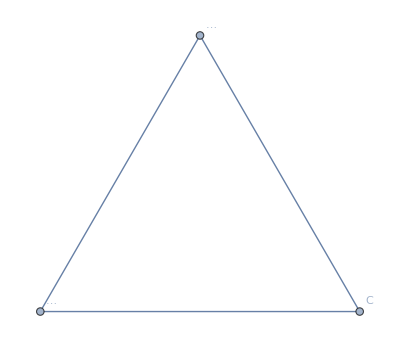

# RC Circuit + AD633

The standard RC circuit

In words, it is common for a stable periodic orbit of a parameterized ODE y'=f_μ(y) with period T_u to transform to a stable periodic orbit of period 2 T_μ at a given value of the parameter μ^*.  It is common for this to happen repeatedly and this “frequency-doubling cascade” route to chaos is generic.

# Bifurcations

Interesting things can happen long before ODEs go chaotic.  The key is to think about how equilibrium points can change with the parameters. Changes in the nature of the equilibrium points are called bifurcations.

### Rosseler System

Lets look at the equilibrium points for the Rosseler system.

```mathematica
StdParams={0.2,0.2,5.7};
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z,x + a y, b+z(x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1+y,x,0},{z,0,-c+x}}
sub=Simplify[Solve[f[{a,b,c}][{x,y,z}]=={0,0,0},{x,y,z}]]
```

{{x→1/2 (c-√(-4 a b+c^2)),y→(-c+√(-4 a b+c^2))/(2 a),z→(c-√(-4 a b+c^2))/(2 a)},{x→1/2 (c+√(-4 a b+c^2)),y→-(c+√(-4 a b+c^2))/(2 a),z→(c+√(-4 a b+c^2))/(2 a)}}

```mathematica
Map[MatrixForm,Simplify[df[{a,b,c}][{x,y,z}]/.sub]]
```

{(0 | -1 | -1
1+(-c+√(-4 a b+c^2))/(2 a) | 1/2 (c-√(-4 a b+c^2)) | 0
(c-√(-4 a b+c^2))/(2 a) | 0 | 1/2 (-c-√(-4 a b+c^2))),(0 | -1 | -1
1-(c+√(-4 a b+c^2))/(2 a) | 1/2 (c+√(-4 a b+c^2)) | 0
(c+√(-4 a b+c^2))/(2 a) | 0 | 1/2 (-c+√(-4 a b+c^2)))}

### VdP System

Lets look at the equilibrium points for the simpler VDP system.

```mathematica
f[μ_][{x_,y_}]:= {μ (1-y^2)x-y,x}
df[μ_][{x_,y_}]:={{(1-y^2) μ,-1-2 x y μ},{1,0}}
sub=Simplify[Solve[f[μ][{x,y}]=={0,0},{x,y}]]
```

{{x→0,y→0}}

```mathematica
Map[MatrixForm,A=Simplify[df[μ][{x,y}]/.sub]]
```

{(μ | -1
1 | 0)}

```mathematica
Eigenvalues[A]
```

{1/2 (μ-√(-4+μ^2)),1/2 (μ+√(-4+μ^2))}

```mathematica
Manipulate[
StreamPlot[ f[μ][{x,y}],{x,-5,5},{y,-5,5}],
{{μ,1},-1,5}]
```

```mathematica
Pic=ParametricPlot[ReIm[{1/2 (μ-√(-4+μ^2)),1/2 (μ+√(-4+μ^2))}],{μ,-1,3}];
Manipulate[Show[Pic, Epilog->{Red,PointSize[0.02], Point[ReIm[{1/2 (μ-√(-4+μ^2)),1/2 (μ+√(-4+μ^2))}]]}],
{μ,-1,3}]
```